### phase diagram

```mathematica
CP$new={{0.04,0.058},{0.066666666,0.0785},{0.1,0.105},{0.1333333334,0.1353333333},{0.18,0.186},{0.25,0.26875},{0.332,0.4},{0.4,0.55},{0.45,0.7},{0.47,0.8},{0.484,0.9},{0.488,1.},{0.488,1.05},{0.474,1.2},{0.456,1.3},{0.4,1.495},{0.3,1.69},{0.2,1.83},{0.1,1.929},{0.04,1.977}}
```

{{0.04,0.058},{0.0666667,0.0785},{0.1,0.105},{0.133333,0.135333},{0.18,0.186},{0.25,0.26875},{0.332,0.4},{0.4,0.55},{0.45,0.7},{0.47,0.8},{0.484,0.9},{0.488,1.},{0.488,1.05},{0.474,1.2},{0.456,1.3},{0.4,1.495},{0.3,1.69},{0.2,1.83},{0.1,1.929},{0.04,1.977}}

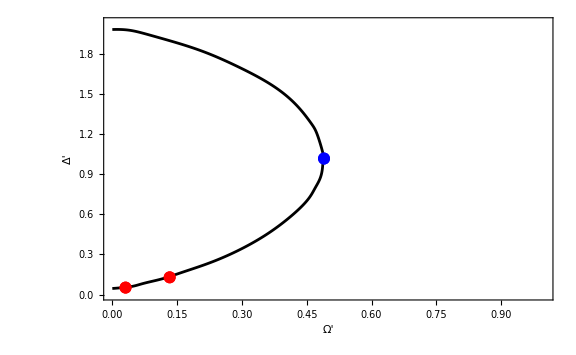

```mathematica
g1=Show[ListPlot[{{0,0.0453432}}~Join~CP$new~Join~{{0,1.9826732598039214}},PlotRange->{{0,1},{0,2.03}},PlotStyle->{Black,PointSize[0.007]},Joined->True,InterpolationOrder->5,Frame->True,FrameStyle->{Directive[Black,20],Directive[Black,20]},FrameLabel->{"Ω'","Δ'"},ImageSize->Large,Filling->Left],ListPlot[{{2 0.06640515431,0.128825999371}},PlotStyle->{Red,PointSize[0.015]}],ListPlot[{{0.030637254901960783,0.052006740196078434}},PlotStyle->{Red,PointSize[0.015]}(*PlotMarkers->{Graphics[{Darker[Green],Disk[]}],Offset[10]}*)],ListPlot[{{0.49,1.01734}},PlotStyle->{Blue,PointSize[0.015]}]]
```

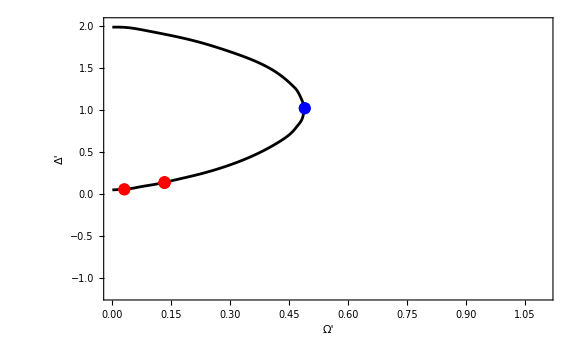

```mathematica
g1=Show[ListPlot[{{0,0.0453432}}~Join~CP$new~Join~{{0,1.9826732598039214}},PlotRange->{{0,1.1},{-1.2,2.03}},PlotStyle->{Black,PointSize[0.007]},Joined->True,InterpolationOrder->5,Frame->True,FrameStyle->{Directive[Black,20],Directive[Black,20]},FrameLabel->{"Ω'","Δ'"},ImageSize->Large,Filling->Left],ListPlot[{{0.133,0.129}},PlotStyle->{Red,PointSize[0.015]}],ListPlot[{{0.133,0.137}},PlotStyle->{Red,PointSize[0.015]}],ListPlot[{{0.030637254901960783,0.052006740196078434}},PlotStyle->{Red,PointSize[0.015]}(*PlotMarkers->{Graphics[{Darker[Green],Disk[]}],Offset[10]}*)],ListPlot[{{0.49,1.01734}},PlotStyle->{Blue,PointSize[0.015]}]]
```

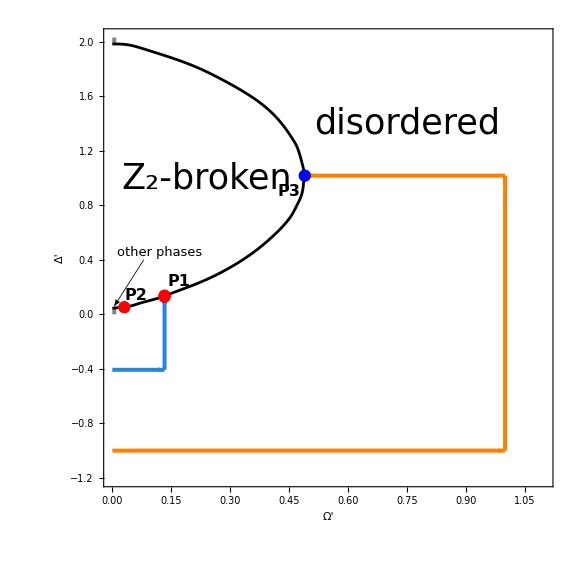

```mathematica
g2=Graphics[{Gray,Rectangle[{0,0},{0.01,0.04}],Rectangle[{0,1.985},{0.01,2.03}]}];
Show[g1,g2,Graphics[{RGBColor[0.149,0.529,0.847],Thickness[0.005],Arrowheads[0.025],Arrow[{{0,-0.407},{0.133,-0.407}}],Arrow[{{0.133,-0.407},{0.133,0.122}}]}],Graphics[{Orange,Thickness[0.005],Arrowheads[0.025],Arrow[{{0,-1},{1,-1}}],Arrow[{{1,-1},{1,Zeta[6]}}],Arrow[{{1,Zeta[6]},{0.493,Zeta[6]}}]}],Graphics[{Black,Thickness[0.001],Arrowheads[0.025],Arrow[{{0.08,0.4},{0.005,0.06}}],Text[Style["other phases",13],{0.12,0.45}],Text[Style["P2",Bold,16],{0.06,0.14}],Text[Style["P1",Bold,16],{0.17,0.24}],Text[Style["P3",Bold,16],{0.45,0.9}],Text[Style["Z_2-broken",35],{0.24,1}],Text[Style["disordered",35],{0.75,1.4}]}],AspectRatio->1]
```

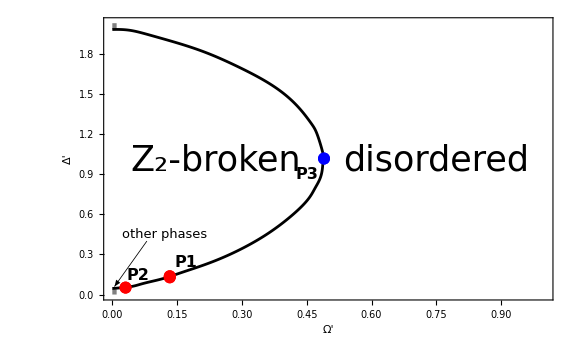

```mathematica
g1=Show[ListPlot[{{0,0.0453432}}~Join~CP$new~Join~{{0,1.9826732598039214}},PlotRange->{{0,1.},{0,2.03}},PlotStyle->{Black,PointSize[0.007]},Joined->True,InterpolationOrder->5,Frame->True,FrameStyle->{Directive[Black,20],Directive[Black,20]},FrameLabel->{"Ω'","Δ'"},ImageSize->Large,Filling->Left],ListPlot[{{0.133,0.129}},PlotStyle->{Red,PointSize[0.015]}],ListPlot[{{0.133,0.137}},PlotStyle->{Red,PointSize[0.015]}],ListPlot[{{0.030637254901960783,0.052006740196078434}},PlotStyle->{Red,PointSize[0.015]}(*PlotMarkers->{Graphics[{Darker[Green],Disk[]}],Offset[10]}*)],ListPlot[{{0.49,1.01734}},PlotStyle->{Blue,PointSize[0.015]}]];
g2=Graphics[{Gray,Rectangle[{0,0},{0.01,0.04}],Rectangle[{0,1.985},{0.01,2.03}]}];
Show[g1,g2,Graphics[{Black,Thickness[0.001],Arrowheads[0.025],Arrow[{{0.08,0.4},{0.005,0.06}}],Text[Style["other phases",13],{0.12,0.45}],Text[Style["P2",Bold,16],{0.06,0.14}],Text[Style["P1",Bold,16],{0.17,0.24}],Text[Style["P3",Bold,16],{0.45,0.9}],Text[Style["Z_2-broken",35],{0.24,1}],Text[Style["disordered",35],{0.75,1.}]}]]
```

### DMRG ⟨σσ⟩

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{0.6319967765174531,0.48857715985398276,0.4389694564183839,0.4068674461684058,0.38490307923708506,0.36804948915813773,0.3549127962952205,0.34421083732363467,0.3354457859814165,0.3281218922228694,0.32201021438733124,0.3168744551810463,0.3125946504591138,0.3090442867441435,0.306156877003633,0.30386097173698334,0.3021205855040111,0.30089617541077623,0.30017216869167634,0.2999304743017528}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

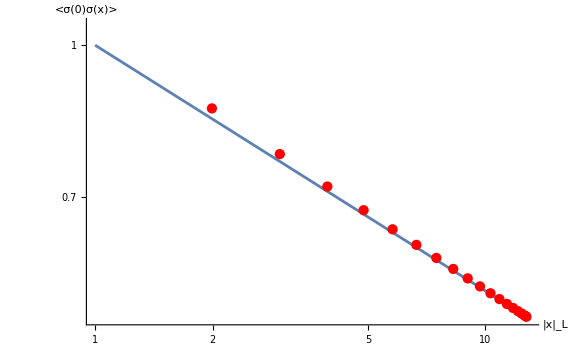

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0,1.05}}],ListLogLogPlot[data$temp2[[2;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

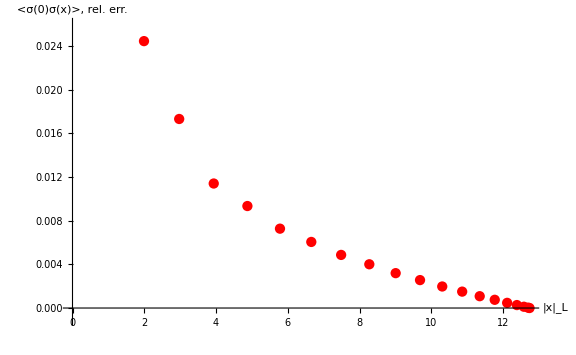

```mathematica
g1=({#[[1]],Abs[#[[2]]/(1/(#[[1]])^(1/4))-1]}&/@data$temp2//ListPlot[#,AxesLabel->{"|x|_L","<σ(0)σ(x)>, rel. err."},PlotRange->{-0.001,0.026},PlotStyle->Red,ImageSize->Large,AxesStyle->Large]&)
```

```mathematica
data$temp2
```

{{0.998972,1.11549},{1.99179,0.862353},{2.97232,0.774794},{3.93453,0.718133},{4.87248,0.679365},{5.78039,0.649618},{6.65266,0.626431},{7.48391,0.607542},{8.26903,0.592072},{9.00316,0.579145},{9.68179,0.568357},{10.3007,0.559293},{10.8562,0.551739},{11.3446,0.545472},{11.7632,0.540376},{12.1092,0.536323},{12.3806,0.533252},{12.5756,0.531091},{12.6931,0.529813},{12.7324,0.529386}}

```mathematica
√(((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528)
```

1.32854

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fig-sigma-sigma.pdf",g]
```

fig-sigma-sigma.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fig-sigma-sigma-error.pdf",g1]
```

fig-sigma-sigma-error.pdf

### DMRG ⟨σσ⟩ at Ω/C_6=0.18, Δ/C_6=0.178, the disordered phase

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{-0.6043967314873749,0.44782770327693044,-0.3892114081021346,0.35021637281464946,-0.32264287571885064,0.30111771232462864,-0.28401456519883095,0.2699189162200197,-0.25822911672108145,0.24838331818295625,-0.24009659976991707,0.23309507567606327,-0.2272255993909936,0.22233897781638667,-0.21834830204216965,0.2151684136880789,-0.21275104328014682,0.21104909514385084,-0.21004055068996658,0.20970457316162788}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

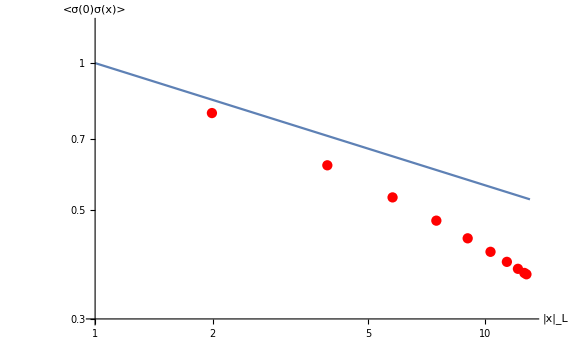

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0.3,1.2}}],ListLogLogPlot[data$temp2[[2;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

### DMRG ⟨σσ⟩ at Ω/C_6=0.18, Δ/C_6=0.19, the symmetry breaking phase

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{-0.6566719123041851,0.5250750002984526,-0.4836040288692108,0.45775015392037094,-0.4408804651044923,0.42828169158992985,-0.4187639368800001,0.41116570018820503,-0.40507956122179406,0.40007038213780177,-0.39595757579466984,0.39253953625800175,-0.38972466613635026,0.38740760710471844,-0.3855390455065105,0.384060568321491,-0.38294623579190806,0.3821640170204534,-0.38170323751239,0.3815490713011507}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

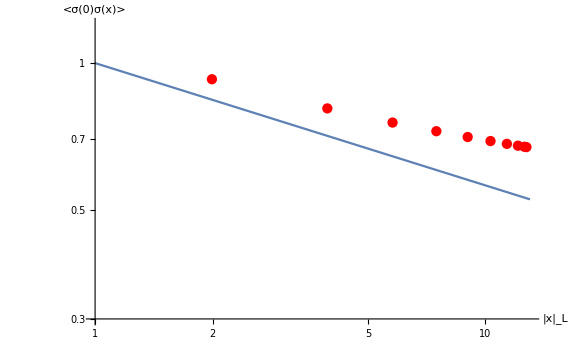

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0.3,1.2}}],ListLogLogPlot[data$temp2[[2;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

### DMRG ⟨ϵϵ⟩

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],((L/π)Sin[20 π/L])^-2/0.0014561975206714428{0.21036470881938163,0.10380767427270507,0.05828720083840144,0.01953085890256981,0.011722953664760671,0.007745839371092772,0.005711886789146192,0.0044059234222894594,0.0035721543520163546,0.002980672364247927,0.0025638868545783955,0.00225201963193139,0.002021572756812834,0.0018451766607710807,0.0017134080794678208,0.001613788879077288,0.0015425862960726233,0.0014935649314098964,0.0014657867406172587,0.0014561975206714428}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

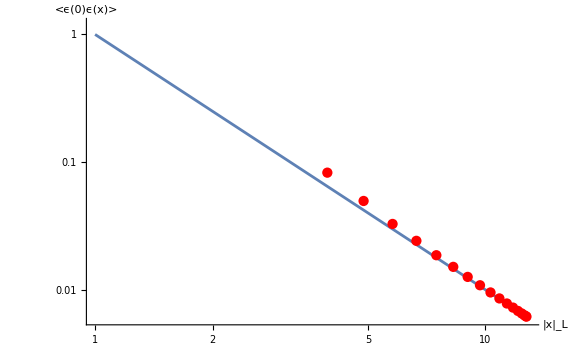

```mathematica
g=Show[LogLogPlot[1/y^2,{y,1,13},PlotRange->{Automatic,{0,1.2}}],ListLogLogPlot[data$temp2[[4;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<ϵ(0)ϵ(x)>"},ImageSize->Large,AxesStyle->Large]
```

```mathematica
√(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)
```

2.05816

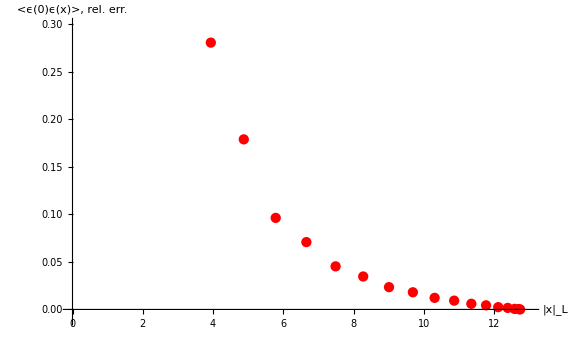

```mathematica
g1={#[[1]],Abs[#[[2]]/(1/(#[[1]])^2)-1]}&/@data$temp2⟦4;;All⟧//ListPlot[#,AxesLabel->{"|x|_L","<ϵ(0)ϵ(x)>, rel. err."},PlotRange->{{0,13},{-0.01,0.3}},PlotStyle->Red,ImageSize->Large,AxesStyle->Large]&
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/slava/Personal/----Fisica----/_Projects/Fork/2025 three_point_function_CFT

```mathematica
Export["fig-eps-eps.pdf",g]
Export["fig-eps-eps-error.pdf",g1]
```

fig-eps-eps.pdf

fig-eps-eps-error.pdf

### DMRG ⟨σσϵ⟩

```mathematica
data$temp=Abs/@{0.12437853107744494, -0.10918628313480952, 0.10380758320196523, -0.10437485622633542, 0.10181807304395053, -0.10023129144748673, 0.09827489616527886, -0.09682192706784315, 0.095382787505695, -0.09426830682280679, 0.0932482893590145, -0.09246478827778926, 0.09179446036934762, -0.09131266592769169, 0.09094914413849978, -0.09074816663718277, 0.09066974634279802, -0.0907419551749113, 0.09094481112578084, -0.09129745426804425, 0.09179554197773128, -0.09245344575569024, 0.09328168280439571, -0.09429314343979764, 0.09551578857094681, -0.09696508908969237, 0.09869372404563323, -0.10072752928921519, 0.10316043330404945, -0.10604840303557848, 0.10956610717780911, -0.1138625901028327, 0.11930337537172636, -0.12639319219383255, 0.1361106885025227, -0.15108371441060794, 0.17633364136277443, -0.2655927392616145, 0.3174038878073508, -0.10918628313480952, 0.05368380312369995, -0.05003900112383972, 0.058196557280829425, -0.06097218962568935, 0.06200030167124257, -0.06221074131816348, 0.06220765501055796, -0.0620170429597612, 0.06183813062734937, -0.06163419726389891, 0.0614929970119651, -0.06138264322374346, 0.061348712116679124, -0.06137012059037291, 0.061473485053079806, -0.06164707852415924, 0.061907952463085274, -0.06225260283778644, 0.06269306642446311, -0.06323397519598374, 0.06388503324873043, -0.06466017015835071, 0.06556907768023622, -0.06663827395118226, 0.06788055343582813, -0.06934212916272522, 0.07104507287173266, -0.07307077725657692, 0.07546621713227043, -0.07838546361382054, 0.08194961957552897, -0.08649291484424608, 0.09241399897047382, -0.10064931316794126, 0.11323109688401985, -0.13505220665577994, 0.20721616027994505, -0.2654537152211821, 0.10380758320196523, -0.05003900112383972, 0.010921369204204261, -0.014408179894977132, 0.01953111684573793, -0.02212185930126251, 0.023655338035249815, -0.02461200855475964, 0.025278069429279505, -0.02576071915659709, 0.026143197338265887, -0.02646301476280229, 0.026751885617137573, -0.02702661166862991, 0.02730208396104019, -0.02758790746263175, 0.027892648502799218, -0.02822347058305118, 0.028586738946455276, -0.028989544867270713, 0.02943823699281524, -0.029941449589369895, 0.03050707116919091, -0.031147374616196755, 0.03187363154262569, -0.03270524904130402, 0.03366015254383807, -0.034772090576570436, 0.03607266780673995, -0.037627425048389083, 0.03949903839463207, -0.041835934093411485, 0.044785745380695886, -0.048775423108706674, 0.054267492865111434, -0.0631891993787549, 0.0784177295209785, -0.13513895680107355, 0.17630767889893129, -0.10437485622633542, 0.058196557280829425, -0.014408179894977132, 0.0070382116416591, -0.008371906108199852, 0.011717511291539131, -0.013726423846409047, 0.01499988669421198, -0.01590477113396483, 0.01657863229060795, -0.017113681479994133, 0.017559056502730472, -0.017948363478002844, 0.018304131133250807, -0.018641685589571428, 0.018973596262692172, -0.0193085503184748, 0.01965512425805105, -0.020019609197160185, 0.02040943382737178, -0.020830729330849618, 0.0212914792607498, -0.021799231827864987, 0.022364475147984595, -0.02299790266540195, 0.023715531594850514, -0.02453424646106054, 0.025481678607986977, -0.026587484577939594, 0.027905719699897323, -0.02949476230641273, 0.03147877591654947, -0.033994523246569916, 0.037405337161162885, -0.04213584945031968, 0.04985964066081792, -0.0631825256136794, 0.11330422270626014, -0.1510440029523342, 0.10181807304395053, -0.06097218962568935, 0.01953111684573793, -0.008371906108199852, 0.003906260879489259, -0.005365413656318449, 0.007745902725498392, -0.00931200225724946, 0.010400669990622865, -0.01121203539733762, 0.011854430249760314, -0.01238358430556789, 0.012840823681979065, -0.013249313245797008, 0.013628492912111986, -0.013990638626506922, 0.014346653053088824, -0.014704756220942227, 0.015072337328902305, -0.01545648689620039, 0.01586354156544692, -0.016301242156415905, 0.016776513220546428, -0.017299659290085492, 0.017879785595689167, -0.01853269369983353, 0.01927228939708939, -0.020125738217889662, 0.02111736854509122, -0.022299962858934843, 0.02372184276925393, -0.025503050814966132, 0.02775901248886508, -0.030837044242181467, 0.03510367214360072, -0.04214173711789027, 0.054267416935425285, -0.10072825263044033, 0.13607806897120778, -0.10023129144748673, 0.06200030167124257, -0.02212185930126251, 0.011717511291539131, -0.005365413656318449, 0.002951684247381624, -0.0038389522213922536, 0.005710544418828136, -0.006995515943984852, 0.007923827731260309, -0.008651884445996533, 0.009244915027438069, -0.009751572019219622, 0.010198401825294166, -0.010606915359542697, 0.010990891292766269, -0.011361987362108557, 0.01172912565523304, -0.012100037837429144, 0.012481990535333653, -0.012881393961069132, 0.013305822306277736, -0.013762093577791916, 0.01425994164202952, -0.01480820862980175, 0.015421549597119295, -0.016113370228903714, 0.01690870532889214, -0.0178308998524431, 0.0189286487675993, -0.020248162404519463, 0.021900622668209125, -0.02399615986456191, 0.026858102400991943, -0.0308351115441791, 0.03740905256089979, -0.04877314084886849, 0.09248884257943617, -0.12635585517957837, 0.09827489616527886, -0.06221074131816348, 0.023655338035249815, -0.013726423846409047, 0.007745902725498392, -0.0038389522213922536, 0.0020766609233634423, -0.0029379812002525486, 0.004405938598625727, -0.005480929436619662, 0.0062931080574906775, -0.0069485666321694945, 0.007500634334318161, -0.007982247301862071, 0.008417086378266448, -0.008820694043679146, 0.009205801176326951, -0.009581910721079313, 0.009957270515000657, -0.010339328523698496, 0.010734634813121964, -0.011150774375606732, 0.011594359771707134, -0.01207500910615684, 0.012601005066866094, -0.013186718204926055, 0.01384449069675231, -0.014598748756378808, 0.015470864270581215, -0.016508184666841653, 0.017753127977037403, -0.01931343790503545, 0.02129087305215428, -0.023997702551273887, 0.027758771357294886, -0.03399992740537294, 0.04478536667883414, -0.0865693595706268, 0.11926750625918617, -0.09682192706784315, 0.06220765501055796, -0.02461200855475964, 0.01499988669421198, -0.00931200225724946, 0.005710544418828136, -0.0029379812002525486, 0.001702323475866355, -0.0023217681772175693, 0.003571624555604575, -0.004499138049176363, 0.005220526640479816, -0.005820221388556789, 0.006335867362866932, -0.006796355484367114, 0.007218895220866229, -0.007617770469101838, 0.008003184060162408, -0.008383997206787308, 0.008767907847953487, -0.009161724709258046, 0.009573020348392415, -0.010008442056743108, 0.010477348842082713, -0.010987914493996115, 0.011553927284805246, -0.012187455168310286, 0.012911809748808428, -0.013747747042970548, 0.01474042730391466, -0.015930958844506994, 0.01742227701433817, -0.01931278802986929, 0.02190156024008527, -0.02550233333240302, 0.031483621007207946, -0.04183483505156585, 0.08202398316637546, -0.1138240084269639, 0.095382787505695, -0.0620170429597612, 0.025278069429279505, -0.01590477113396483, 0.010400669990622865, -0.006995515943984852, 0.004405938598625727, -0.0023217681772175693, 0.0013387147690281027, -0.0019354240008297244, 0.0029806837930386105, -0.0037965862264452903, 0.004448759694202347, -0.005003086411671488, 0.005490696657753977, -0.0059336445278211965, 0.0063472206575724555, -0.006743107895969009, 0.007130636036557492, -0.00751805916786385, 0.007912359276746902, -0.008321309793617978, 0.008751506607029403, -0.009212302870464352, 0.009711620226459874, -0.010263057880252195, 0.010878165698006925, -0.011579799538716438, 0.012387692594547493, -0.01334598339214291, 0.014493782502621195, -0.01593152368407467, 0.017753024458419014, -0.020249690854914088, 0.023721869435316196, -0.029500419908508473, 0.03949883618103863, -0.07846045447204063, 0.10952796697192424, -0.09426830682280679, 0.06183813062734937, -0.02576071915659709, 0.01657863229060795, -0.01121203539733762, 0.007923827731260309, -0.005480929436619662, 0.003571624555604575, -0.0019354240008297244, 0.001158279101953886, -0.001629393629231744, 0.0025636400196057257, -0.003296058828304489, 0.003895464259491337, -0.0044155192196652475, 0.004881111060162838, -0.005311499146885288, 0.005719323763630256, -0.0061151505896943695, 0.006507637105067808, -0.006904259931656359, 0.007312899497261543, -0.007740334536379418, 0.008195811775230388, -0.008687264355201419, 0.00922795335298734, -0.009829292014983627, 0.010513458387008288, -0.01129978587426195, 0.012231046981208478, -0.013345475768569684, 0.014740471496502422, -0.016507528382959897, 0.01892964963779064, -0.02229956158774037, 0.027910972032232202, -0.037626789262413904, 0.07554012373861167, -0.10600867754054302, 0.0932482893590145, -0.06163419726389891, 0.026143197338265887, -0.017113681479994133, 0.011854430249760314, -0.008651884445996533, 0.0062931080574906775, -0.004499138049176363, 0.0029806837930386105, -0.001629393629231744, 0.0009743675490514727, -0.0014324475249051405, 0.0022520493353726046, -0.00292115591336019, 0.0034795489741653823, -0.003973295365750276, 0.004423094836740308, -0.004845365695902821, 0.00525126674128418, -0.005650651694973449, 0.006051260432450605, -0.006461454281755354, 0.006888072260049458, -0.007340503288033706, 0.007826573247351752, -0.008359471113325335, 0.00895031839994229, -0.009620996499009542, 0.010390226530659963, -0.011300048807031943, 0.012387473785421736, -0.013748087425694274, 0.015470485228098739, -0.017832191068443123, 0.021117341196274415, -0.026593155718033726, 0.03607250691833067, -0.07314500797051428, 0.10312078625424392, -0.09246478827778926, 0.0614929970119651, -0.02646301476280229, 0.017559056502730472, -0.01238358430556789, 0.009244915027438069, -0.0069485666321694945, 0.005220526640479816, -0.0037965862264452903, 0.0025636400196057257, -0.0014324475249051405, 0.0008776505310481593, -0.0012633097650256635, 0.0020214534814966337, -0.002642038778761192, 0.003170460249356446, -0.0036453088006546323, 0.004084857492624822, -0.004503500320223887, 0.00491172296534753, -0.005318293075640293, 0.005731791644683043, -0.006159499681094192, 0.006610831481383056, -0.007093748417818875, 0.007621271090203295, -0.008204472398882088, 0.008864818097489515, -0.009620773374642837, 0.010513483830158423, -0.011579343921846492, 0.012911892221643767, -0.014598075685208685, 0.01690966966521232, -0.02012541750844121, 0.025487080989517713, -0.03477167890451078, 0.07111871862632164, -0.10068692093719846, 0.09179446036934762, -0.06138264322374346, 0.026751885617137573, -0.017948363478002844, 0.012840823681979065, -0.009751572019219622, 0.007500634334318161, -0.005820221388556789, 0.004448759694202347, -0.003296058828304489, 0.0022520493353726046, -0.0012633097650256635, 0.0007739777508179832, -0.0011535165935412102, 0.001845187774577111, -0.002429938238293148, 0.0029357977656468727, -0.003398117729453536, 0.003832366083847861, -0.00425216544987936, 0.004666716782923664, -0.005085551121403886, 0.005516115902485702, -0.0059682400832558775, 0.006449880444224002, -0.0069741558589142254, 0.007551970720156466, -0.008204649437437265, 0.008950276656928522, -0.00982949711294168, 0.010877910251533084, -0.012187738498565063, 0.013844000591885957, -0.01611448851646724, 0.019272130611573526, -0.024539845177089313, 0.03366004242384831, -0.06941606771931502, 0.0986531887056776, -0.09131266592769169, 0.061348712116679124, -0.02702661166862991, 0.018304131133250807, -0.013249313245797008, 0.010198401825294166, -0.007982247301862071, 0.006335867362866932, -0.005003086411671488, 0.003895464259491337, -0.00292115591336019, 0.0020214534814966337, -0.0011535165935412102, 0.0007202673276319112, -0.0010562706858839447, 0.001713336685461053, -0.0022713603309577495, 0.0027627223202815517, -0.0032181258645652393, 0.003652455713201408, -0.0040777493337766915, 0.004503977745502406, -0.004939484860661068, 0.005394218073146268, -0.0058765132195865806, 0.006399449487351709, -0.006974022497832829, 0.007621315160299176, -0.008359295174889071, 0.00922801348844683, -0.010262665435997239, 0.011554066306689507, -0.013186061452261777, 0.015422458448147889, -0.018532294645034093, 0.02372087982874011, -0.032704929583073625, 0.06795411985130648, -0.09692390771855827, 0.09094914413849978, -0.06137012059037291, 0.02730208396104019, -0.018641685589571428, 0.013628492912111986, -0.010606915359542697, 0.008417086378266448, -0.006796355484367114, 0.005490696657753977, -0.0044155192196652475, 0.0034795489741653823, -0.002642038778761192, 0.001845187774577111, -0.0010562706858839447, 0.0006586901211014923, -0.000993353029598117, 0.0016137912787249022, -0.002154024268761958, 0.002636542664889881, -0.0030908481461256096, 0.0035298674196032795, -0.0039663006941977694, 0.004408863412030344, -0.004868317126709147, 0.005353103521046325, -0.005876639661564643, 0.006449871727146181, -0.0070939195317234255, 0.007826527133942666, -0.008687454866905147, 0.009711386084998087, -0.010988227287408387, 0.012600523602041188, -0.014809269210080835, 0.017879501941196696, -0.02300335721934169, 0.031873482606154746, -0.06671202078317917, 0.0954746341344328, -0.09074816663718277, 0.061473485053079806, -0.02758790746263175, 0.018973596262692172, -0.013990638626506922, 0.010990891292766269, -0.008820694043679146, 0.007218895220866229, -0.0059336445278211965, 0.004881111060162838, -0.003973295365750276, 0.003170460249356446, -0.002429938238293148, 0.001713336685461053, -0.000993353029598117, 0.0006305383936876785, -0.0009398187421961749, 0.0015425440932291762, -0.0020717444683551025, 0.002552108196672093, -0.0030103564695293885, 0.0034600385436566908, -0.003912499292131159, 0.00437881519865306, -0.004868253050986406, 0.005394269592161103, -0.00596815749441721, 0.00661093971070274, -0.007340400281191091, 0.008195941159729233, -0.009212018111617221, 0.010477613370726392, -0.012074473002288293, 0.014260915807436965, -0.017299237820576657, 0.022369759097822538, -0.031147086433409545, 0.06564260964518115, -0.09425160978378797, 0.09066974634279802, -0.06164707852415924, 0.027892648502799218, -0.0193085503184748, 0.014346653053088824, -0.011361987362108557, 0.009205801176326951, -0.007617770469101838, 0.0063472206575724555, -0.005311499146885288, 0.004423094836740308, -0.0036453088006546323, 0.0029357977656468727, -0.0022713603309577495, 0.0016137912787249022, -0.0009398187421961749, 0.0005943263436559954, -0.0009060567376375034, 0.0014935630889729818, -0.0020189586025214585, 0.002502500358517132, -0.0029709439108676237, 0.0034364484570156536, -0.003912563375328003, 0.0044088920245210165, -0.0049396188052650055, 0.005516122004368793, -0.006159720714204591, 0.006888098698832472, -0.007740599479066477, 0.008751375584147089, -0.010008864812884263, 0.011593983990040213, -0.013763207381116194, 0.016776176868746755, -0.02180456938693968, 0.030506884453553075, -0.06473384827307074, 0.09324021498830103, -0.0907419551749113, 0.061907952463085274, -0.02822347058305118, 0.01965512425805105, -0.014704756220942227, 0.01172912565523304, -0.009581910721079313, 0.008003184060162408, -0.006743107895969009, 0.005719323763630256, -0.004845365695902821, 0.004084857492624822, -0.003398117729453536, 0.0027627223202815517, -0.002154024268761958, 0.0015425440932291762, -0.0009060567376375034, 0.0005838983973645637, -0.0008833439002719895, 0.0014657724396027663, -0.0019935510675876673, 0.0024868427769091607, -0.0029709925510652928, 0.003460096805609905, -0.003966317493693505, 0.004504051853435175, -0.005085493537165277, 0.005731962768171657, -0.00646145566455873, 0.007313153353460843, -0.008321176592174843, 0.009573437551724575, -0.011150391231804049, 0.013306907943322954, -0.01630082904041207, 0.021296697062517248, -0.029941163152444526, 0.06395859667952766, -0.0924117994540811, 0.09094481112578084, -0.06225260283778644, 0.028586738946455276, -0.020019609197160185, 0.015072337328902305, -0.012100037837429144, 0.009957270515000657, -0.008383997206787308, 0.007130636036557492, -0.0061151505896943695, 0.00525126674128418, -0.004503500320223887, 0.003832366083847861, -0.0032181258645652393, 0.002636542664889881, -0.0020717444683551025, 0.0014935630889729818, -0.0008833439002719895, 0.000565242067869787, -0.000870879987385652, 0.0014561943702519852, -0.0019933333002551228, 0.0025025231644632356, -0.003010388852196621, 0.0035299125830241776, -0.004077853715626598, 0.004666719155065224, -0.005318514110418718, 0.006051330550330961, -0.006904611368144266, 0.007912335689592804, -0.009162255811906297, 0.01073438073756891, -0.012882600527346987, 0.015863203806391443, -0.02083598100013564, 0.02943800855042297, -0.06330764896799507, 0.09175399646295189, -0.09129745426804425, 0.06269306642446311, -0.028989544867270713, 0.02040943382737178, -0.01545648689620039, 0.012481990535333653, -0.010339328523698496, 0.008767907847953487, -0.00751805916786385, 0.006507637105067808, -0.005650651694973449, 0.00491172296534753, -0.00425216544987936, 0.003652455713201408, -0.0030908481461256096, 0.002552108196672093, -0.0020189586025214585, 0.0014657724396027663, -0.000870879987385652, 0.0005694481007038228, -0.0008738300109510114, 0.001465790727495051, -0.002019222388583661, 0.0025521911191569054, -0.003090947040396156, 0.0036525785131889233, -0.004252181081086831, 0.004911886107881879, -0.005650658441048596, 0.006507950492232851, -0.007518018722430395, 0.008768430139387228, -0.010339083034453874, 0.012483204855338445, -0.015456119757032465, 0.020414607221736773, -0.0289892448721138, 0.06276667696787556, -0.09125587974365683, 0.09179554197773128, -0.06323397519598374, 0.02943823699281524, -0.020830729330849618, 0.01586354156544692, -0.012881393961069132, 0.010734634813121964, -0.009161724709258046, 0.007912359276746902, -0.006904259931656359, 0.006051260432450605, -0.005318293075640293, 0.004666716782923664, -0.0040777493337766915, 0.0035298674196032795, -0.0030103564695293885, 0.002502500358517132, -0.0019935510675876673, 0.0014561943702519852, -0.0008738300109510114, 0.000565146003751223, -0.0008803874150715809, 0.0014935862337403182, -0.00207158931391813, 0.002636604397120422, -0.0032182197540517894, 0.0038324068399614207, -0.0045036624287361025, 0.005251299016258708, -0.006115508326554085, 0.0071306503542914405, -0.008384583100771342, 0.009957118236238748, -0.012101366426203256, 0.01507207989338311, -0.020024863906914814, 0.028586521775160308, -0.06232632610577242, 0.09090340657930908, -0.09245344575569024, 0.06388503324873043, -0.029941449589369895, 0.0212914792607498, -0.016301242156415905, 0.013305822306277736, -0.011150774375606732, 0.009573020348392415, -0.008321309793617978, 0.007312899497261543, -0.006461454281755354, 0.005731791644683043, -0.005085551121403886, 0.004503977745502406, -0.0039663006941977694, 0.0034600385436566908, -0.0029709439108676237, 0.0024868427769091607, -0.0019933333002551228, 0.001465790727495051, -0.0008803874150715809, 0.000584105913209245, -0.0009090773522883722, 0.0015426088601773456, -0.002154312888809208, 0.0027628405964553746, -0.0033981915923946052, 0.0040850031072430905, -0.004845368865342057, 0.005719614923894325, -0.006743055475994822, 0.008003706920027194, -0.009581724842866379, 0.011730430213748337, -0.014704459423624174, 0.01966031516893511, -0.028223191796976226, 0.061981648180876134, -0.09070065270575756, 0.09328168280439571, -0.06466017015835071, 0.03050707116919091, -0.021799231827864987, 0.016776513220546428, -0.013762093577791916, 0.011594359771707134, -0.010008442056743108, 0.008751506607029403, -0.007740334536379418, 0.006888072260049458, -0.006159499681094192, 0.005516115902485702, -0.004939484860661068, 0.004408863412030344, -0.003912499292131159, 0.0034364484570156536, -0.0029709925510652928, 0.0025025231644632356, -0.002019222388583661, 0.0014935862337403182, -0.0009090773522883722, 0.0005940189750097115, -0.0009367804726919839, 0.0016138062660331516, -0.0022711985901542105, 0.0029358104106274275, -0.0036454128559104356, 0.004423101000204862, -0.005311755905091947, 0.006347148339990267, -0.007618289297865326, 0.00920564756868717, -0.011363344669002795, 0.014346440041058693, -0.01931383396290702, 0.027892471778804273, -0.061720906329468965, 0.09062868565990775, -0.09429314343979764, 0.06556907768023622, -0.031147374616196755, 0.022364475147984595, -0.017299659290085492, 0.01425994164202952, -0.01207500910615684, 0.010477348842082713, -0.009212302870464352, 0.008195811775230388, -0.007340503288033706, 0.006610831481383056, -0.0059682400832558775, 0.005394218073146268, -0.004868317126709147, 0.00437881519865306, -0.003912563375328003, 0.003460096805609905, -0.003010388852196621, 0.0025521911191569054, -0.00207158931391813, 0.0015426088601773456, -0.0009367804726919839, 0.0006309952145692488, -0.0009965153744734803, 0.001713402180019065, -0.002430184610493042, 0.0031705878151358654, -0.003973328509818201, 0.0048813072700921, -0.0059334867197117945, 0.007219303282553923, -0.00882045298576287, 0.010992169811473086, -0.01399036423814436, 0.018978834041736132, -0.027587683767487423, 0.061547333597931596, -0.09070737901823124, 0.09551578857094681, -0.06663827395118226, 0.03187363154262569, -0.02299790266540195, 0.017879785595689167, -0.01480820862980175, 0.012601005066866094, -0.010987914493996115, 0.009711620226459874, -0.008687264355201419, 0.007826573247351752, -0.007093748417818875, 0.006449880444224002, -0.0058765132195865806, 0.005353103521046325, -0.004868253050986406, 0.0044088920245210165, -0.003966317493693505, 0.0035299125830241776, -0.003090947040396156, 0.002636604397120422, -0.002154312888809208, 0.0016138062660331516, -0.0009965153744734803, 0.0006581126700623028, -0.0010530273792449612, 0.001845143828739322, -0.0026418625390856524, 0.0034795125802098924, -0.004415648513623594, 0.0054905271071942555, -0.0067967401629746675, 0.008416873375606338, -0.010608235030032448, 0.01362825280895208, -0.018646956932853186, 0.027301901593253013, -0.06144406788171027, 0.09090866980309822, -0.09696508908969237, 0.06788055343582813, -0.03270524904130402, 0.023715531594850514, -0.01853269369983353, 0.015421549597119295, -0.013186718204926055, 0.011553927284805246, -0.010263057880252195, 0.00922795335298734, -0.008359471113325335, 0.007621271090203295, -0.0069741558589142254, 0.006399449487351709, -0.005876639661564643, 0.005394269592161103, -0.0049396188052650055, 0.004504051853435175, -0.004077853715626598, 0.0036525785131889233, -0.0032182197540517894, 0.0027628405964553746, -0.0022711985901542105, 0.001713402180019065, -0.0010530273792449612, 0.0007210154126281004, -0.0011568940771774603, 0.0020215301202918872, -0.00292138014144698, 0.003895614666147822, -0.005002938947902579, 0.006336195103317052, -0.007982009777849873, 0.010199691203532119, -0.01324901677540226, 0.018309325859074313, -0.027026330266255134, 0.06142269713154509, -0.09127265067395966, 0.09869372404563323, -0.06934212916272522, 0.03366015254383807, -0.02453424646106054, 0.01927228939708939, -0.016113370228903714, 0.01384449069675231, -0.012187455168310286, 0.010878165698006925, -0.009829292014983627, 0.00895031839994229, -0.008204472398882088, 0.007551970720156466, -0.006974022497832829, 0.006449871727146181, -0.00596815749441721, 0.005516122004368793, -0.005085493537165277, 0.004666719155065224, -0.004252181081086831, 0.0038324068399614207, -0.0033981915923946052, 0.0029358104106274275, -0.002430184610493042, 0.001845143828739322, -0.0011568940771774603, 0.0007730236345801562, -0.0012597722146841359, 0.002251986864379078, -0.003295908006370711, 0.004448571327158242, -0.0058205047206002355, 0.007500448368775415, -0.009752916862363755, 0.012840580865357002, -0.017953593996571416, 0.026751576944292338, -0.06145665548671041, 0.09175482494578834, -0.10072752928921519, 0.07104507287173266, -0.034772090576570436, 0.025481678607986977, -0.020125738217889662, 0.01690870532889214, -0.014598748756378808, 0.012911809748808428, -0.011579799538716438, 0.010513458387008288, -0.009620996499009542, 0.008864818097489515, -0.008204649437437265, 0.007621315160299176, -0.0070939195317234255, 0.00661093971070274, -0.006159720714204591, 0.005731962768171657, -0.005318514110418718, 0.004911886107881879, -0.0045036624287361025, 0.0040850031072430905, -0.0036454128559104356, 0.0031705878151358654, -0.0026418625390856524, 0.0020215301202918872, -0.0012597722146841359, 0.0008788648854634949, -0.0014362156323652767, 0.0025637608969795974, -0.003796702024169813, 0.005220861012860175, -0.0069484325614776535, 0.009246235116064242, -0.012383306928464136, 0.01756419774033759, -0.026462583340733196, 0.06156708972754618, -0.09242584259877125, 0.10316043330404945, -0.07307077725657692, 0.03607266780673995, -0.026587484577939594, 0.02111736854509122, -0.0178308998524431, 0.015470864270581215, -0.013747747042970548, 0.012387692594547493, -0.01129978587426195, 0.010390226530659963, -0.009620773374642837, 0.008950276656928522, -0.008359295174889071, 0.007826527133942666, -0.007340400281191091, 0.006888098698832472, -0.00646145566455873, 0.006051330550330961, -0.005650658441048596, 0.005251299016258708, -0.004845368865342057, 0.004423101000204862, -0.003973328509818201, 0.0034795125802098924, -0.00292138014144698, 0.002251986864379078, -0.0014362156323652767, 0.0009728628947755516, -0.0016253812986176453, 0.0029805124691149776, -0.004499161393078905, 0.006292960359876659, -0.008653189497472895, 0.01185421893876057, -0.017118871207737713, 0.02614274402396015, -0.0617084081991366, 0.09320996180683262, -0.10604840303557848, 0.07546621713227043, -0.037627425048389083, 0.027905719699897323, -0.022299962858934843, 0.0189286487675993, -0.016508184666841653, 0.01474042730391466, -0.01334598339214291, 0.012231046981208478, -0.011300048807031943, 0.010513483830158423, -0.00982949711294168, 0.00922801348844683, -0.008687454866905147, 0.008195941159729233, -0.007740599479066477, 0.007313153353460843, -0.006904611368144266, 0.006507950492232851, -0.006115508326554085, 0.005719614923894325, -0.005311755905091947, 0.0048813072700921, -0.004415648513623594, 0.003895614666147822, -0.003295908006370711, 0.0025637608969795974, -0.0016253812986176453, 0.0011601687549058607, -0.0019396873458827292, 0.0035718520691751035, -0.0054810310410208524, 0.007925066432338153, -0.011211783359113612, 0.016583729853815374, -0.025760090046479313, 0.061912521010641874, -0.09423109347360711, 0.10956610717780911, -0.07838546361382054, 0.03949903839463207, -0.02949476230641273, 0.02372184276925393, -0.020248162404519463, 0.017753127977037403, -0.015930958844506994, 0.014493782502621195, -0.013345475768569684, 0.012387473785421736, -0.011579343921846492, 0.010877910251533084, -0.010262665435997239, 0.009711386084998087, -0.009212018111617221, 0.008751375584147089, -0.008321176592174843, 0.007912335689592804, -0.007518018722430395, 0.0071306503542914405, -0.006743055475994822, 0.006347148339990267, -0.0059334867197117945, 0.0054905271071942555, -0.005002938947902579, 0.004448571327158242, -0.003796702024169813, 0.0029805124691149776, -0.0019396873458827292, 0.0013362044507617698, -0.0023170618424805073, 0.004405753962852479, -0.006996435979645677, 0.010400446204865844, -0.015909891731701223, 0.025277449670978426, -0.06209171312659625, 0.09534654927561484, -0.1138625901028327, 0.08194961957552897, -0.041835934093411485, 0.03147877591654947, -0.025503050814966132, 0.021900622668209125, -0.01931343790503545, 0.01742227701433817, -0.01593152368407467, 0.014740471496502422, -0.013748087425694274, 0.012911892221643767, -0.012187738498565063, 0.011554066306689507, -0.010988227287408387, 0.010477613370726392, -0.010008864812884263, 0.009573437551724575, -0.009162255811906297, 0.008768430139387228, -0.008384583100771342, 0.008003706920027194, -0.007618289297865326, 0.007219303282553923, -0.0067967401629746675, 0.006336195103317052, -0.0058205047206002355, 0.005220861012860175, -0.004499161393078905, 0.0035718520691751035, -0.0023170618424805073, 0.001705471889426862, -0.00294319842712827, 0.005711626287811613, -0.009311980436574413, 0.01500480776971385, -0.024611146994416157, 0.062282678166165124, -0.0967875123254349, 0.11930337537172636, -0.08649291484424608, 0.044785745380695886, -0.033994523246569916, 0.02775901248886508, -0.02399615986456191, 0.02129087305215428, -0.01931278802986929, 0.017753024458419014, -0.016507528382959897, 0.015470485228098739, -0.014598075685208685, 0.013844000591885957, -0.013186061452261777, 0.012600523602041188, -0.012074473002288293, 0.011593983990040213, -0.011150391231804049, 0.01073438073756891, -0.010339083034453874, 0.009957118236238748, -0.009581724842866379, 0.00920564756868717, -0.00882045298576287, 0.008416873375606338, -0.007982009777849873, 0.007500448368775415, -0.0069484325614776535, 0.006292960359876659, -0.0054810310410208524, 0.004405753962852479, -0.00294319842712827, 0.002072557714297241, -0.0038338959315446478, 0.007745843742329832, -0.013731243098218996, 0.023654758615877534, -0.06228668810223054, 0.09824259329678742, -0.12639319219383255, 0.09241399897047382, -0.048775423108706674, 0.037405337161162885, -0.030837044242181467, 0.026858102400991943, -0.023997702551273887, 0.02190156024008527, -0.020249690854914088, 0.01892964963779064, -0.017832191068443123, 0.01690966966521232, -0.01611448851646724, 0.015422458448147889, -0.014809269210080835, 0.014260915807436965, -0.013763207381116194, 0.013306907943322954, -0.012882600527346987, 0.012483204855338445, -0.012101366426203256, 0.011730430213748337, -0.011363344669002795, 0.010992169811473086, -0.010608235030032448, 0.010199691203532119, -0.009752916862363755, 0.009246235116064242, -0.008653189497472895, 0.007925066432338153, -0.006996435979645677, 0.005711626287811613, -0.0038338959315446478, 0.0029581316417624523, -0.00537204596827945, 0.011721957786139787, -0.02212087178959834, 0.062076529181751064, -0.10020203044069065, 0.1361106885025227, -0.10064931316794126, 0.054267492865111434, -0.04213584945031968, 0.03510367214360072, -0.0308351115441791, 0.027758771357294886, -0.02550233333240302, 0.023721869435316196, -0.02229956158774037, 0.021117341196274415, -0.02012541750844121, 0.019272130611573526, -0.018532294645034093, 0.017879501941196696, -0.017299237820576657, 0.016776176868746755, -0.01630082904041207, 0.015863203806391443, -0.015456119757032465, 0.01507207989338311, -0.014704459423624174, 0.014346440041058693, -0.01399036423814436, 0.01362825280895208, -0.01324901677540226, 0.012840580865357002, -0.012383306928464136, 0.01185421893876057, -0.011211783359113612, 0.010400446204865844, -0.009311980436574413, 0.007745843742329832, -0.00537204596827945, 0.0038977669834704726, -0.008367979110496885, 0.019530270151111515, -0.06104943800829664, 0.10179243849700523, -0.15108371441060794, 0.11323109688401985, -0.0631891993787549, 0.04985964066081792, -0.04214173711789027, 0.03740905256089979, -0.03399992740537294, 0.031483621007207946, -0.029500419908508473, 0.027910972032232202, -0.026593155718033726, 0.025487080989517713, -0.024539845177089313, 0.02372087982874011, -0.02300335721934169, 0.022369759097822538, -0.02180456938693968, 0.021296697062517248, -0.02083598100013564, 0.020414607221736773, -0.020024863906914814, 0.01966031516893511, -0.01931383396290702, 0.018978834041736132, -0.018646956932853186, 0.018309325859074313, -0.017953593996571416, 0.01756419774033759, -0.017118871207737713, 0.016583729853815374, -0.015909891731701223, 0.01500480776971385, -0.013731243098218996, 0.011721957786139787, -0.008367979110496885, 0.0070548691466420805, -0.01441498813295833, 0.05827325132933943, -0.10435759195665767, 0.17633364136277443, -0.13505220665577994, 0.0784177295209785, -0.0631825256136794, 0.054267416935425285, -0.04877314084886849, 0.04478536667883414, -0.04183483505156585, 0.03949883618103863, -0.037626789262413904, 0.03607250691833067, -0.03477167890451078, 0.03366004242384831, -0.032704929583073625, 0.031873482606154746, -0.031147086433409545, 0.030506884453553075, -0.029941163152444526, 0.02943800855042297, -0.0289892448721138, 0.028586521775160308, -0.028223191796976226, 0.027892471778804273, -0.027587683767487423, 0.027301901593253013, -0.027026330266255134, 0.026751576944292338, -0.026462583340733196, 0.02614274402396015, -0.025760090046479313, 0.025277449670978426, -0.024611146994416157, 0.023654758615877534, -0.02212087178959834, 0.019530270151111515, -0.01441498813295833, 0.010895064557839609, -0.050108045749638244, 0.10380709850275646, -0.2655927392616145, 0.20721616027994505, -0.13513895680107355, 0.11330422270626014, -0.10072825263044033, 0.09248884257943617, -0.0865693595706268, 0.08202398316637546, -0.07846045447204063, 0.07554012373861167, -0.07314500797051428, 0.07111871862632164, -0.06941606771931502, 0.06795411985130648, -0.06671202078317917, 0.06564260964518115, -0.06473384827307074, 0.06395859667952766, -0.06330764896799507, 0.06276667696787556, -0.06232632610577242, 0.061981648180876134, -0.061720906329468965, 0.061547333597931596, -0.06144406788171027, 0.06142269713154509, -0.06145665548671041, 0.06156708972754618, -0.0617084081991366, 0.061912521010641874, -0.06209171312659625, 0.062282678166165124, -0.06228668810223054, 0.062076529181751064, -0.06104943800829664, 0.05827325132933943, -0.050108045749638244, 0.05383114056899224, -0.10925129414082262, 0.3174038878073508, -0.2654537152211821, 0.17630767889893129, -0.1510440029523342, 0.13607806897120778, -0.12635585517957837, 0.11926750625918617, -0.1138240084269639, 0.10952796697192424, -0.10600867754054302, 0.10312078625424392, -0.10068692093719846, 0.0986531887056776, -0.09692390771855827, 0.0954746341344328, -0.09425160978378797, 0.09324021498830103, -0.0924117994540811, 0.09175399646295189, -0.09125587974365683, 0.09090340657930908, -0.09070065270575756, 0.09062868565990775, -0.09070737901823124, 0.09090866980309822, -0.09127265067395966, 0.09175482494578834, -0.09242584259877125, 0.09320996180683262, -0.09423109347360711, 0.09534654927561484, -0.0967875123254349, 0.09824259329678742, -0.10020203044069065, 0.10179243849700523, -0.10435759195665767, 0.10380709850275646, -0.10925129414082262, 0.12437857821874772};
data$temp=Riffle[Table[{i,j},{i,1,39},{j,1,39}]//Flatten[#,1]&,((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528 √(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)data$temp]//Partition[#,2]&;
data=Flatten/@data$temp;
```

```mathematica
Ising3pt[x1_,x2_,x3_]:=c123/((Abs[(L/π)Sin[(x1-x2) π/L]])^Δϵ(Abs[(L/π)Sin[(x1-x3) π/L]])^Δϵ(Abs[(L/π)Sin[(x2-x3) π/L]])^(2Δσ-Δϵ))/.{Δϵ->1,Δσ->1/8,c123->1/2};
```

```mathematica
Select[data,#[[1]]==10&];
g1={#[[2]],#[[3]]}&/@%//ListPlot[#,PlotStyle->Red]&;
```

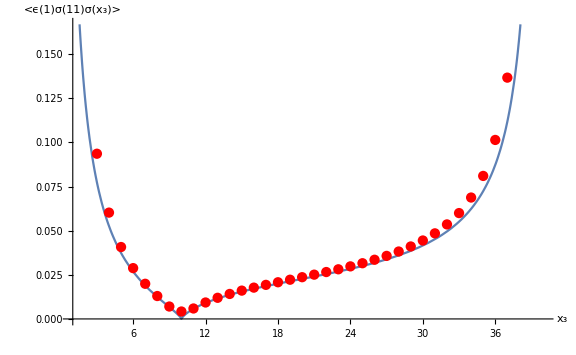

```mathematica
Show[Plot[Ising3pt[0,10,x3],{x3,1,40}],g1,AxesLabel->{"x_3","<ϵ(1)σ(11)σ(x_3)>"},ImageSize->Large,AxesStyle->Large]
```

```mathematica
(*ListContourPlot[data,Contours->{10^-2,10^-1.5,10^-1(*,10^-0.5,1*)},FrameLabel->{"x_2","x_3"},PlotLegends->BarLegend[Automatic,All,"TickLabels"->(Superscript[10,#]&/@{-2,-1.5,-1})],ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}]];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-DMRG.pdf",%]*)
```

```mathematica
(* ContourPlot[Ising3pt[0,x2,x3],{x2,0,40},{x3,0,40},PlotPoints->50,FrameLabel->{"x_2","x_3"},Contours->{10^-2,10^-1.5,10^-1(*,10^-0.5,1*)},PlotLegends->BarLegend[Automatic,All,"TickLabels"->(Superscript[10,#]&/@{-2,-1.5,-1})],ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}]]
Export["fig-eps-sig-sig-theory.pdf",%] *)
```

```mathematica
Plot3D[f[x2,x3,40],{x2,0,40},{x3,0,40},PlotPoints->100,PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, CFT",AxesLabel->{"x_2","x_3"},PlotRange->{0,10^-0.5}]
Export["fig-eps-sig-sig-theory-3D.pdf",Rasterize[%,"Image"]]
```

-Graphics3D-

fig-eps-sig-sig-theory-3D.pdf

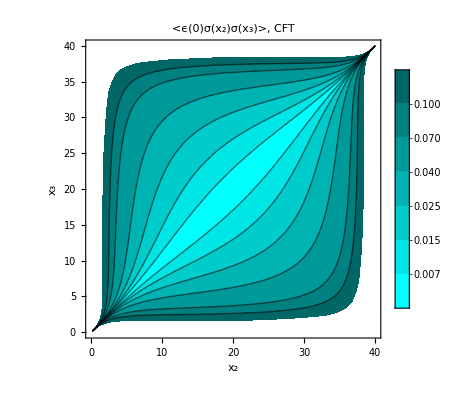

fig-eps-sig-sig-theory.pdf

```mathematica
ContourPlot[Ising3pt[0,x2,x3],{x2,0,40},{x3,0,40},PlotPoints->50,FrameLabel->{"x_2","x_3"},Contours->{0.007,0.015,0.025,0.04,0.07,10^-1},PlotRange->{0,0.16},PlotLegends->Automatic,ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}],PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, CFT"]
Export["fig-eps-sig-sig-theory.pdf",Rasterize[%,"Image"]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

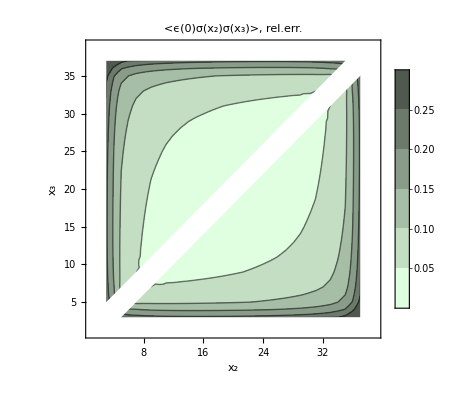

fig-eps-sig-sig-relative-error.pdf

```mathematica
{#[[1]],#[[2]],Abs[(#[[3]])/Ising3pt[0,#[[1]],#[[2]]]-1]}&/@data;
ListContourPlot[%,Contours->{0.05,0.1,0.15,0.2,0.25},FrameLabel->{"x_2","x_3"},ContourShading->Table[Darker[LightGreen,i],{i,0,1,0.13}],PlotLegends->Automatic,PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, rel.err."];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-relative-error.pdf",Rasterize[%,"Image"]]
(*ContourPlot[%,{x2,0,39},{x3,0,39},FrameLabel->{"x_2","x_3"},Contours->{10^-2,10^-1.5,10^-1,10^-0.5},PlotLegends->Automatic,ContourShading->Table[Darker[Cyan,i],{i,0,1,0.2}]]*)
```

```mathematica
{#[[1]],#[[2]],Abs[(#[[3]])/Ising3pt[0,#[[1]],#[[2]]]-1]}&/@data;
cp=ListContourPlot[%,Contours->{0.1},ContourShading->False,ContourStyle->{Thick,Dashed,Red}];

(*ContourPlot[%,{x2,0,39},{x3,0,39},FrameLabel->{"x_2","x_3"},Contours->{10^-2,10^-1.5,10^-1,10^-0.5},PlotLegends->Automatic,ContourShading->Table[Darker[Cyan,i],{i,0,1,0.2}]]*)
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

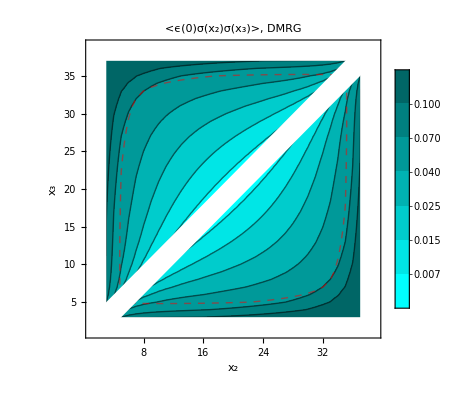

fig-eps-sig-sig-DMRG.pdf

```mathematica
ListContourPlot[data,Contours->{0.007,0.015,0.025,0.04,0.07,10^-1},FrameLabel->{"x_2","x_3"},PlotLegends->Automatic,ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}],PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, DMRG"];
Show[%,cp,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-DMRG.pdf",Rasterize[%,"Image"]]
```

### sample ⟨σσ⟩

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/slava/Personal/----Fisica----/_Projects/Fork/2025 three_point_function_CFT

```mathematica
x={0.9989722332485386,1.991785470487123,2.972318687964274,3.9345265723338643,4.872476792022164,5.780386572024696,6.652658346637106,7.483914270309113,8.26902937385063,9.003163161571061,9.681789454544852,10.300724296009678,10.85615174685119,11.344647412136574,11.763199553648057,12.10922765825051,12.380598347613041,12.575638531195816,12.693145721409602,12.732395447351628};
y={1.1162044184049587,0.8593044293176056,0.7653166284319898,0.7066294100386218,0.6681517751220695,0.6366460052477364,0.6090674251756654,0.5871369383023552,0.5723989451118403,0.5610586329862046,0.552807121828642,0.5458352567864216,0.5398782834908555,0.5367894825227826,0.5348479504857079,0.5346273218451318,0.5337889330109401,0.5299499946649089,0.5265964393281453,0.525449170397147};
dy={0.00697848012018246,0.00967646264811299,0.011013764409377753,0.01199259602265474,0.012828705373956112,0.013634799742493374,0.014190906786570324,0.014803041237097508,0.015307593598250246,0.015665678592954844,0.0158981898072701,0.016277021836553246,0.016673603248216193,0.01693434023695811,0.017003633328208055,0.017165525071457223,0.01734427914573818,0.01769384975095982,0.018075259954768556,0.018391339508440525};
data$temp=MapThread[{#1,Around[#2,#3]}&,{x,y,dy}];
```

```mathematica
data$temp
```

{{0.998972,1.1160.007},{1.99179,0.8590.010},{2.97232,0.7650.011},{3.93453,0.7070.012},{4.87248,0.6680.013},{5.78039,0.6370.014},{6.65266,0.6090.014},{7.48391,0.5870.015},{8.26903,0.5720.015},{9.00316,0.5610.016},{9.68179,0.5530.016},{10.3007,0.5460.016},{10.8562,0.5400.017},{11.3446,0.5370.017},{11.7632,0.5350.017},{12.1092,0.5350.017},{12.3806,0.5340.017},{12.5756,0.5300.018},{12.6931,0.5270.018},{12.7324,0.5250.018}}

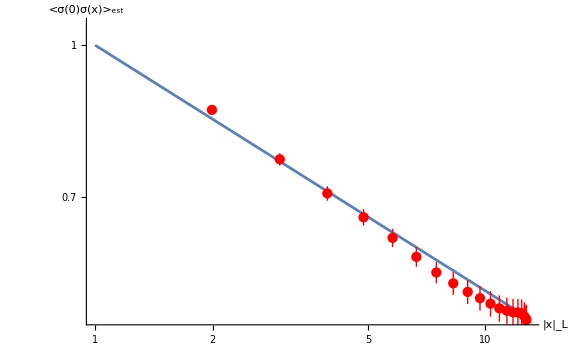

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0,1.05}},AxesLabel->{"|x|_L","<σ(0)σ(x)>_est"}],ListLogLogPlot[data$temp[[2;;20]],(*draw error bars*)IntervalMarkersStyle->Automatic,PlotRange->All,AxesLabel->{"x","y"},PlotStyle->Red],AxesStyle->Large,ImageSize->Large]
```

```mathematica
Export["fig-sigma-sigma-sample-10e3.pdf",g]
```

fig-sigma-sigma-sample-10e3.pdf

```mathematica
x={0.9989722332485386,1.991785470487123,2.972318687964274,3.9345265723338643,4.872476792022164,5.780386572024696,6.652658346637106,7.483914270309113,8.26902937385063,9.003163161571061,9.681789454544852,10.300724296009678,10.85615174685119,11.344647412136574,11.763199553648057,12.10922765825051,12.380598347613041,12.575638531195816,12.693145721409602,12.732395447351628};
y={1.1165927248123748,0.863628750672908,0.7759376911893453,0.7191743545418068,0.6803701892372009,0.6505897353321752,0.6273045886057248,0.6082202111958521,0.5921805090259354,0.5787177493779538,0.5682864272514935,0.5599157766280186,0.5532174911001143,0.5483504232889951,0.5442643808655171,0.5405578197038309,0.5374954941726282,0.5354745358249468,0.534393455486122,0.5339389604865344};
dy={0.002233993715770497,0.003071945048514788,0.0035008007939038334,0.0038344792742939725,0.004083263031870124,0.004316340574922186,0.004501938595646539,0.0046880330061162935,0.004826394836117002,0.004970680887066167,0.005089634759181583,0.005216934268302672,0.005319775954826711,0.0054244607246601,0.005496268025624462,0.005579050280416313,0.0056566717720005644,0.005766444269030839,0.005865534553841612,0.005952809630030631};
data$temp=MapThread[{#1,Around[#2,#3]}&,{x,y,dy}];
```

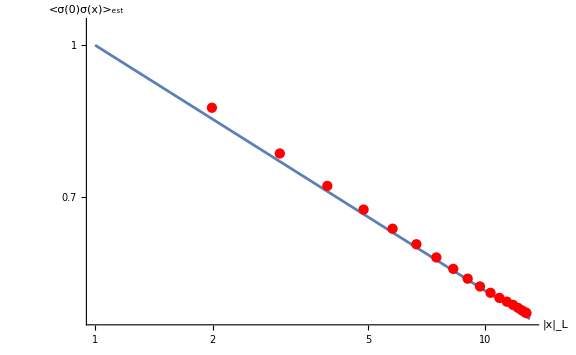

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0,1.05}},AxesLabel->{"|x|_L","<σ(0)σ(x)>_est"}],ListLogLogPlot[data$temp[[2;;20]],(*draw error bars*)IntervalMarkersStyle->Automatic,PlotRange->All,AxesLabel->{"x","y"},PlotStyle->Red],AxesStyle->Large,ImageSize->Large]
```

```mathematica
Export["fig-sigma-sigma-sample-10e4.pdf",g]
```

fig-sigma-sigma-sample-10e4.pdf

### Sample ⟨σσϵ⟩

#### sample size 10^4

```mathematica
measure0(*sample size 10^4*)={{{0.12448758000023129,0.0005492731777114875},{0.1091562347501945,0.0005127500243613351},{0.10322119000014951,0.00046216995377198507},{0.10309553125013417,0.00047804776724102814},{0.10022663325012392,0.0004715468404660588},{0.09930000950011697,0.0004772453263131212},{0.09781781750011154,0.00047407829163013027},{0.09584399425010745,0.000477232825222227},{0.09386892425010418,0.0004763136298491982},{0.09250177200010133,0.0004777414400098029},{0.09141949800009888,0.00047709021012448297},{0.09087149225009676,0.00047829889818837507},{0.09033581050009493,0.00047716273756364687},{0.08979312250009379,0.00047857988864739013},{0.08989335225009297,0.00047757044136108155},{0.09040126925009218,0.000478534820152826},{0.0905818437500916,0.00047798926460283135},{0.0905940345000913,0.0004780822527429468},{0.09068554475009125,0.00047800814875681024},{0.09104324800009123,0.00047822185620408466},{0.09135885800009114,0.0004775582637830621},{0.09137324800009111,0.00047777332639113213},{0.09158429475009136,0.00047790638054802647},{0.09240653450009158,0.00047810287308186256},{0.09376934375009181,0.00047670754599493496},{0.09511251925009229,0.00047726659410646146},{0.09686335225009315,0.00047551993646971903},{0.09939062250009435,0.0004762358240963874},{0.10206206050009584,0.0004744254493686252},{0.10534899225009758,0.00047427302185443964},{0.10922324800009985,0.00047203925954763946},{0.11294677200010256,0.0004723808457240382},{0.11799892425010565,0.0004685523505511602},{0.12567149425010926,0.0004690159199960388},{0.13580781750011367,0.0004599208100036395},{0.1506775095001196,0.00046056205209037935},{0.17554663325012748,0.00043427416025481713},{0.2648680312501392,0.00041186273335110384},{0.31734619000015546,0.00037283813613133934}},{{0.1091562347501945,0.0005127500243613351},{0.05371383000021856,0.0005548642710944672},{0.04968373475018264,0.0004908596204656816},{0.05722119000014263,0.0004783817998812912},{0.059520531250128295,0.00047476436393296983},{0.060957883250119284,0.0004774507520959546},{0.06184000950011291,0.0004750758501731345},{0.06169031750010769,0.00047629745306251766},{0.061043994250103636,0.0004758175198119083},{0.06058392425010048,0.0004766188473726008},{0.060194272000097734,0.0004761167421120559},{0.06025949800009519,0.000476872718454716},{0.060397742250093214,0.0004757193880478624},{0.06038081050009191,0.00047668739353595865},{0.06068687250009104,0.000476064108151209},{0.06135460225009017,0.00047663624572032544},{0.061931269250089314,0.00047624250383088113},{0.06216684375008884,0.0004761821787588357},{0.062315284500088636,0.0004761418218540573},{0.06282179475008862,0.0004765322374886025},{0.06319449800008858,0.0004758696058749947},{0.06323635800008848,0.00047588209754681867},{0.06335824800008868,0.0004759262701920384},{0.06392429475008894,0.0004764342970649545},{0.06512778450008903,0.0004752115175073874},{0.0663768437500891,0.00047575656007732434},{0.06792376925008954,0.0004745951288675843},{0.07010210225009061,0.0004750660981286524},{0.07248062250009203,0.0004738371800338938},{0.07522206050009368,0.00047381170684364593},{0.07845649225009564,0.0004722460984251903},{0.08165074800009783,0.00047252256527637835},{0.08565302200010062,0.00046991840619368117},{0.09177142425010429,0.0004710099107105776},{0.1004927442501081,0.00046415281238879616},{0.11310906750011267,0.00046541260210038947},{0.13455375950011916,0.00044510460706645514},{0.20637413325012818,0.0004412531249052352},{0.2648680312501392,0.0004118627333511024}},{{0.10322119000014951,0.00046216995377198507},{0.04968373475018264,0.0004908596204656816},{0.01057508000011788,0.0005319378406096167},{0.013854984750129076,0.0004943944265914871},{0.018736190000110654,0.0004544375439734007},{0.021626781250103505,0.00046197712166255397},{0.023524133250099718,0.00045668401969910265},{0.024536259500095303,0.00045950867739460354},{0.025204067500091448,0.0004567680002152962},{0.025665244250088905,0.00045858124940530615},{0.025920174250087066,0.00045741920160383983},{0.02622052200008471,0.00045837387097275213},{0.026716998000082495,0.0004570292157934885},{0.027021492250080527,0.0004579624607020271},{0.02739331050007979,0.00045729297519317153},{0.02797812250007913,0.00045832753693375686},{0.028549602250078524,0.0004576531325423425},{0.029003769250078443,0.0004578619500912002},{0.029324343750078447,0.00045756638703602087},{0.02986653450007876,0.00045801746313945925},{0.03029179475007957,0.0004577464523456499},{0.030238248000079845,0.0004574931290048705},{0.0302026080000797,0.0004572392329374313},{0.03044324800007918,0.0004577383176919149},{0.031015544750078967,0.0004573925474187382},{0.031952784500079004,0.0004579671718349278},{0.03308684375007941,0.00045692671001107155},{0.034567519250081,0.0004576172002114357},{0.03614710225008252,0.000456494778873292},{0.0379768725000843,0.0004569704563636614},{0.0401995605000866,0.0004556889251570535},{0.042292742250088604,0.00045637222009500665},{0.04483199800009148,0.00045453998852826966},{0.04877052200009543,0.00045605968333647685},{0.05437392425009989,0.0004519858991206667},{0.0632052442501045,0.00045421023245496546},{0.07812531750011022,0.00044064396537789183},{0.1345537595001192,0.00044510460706645314},{0.17554663325012754,0.0004342741602548144}},{{0.10309553125013417,0.00047804776724102814},{0.05722119000014263,0.0004783817998812912},{0.013854984750129076,0.0004943944265914871},{0.006818830000024212,0.0005439792224855433},{0.008108734750061247,0.0004948766822210064},{0.011713690000082594,0.00046963348132256786},{0.013916781250084491,0.00047011846672897025},{0.015127883250083282,0.00046951659076912715},{0.01613625950008166,0.0004690148860452401},{0.01692031750007975,0.00046869779106875723},{0.017567744250078763,0.00046868965590479846},{0.017971424250077164,0.00046908123922624606},{0.01844927200007502,0.0004681812568933083},{0.018838248000073644,0.0004688744246652176},{0.019113992250072712,0.00046846305070215793},{0.01972706050007207,0.00046890080530674903},{0.02028312250007147,0.0004687353675259632},{0.020938352250071603,0.0004685060762373797},{0.021401269250071804,0.0004686708294353954},{0.02179434375007226,0.0004687197368689347},{0.02232528450007323,0.0004685660736626457},{0.022398044750074033,0.00046855538011587904},{0.022266998000073535,0.00046832322263703124},{0.02239385800007267,0.00046858317073326955},{0.022704498000072525,0.0004680985091938427},{0.023421794750071685,0.00046897717824856595},{0.024507784500072235,0.0004681035077895624},{0.025778093750074785,0.000468572427433466},{0.027160019250076634,0.00046785308358788277},{0.028685852250077987,0.0004679287815879662},{0.030720622500080112,0.000467155752600277},{0.03267206050008217,0.00046782145103931326},{0.0347264922500846,0.00046611258717649213},{0.037731998000088425,0.0004677924453371231},{0.0423455220000935,0.00046373217479535995},{0.05016142425009874,0.00046674557056773484},{0.06320524425010432,0.00045421023245496546},{0.11310906750011283,0.0004654126021003878},{0.1506775095001196,0.0004605620520903832}},{{0.10022663325012392,0.0004715468404660588},{0.059520531250128295,0.00047476436393296983},{0.018736190000110654,0.0004544375439734007},{0.008108734750061247,0.0004948766822210064},{0.0037000799999862,0.0005393318408767414},{0.005249984749977381,0.0004983534393711434},{0.0077736900000473915,0.00046313570991432686},{0.009261781250050768,0.00046828238968796027},{0.010234133250056753,0.0004646184701554484},{0.011087509500062298,0.0004661146086373155},{0.01199531750006262,0.00046416741356944847},{0.012683994250064525,0.00046566153439163096},{0.013135174250064044,0.0004642746523428659},{0.013565522000063718,0.00046544318583117874},{0.013928248000063512,0.000464592475156808},{0.014471492250062983,0.0004654184799301988},{0.015155810500063205,0.000464886999709668},{0.01588437250006496,0.0004648995183846011},{0.016485852250065932,0.00046456389007326295},{0.016830019250066584,0.00046507943174761305},{0.01706434375006697,0.0004646950199038582},{0.017171534500067646,0.0004649497693504554},{0.017269294750067762,0.00046502908876001284},{0.01741949800006687,0.0004650846992142888},{0.017721358000065836,0.00046423839930081166},{0.01822949800006632,0.00046501607593511703},{0.019100544750067082,0.0004644798222014158},{0.020266534500068323,0.00046510552127558335},{0.02165184375007075,0.0004639834473736933},{0.02317001925007326,0.0004645258698487728},{0.024828352250076176,0.0004636008725489406},{0.026726872500078224,0.0004645386414175648},{0.028687060500079888,0.0004625515379893003},{0.031148992250082917,0.00046434813117979246},{0.0350807480000878,0.0004599783477576408},{0.04234552200009382,0.00046373217479536304},{0.054373924250099744,0.0004519858991206659},{0.10049274425010796,0.00046415281238879817},{0.1358078175001136,0.00045992081000364267}},{{0.09930000950011697,0.0004772453263131212},{0.060957883250119284,0.0004774507520959546},{0.021626781250103505,0.00046197712166255397},{0.011713690000082594,0.00046963348132256786},{0.005249984749977381,0.0004983534393711434},{0.002681330000025867,0.0005436489499794572},{0.0036562347499882407,0.0004971596445992691},{0.0055936900000087475,0.0004688939984058982},{0.006721781250021962,0.0004709251876943248},{0.007569133250033966,0.0004691107593753654},{0.008590009500043348,0.00046911778521218766},{0.00943906750005005,0.00046864799334421666},{0.00989899425004946,0.0004683766651250711},{0.010211424250048815,0.0004689772289297733},{0.010610522000049145,0.00046857313933494247},{0.011220748000053172,0.00046893318799143415},{0.011910242250054255,0.00046880474786702744},{0.012597060500055329,0.00046861915226041926},{0.013250622500056507,0.0004686244042067869},{0.013664602250057353,0.00046878202094051473},{0.013883769250057593,0.0004688194995276819},{0.013840593750057886,0.00046864292170106916},{0.013899034500058464,0.00046878517326169323},{0.014178044750058743,0.0004692815020440986},{0.014436998000057715,0.0004682844720871887},{0.014853858000059183,0.0004686016013213433},{0.015550748000062876,0.000468048463859953},{0.01660679475006511,0.00046896853546410703},{0.017922784500066236,0.00046796916081121254},{0.019518093750068247,0.00046833649522944146},{0.02120126925007089,0.0004676763225919782},{0.02278835225007355,0.0004682210243379368},{0.02470312250007589,0.0004666105832596617},{0.0273808105000791,0.00046816285876795035},{0.03114899225008351,0.0004643481311797978},{0.03773199800008974,0.0004677924453371225},{0.04877052200009601,0.00045605968333647213},{0.09177142425010426,0.00047100991071057714},{0.12567149425010926,0.0004690159199960344}},{{0.09781781750011154,0.00047407829163013027},{0.06184000950011291,0.0004750758501731345},{0.023524133250099718,0.00045668401969910265},{0.013916781250084491,0.00047011846672897025},{0.0077736900000473915,0.00046313570991432686},{0.0036562347499882407,0.0004971596445992691},{0.001945080000023725,0.0005413132019249627},{0.0028674847500047723,0.0004992614228832233},{0.004391189999990058,0.0004660403792128932},{0.0055380312499955855,0.00046994667091869463},{0.006432883250016374,0.00046648264334362316},{0.007328759500034057,0.0004679472170057071},{0.007895317500035958,0.0004658467323385565},{0.008093994250035182,0.00046739361927830526},{0.008398924250035321,0.0004663272379491604},{0.008990522000037294,0.00046710353555016424},{0.009634498000039137,0.0004666544493695752},{0.010213992250041166,0.0004668623264223274},{0.010845810500045782,0.00046655333301422105},{0.0114018725000499,0.0004669900210306128},{0.011850852250051993,0.00046645041503868374},{0.011978769250052717,0.00046683388679542496},{0.011805593750052901,0.00046661994846638555},{0.011866534500052782,0.0004671766514779287},{0.012190544750052684,0.0004664311322831024},{0.012621998000055309,0.00046675615299599286},{0.013226358000057411,0.0004657932515317328},{0.01412324800005945,0.00046679526638653614},{0.015325544750061629,0.00046622052091008584},{0.016991534500064805,0.00046655057169817294},{0.018821843750067457,0.00046569779924697996},{0.020385019250069716,0.00046672677746221396},{0.022010852250072203,0.00046479073555518265},{0.024703122500075832,0.00046661058325966475},{0.02868706050008073,0.0004625515379893036},{0.03472649225008665,0.00046611258717649425},{0.0448319980000928,0.00045453998852827644},{0.08565302200010097,0.00046991840619366854},{0.11799892425010573,0.0004685523505511638}},{{0.09584399425010745,0.000477232825222227},{0.06169031750010769,0.00047629745306251766},{0.024536259500095303,0.00045950867739460354},{0.015127883250083282,0.00046951659076912715},{0.009261781250050768,0.00046828238968796027},{0.0055936900000087475,0.0004688939984058982},{0.0028674847500047723,0.0004992614228832233},{0.0017213300000234583,0.000543208637090141},{0.0024374847500277397,0.000498111720265731},{0.0039836899999916055,0.00046841098543834},{0.0050330312499834865,0.00047075677697382926},{0.005819133250004875,0.0004690436860680304},{0.006513759500010815,0.0004688342488375362},{0.006922817500017421,0.00046835866718762203},{0.0072464942500202485,0.00046840898300236876},{0.007685174250027249,0.0004686442376973645},{0.00817427200003043,0.00046859986896145194},{0.008530748000033523,0.0004684275836365271},{0.009047742250035832,0.00046833161006026023},{0.009557060500038243,0.00046850632308233805},{0.010046872500041161,0.00046835552684847993},{0.010343352250044884,0.00046828427627741015},{0.010288769250046398,0.00046853209537350073},{0.010149343750045307,0.0004687187577896386},{0.010326534500045188,0.00046806609189852736},{0.010961794750049143,0.00046867319399205285},{0.011684498000053134,0.0004676655679799446},{0.012348858000056284,0.0004685123341916461},{0.013349498000057117,0.0004677568181758192},{0.014873044750059699,0.00046848178229052866},{0.01682778450006418,0.0004678401985848465},{0.018821843750067634,0.0004684293653135309},{0.020385019250069653,0.00046672677746221515},{0.022788352250072894,0.0004682210243379365},{0.026726872500078172,0.00046453864141756475},{0.03267206050008452,0.00046782145103930713},{0.042292742250090165,0.00045637222009501185},{0.08165074800009822,0.0004725225652763836},{0.11294677200010256,0.0004723808457240454}},{{0.09386892425010418,0.0004763136298491982},{0.061043994250103636,0.0004758175198119083},{0.025204067500091448,0.0004567680002152962},{0.01613625950008166,0.0004690148860452401},{0.010234133250056753,0.0004646184701554484},{0.006721781250021962,0.0004709251876943248},{0.004391189999990058,0.0004660403792128932},{0.0024374847500277397,0.000498111720265731},{0.0014775800000119694,0.0005421852815215188},{0.002253734750021676,0.0004993500903552039},{0.0035436900000045115,0.00046691463308406555},{0.004401781249990818,0.0004707987985454223},{0.005114133249983926,0.0004671306485018086},{0.005717509499995977,0.0004685889963132966},{0.006042817500006615,0.0004668797828164754},{0.006418994250013812,0.00046826895563011983},{0.006756424250016747,0.0004676407651285637},{0.006919272000017962,0.00046779426086206735},{0.007303248000023253,0.0004672910917653489},{0.007820242250029048,0.0004678373215866743},{0.008198310500034143,0.00046729017221220184},{0.008369372500036807,0.00046758533466191566},{0.008468352250037116,0.0004675839684228121},{0.008500019250036711,0.0004680088543796354},{0.008551843750037013,0.00046714998836261656},{0.009164034500041966,0.00046796768825545796},{0.010066794750047991,0.0004669857093973059},{0.01077199800004958,0.0004677960225273266},{0.011593858000050729,0.0004667588382151609},{0.01289449800005457,0.0004674540679231493},{0.014734294750059223,0.0004669618013223737},{0.016827784500064332,0.00046784019858485035},{0.018821843750067863,0.00046569779924698034},{0.021201269250071337,0.0004676763225919746},{0.02482835225007566,0.00046360087254893804},{0.030720622500082277,0.0004671557526002833},{0.04019956050008809,0.0004556889251570536},{0.0784564922500959,0.00047224609842518527},{0.10922324800009992,0.00047203925954763593}},{{0.09250177200010133,0.0004777414400098029},{0.06058392425010048,0.0004766188473726008},{0.025665244250088905,0.00045858124940530615},{0.01692031750007975,0.00046869779106875723},{0.011087509500062298,0.0004661146086373155},{0.007569133250033966,0.0004691107593753654},{0.0055380312499955855,0.00046994667091869463},{0.0039836899999916055,0.00046841098543834},{0.002253734750021676,0.0004993500903552039},{0.0012488299999976649,0.0005430654627584747},{0.001746234750010474,0.0004983731379457785},{0.00280869000001659,0.0004684260188167015},{0.0036892812500052934,0.00047037312642908194},{0.004320383249991936,0.0004686027475222357},{0.004626259499988443,0.00046876359316948106},{0.004999067499987243,0.0004684029727751281},{0.00524149424999365,0.00046886213875916866},{0.00526267424999303,0.00046844454674455907},{0.005660522000000303,0.00046846164342180096},{0.006229498000010969,0.0004685219121653875},{0.0066264922500175434,0.0004682451087481738},{0.00683706050002392,0.0004681371767140429},{0.006816872500020921,0.0004684868209741122},{0.006838352250017958,0.00046851862199144713},{0.007006269250017335,0.00046804942050484384},{0.007488093750028538,0.00046849027576522354},{0.008297784500034015,0.00046778252516026914},{0.009166794750040124,0.00046852979681116986},{0.010093248000044708,0.0004675790157629207},{0.011355108000047156,0.00046797871666002627},{0.012894498000050403,0.0004674540679231493},{0.014873044750058835,0.0004684817822905247},{0.016991534500064576,0.000466550571698177},{0.019518093750068733,0.0004683364952294362},{0.023170019250073382,0.0004645258698487708},{0.028685852250079812,0.0004679287815879644},{0.03797687250008612,0.00045697045636366085},{0.07522206050009386,0.0004738117068436468},{0.10534899225009765,0.0004742730218544471}},{{0.09141949800009888,0.00047709021012448297},{0.060194272000097734,0.0004761167421120559},{0.025920174250087066,0.00045741920160383983},{0.017567744250078763,0.00046868965590479846},{0.01199531750006262,0.00046416741356944847},{0.008590009500043348,0.00046911778521218766},{0.006432883250016374,0.00046648264334362316},{0.0050330312499834865,0.00047075677697382926},{0.0035436900000045115,0.00046691463308406555},{0.001746234750010474,0.0004983731379457785},{0.0007863299999905448,0.0005424901791831602},{0.0012524847499915035,0.0004996538624951888},{0.0022711900000160963,0.0004669182872953701},{0.003024281250012912,0.00047078497063230627},{0.003442883250003676,0.00046764847556911423},{0.0038800094999945156,0.00046906226779923647},{0.004204067499993013,0.00046759687453891196},{0.004121494249992616,0.00046818028449889147},{0.0043889242499906105,0.00046778906560183335},{0.005101771999989444,0.00046838187904541396},{0.005530747999997616,0.00046762080006560207},{0.00580149224999967,0.0004679865420614604},{0.005898310500004751,0.00046789083906575285},{0.005771872499997105,0.00046832648498276687},{0.00586960224999865,0.0004673141037831436},{0.006292519250007257,0.000468137308077491},{0.0069255937500167656,0.0004672364930043256},{0.007640284500028156,0.00046802344784270403},{0.008631794750032076,0.00046708728747233514},{0.010093248000040187,0.000467579015762925},{0.011593858000043294,0.0004667588382151582},{0.013349498000052704,0.00046775681817581795},{0.015325544750060179,0.0004662205209100889},{0.01792278450006578,0.00046796916081121227},{0.021651843750071342,0.00046398344737369924},{0.027160019250076908,0.0004678530835878854},{0.03614710225008378,0.00045649477887329},{0.07248062250009212,0.00047383718003388907},{0.10206206050009567,0.000474425449368631}},{{0.09087149225009676,0.00047829889818837507},{0.06025949800009519,0.000476872718454716},{0.02622052200008471,0.00045837387097275213},{0.017971424250077164,0.00046908123922624606},{0.012683994250064525,0.00046566153439163096},{0.00943906750005005,0.00046864799334421666},{0.007328759500034057,0.0004679472170057071},{0.005819133250004875,0.0004690436860680304},{0.004401781249990818,0.0004707987985454223},{0.00280869000001659,0.0004684260188167015},{0.0012524847499915035,0.0004996538624951888},{0.0006163299999911586,0.0005433281938313846},{0.001117484749991203,0.0004986321261368687},{0.00188119000000688,0.0004687477729942775},{0.002440531250021789,0.0004708952003854034},{0.002901633250010173,0.00046914229515425225},{0.003342509500004406,0.0004695935429477468},{0.003546567499998532,0.00046819245743612384},{0.003688994249993193,0.00046890669281646815},{0.0043801742499903025,0.00046889842775423685},{0.004973021999989006,0.0004687681675628681},{0.005211997999988419,0.00046848669996287873},{0.005453992249988794,0.0004686911466814843},{0.005539560499990208,0.0004687443762481595},{0.005503122499990046,0.0004681524504243051},{0.005705852249999325,0.0004687371869421657},{0.006246269250008222,0.00046796429802072444},{0.006781843750013842,0.0004686608953249047},{0.0076402845000203366,0.000468023447842698},{0.009166794750032913,0.0004685297968111564},{0.01077199800003955,0.0004677960225273194},{0.012348858000047357,0.0004685123341916441},{0.0141232480000571,0.00046679526638653815},{0.01660679475006412,0.0004689685354641063},{0.020266534500068538,0.00046510552127558357},{0.025778093750075417,0.00046857242743346156},{0.03456751925008188,0.00045761720021143825},{0.07010210225009102,0.00047506609812864687},{0.09939062250009423,0.00047623582409638557}},{{0.09033581050009493,0.00047716273756364687},{0.060397742250093214,0.0004757193880478624},{0.026716998000082495,0.0004570292157934885},{0.01844927200007502,0.0004681812568933083},{0.013135174250064044,0.0004642746523428659},{0.00989899425004946,0.0004683766651250711},{0.007895317500035958,0.0004658467323385565},{0.006513759500010815,0.0004688342488375362},{0.005114133249983926,0.0004671306485018086},{0.0036892812500052934,0.00047037312642908194},{0.0022711900000160963,0.0004669182872953701},{0.001117484749991203,0.0004986321261368687},{0.0007050799999897101,0.0005422917864507188},{0.0010137347499913092,0.0004995022447447587},{0.0016786900000046268,0.0004670063349347436},{0.0022792812500152444,0.00047075168345480983},{0.0026503832500167084,0.00046797381614875275},{0.002987509500007726,0.0004686546192760955},{0.0033690674999954577,0.00046736208060489383},{0.003842744249991218,0.00046818431576558557},{0.0043451742499889335,0.0004675663864329665},{0.004684271999986482,0.00046765060633155783},{0.004868247999984997,0.00046758369828771507},{0.005105242249984581,0.00046808902465275654},{0.005213310499987902,0.0004671387736587897},{0.005320622499990802,0.0004681031894256956},{0.005743352250002842,0.0004667073749894697},{0.006246269250009599,0.0004679642980207259},{0.006925593750014152,0.0004672364930043248},{0.008297784500028202,0.00046778252516027895},{0.01006679475003766,0.00046698570939729736},{0.011684498000043023,0.0004676655679799372},{0.013226358000052117,0.00046579325153174453},{0.015550748000060446,0.00046804846385995694},{0.019100544750066534,0.000464479822201418},{0.024507784500074098,0.00046810350778956597},{0.033086843750081064,0.000456926710011076},{0.06792376925009003,0.0004745951288675896},{0.0968633522500931,0.00047551993646972076}},{{0.08979312250009379,0.00047857988864739013},{0.06038081050009191,0.00047668739353595865},{0.027021492250080527,0.0004579624607020271},{0.018838248000073644,0.0004688744246652176},{0.013565522000063718,0.00046544318583117874},{0.010211424250048815,0.0004689772289297733},{0.008093994250035182,0.00046739361927830526},{0.006922817500017421,0.00046835866718762203},{0.005717509499995977,0.0004685889963132966},{0.004320383249991936,0.0004686027475222357},{0.003024281250012912,0.00047078497063230627},{0.00188119000000688,0.0004687477729942775},{0.0010137347499913092,0.0004995022447447587},{0.0006988299999921542,0.0005432991106864596},{0.0010162347499930557,0.0004990047080608194},{0.0015486900000044946,0.00046866543184641654},{0.0019342812500143932,0.0004712624715058702},{0.002329133250017313,0.0004686795049160116},{0.002867509500009528,0.0004691707282818739},{0.0033865674999990717,0.00046841338082623685},{0.0036677442499920524,0.0004687082450038774},{0.00397142424999022,0.0004684193826767212},{0.004301771999989916,0.0004688829324818278},{0.004560747999987958,0.00046864365370934575},{0.004808992249986325,0.000468347272443963},{0.005033310499986513,0.00046913853610436616},{0.0053206224999909285,0.0004681031894256984},{0.00570585225000523,0.000468737186942166},{0.006292519250010589,0.0004681373080774947},{0.007488093750020349,0.00046849027576521986},{0.009164034500032756,0.0004679676882554559},{0.010961794750041814,0.0004686731939920357},{0.012621998000050594,0.0004667561529959968},{0.014853858000058487,0.0004686016013213301},{0.018229498000065784,0.00046501607593511275},{0.023421794750072004,0.00046897717824856275},{0.03195278450007958,0.00045796717183492914},{0.06637684375008931,0.00047575656007732347},{0.09511251925009218,0.0004772665941064638}},{{0.08989335225009297,0.00047757044136108155},{0.06068687250009104,0.000476064108151209},{0.02739331050007979,0.00045729297519317153},{0.019113992250072712,0.00046846305070215793},{0.013928248000063512,0.000464592475156808},{0.010610522000049145,0.00046857313933494247},{0.008398924250035321,0.0004663272379491604},{0.0072464942500202485,0.00046840898300236876},{0.006042817500006615,0.0004668797828164754},{0.004626259499988443,0.00046876359316948106},{0.003442883250003676,0.00046764847556911423},{0.002440531250021789,0.0004708952003854034},{0.0016786900000046268,0.0004670063349347436},{0.0010162347499930557,0.0004990047080608194},{0.000590079999993861,0.0005425935536741766},{0.0007449847499946147,0.0004995778067354639},{0.0009736899999953973,0.000467664509876355},{0.0014767812500040506,0.00047082892367397033},{0.002169133250018071,0.0004681716958123676},{0.002731259500016374,0.00046917862524970303},{0.0032403175000005903,0.00046737452089772285},{0.003483994249992851,0.0004681866121555872},{0.003822674249991989,0.000467934083397156},{0.004311771999991255,0.00046835445493692286},{0.004590747999987766,0.0004675574139475186},{0.004808992249986506,0.0004683472724439624},{0.005213310499991029,0.00046713877365879217},{0.005503122500001976,0.0004681524504243067},{0.005869602250007098,0.00046731410378314503},{0.007006269250018696,0.00046804942050484454},{0.00855184375003114,0.0004671499883624833},{0.010326534500041541,0.0004680660918985247},{0.01219054475004998,0.00046643113228310684},{0.014436998000056933,0.00046828447208718154},{0.017721358000064913,0.00046423839930081963},{0.02270449800007119,0.0004680985091938425},{0.031015544750077825,0.000457392547418732},{0.06512778450008896,0.00047521151750738836},{0.09376934375009159,0.00047670754599492965}},{{0.09040126925009218,0.000478534820152826},{0.06135460225009017,0.00047663624572032544},{0.02797812250007913,0.00045832753693375686},{0.01972706050007207,0.00046890080530674903},{0.014471492250062983,0.0004654184799301988},{0.011220748000053172,0.00046893318799143415},{0.008990522000037294,0.00046710353555016424},{0.007685174250027249,0.0004686442376973645},{0.006418994250013812,0.00046826895563011983},{0.004999067499987243,0.0004684029727751281},{0.0038800094999945156,0.00046906226779923647},{0.002901633250010173,0.00046914229515425225},{0.0022792812500152444,0.00047075168345480983},{0.0015486900000044946,0.00046866543184641654},{0.0007449847499946147,0.0004995778067354639},{0.0005475799999963282,0.0005434094477581527},{0.0005474847499984817,0.0004996868692703564},{0.0009336899999960165,0.0004685496734110616},{0.0017517812500152852,0.00047148871017465926},{0.002380383250017331,0.0004691934149819482},{0.0027825095000121483,0.0004693124854604149},{0.003224067499999879,0.00046821290537821936},{0.003537744249993324,0.0004691076678612723},{0.0038764242499932807,0.0004692164948725874},{0.004311771999990452,0.00046835445493692275},{0.004560747999988536,0.00046864365370935057},{0.005105242249988361,0.00046808902465275817},{0.005539560500004542,0.0004687443762481599},{0.005771872500007447,0.0004683264849827661},{0.006838352250016677,0.00046851862199144973},{0.008500019250031708,0.00046800885437963595},{0.010149343750040334,0.00046871875778963526},{0.01186653450004751,0.0004671766514779285},{0.01417804475005499,0.00046928150204410154},{0.017419498000063736,0.0004650846992142839},{0.0223938580000717,0.00046858317073327545},{0.030443248000078166,0.00045773831769190654},{0.06392429475008882,0.0004764342970649567},{0.0924065345000915,0.00047810287308186673}},{{0.0905818437500916,0.00047798926460283135},{0.061931269250089314,0.00047624250383088113},{0.028549602250078524,0.0004576531325423425},{0.02028312250007147,0.0004687353675259632},{0.015155810500063205,0.000464886999709668},{0.011910242250054255,0.00046880474786702744},{0.009634498000039137,0.0004666544493695752},{0.00817427200003043,0.00046859986896145194},{0.006756424250016747,0.0004676407651285637},{0.00524149424999365,0.00046886213875916866},{0.004204067499993013,0.00046759687453891196},{0.003342509500004406,0.0004695935429477468},{0.0026503832500167084,0.00046797381614875275},{0.0019342812500143932,0.0004712624715058702},{0.0009736899999953973,0.000467664509876355},{0.0005474847499984817,0.0004996868692703564},{0.000547579999995548,0.0005430441532847191},{0.0007512347499970417,0.0004994528941262523},{0.001356190000010146,0.00046802763032492695},{0.0020942812500158742,0.0004714451310100668},{0.0024903832500186335,0.00046852963303107935},{0.00275500950001334,0.00046902699312343716},{0.0032478174999991966,0.00046780553047193093},{0.003537744249998705,0.0004691076678612793},{0.003822674249997723,0.0004679340833971601},{0.004301771999989974,0.0004688829324818294},{0.004868247999990874,0.00046758369828707425},{0.005453992250004893,0.0004686911466814885},{0.005898310500011305,0.00046789083906575307},{0.006816872500015814,0.00046848682097410874},{0.00846835225003047,0.00046758396842282423},{0.01028876925004009,0.0004685320953735083},{0.011805593750046695,0.00046661994846638755},{0.013899034500053021,0.00046878517326169806},{0.017269294750063398,0.000465029088759996},{0.022266998000071352,0.0004683232226370354},{0.030202608000078904,0.00045723923293742685},{0.06335824800008875,0.0004759262701920377},{0.09158429475009143,0.00047790638054803335}},{{0.0905940345000913,0.0004780822527429468},{0.06216684375008884,0.0004761821787588357},{0.029003769250078443,0.0004578619500912002},{0.020938352250071603,0.0004685060762373797},{0.01588437250006496,0.0004648995183846011},{0.012597060500055329,0.00046861915226041926},{0.010213992250041166,0.0004668623264223274},{0.008530748000033523,0.0004684275836365271},{0.006919272000017962,0.00046779426086206735},{0.00526267424999303,0.00046844454674455907},{0.004121494249992616,0.00046818028449889147},{0.003546567499998532,0.00046819245743612384},{0.002987509500007726,0.0004686546192760955},{0.002329133250017313,0.0004686795049160116},{0.0014767812500040506,0.00047082892367397033},{0.0009336899999960165,0.0004685496734110616},{0.0007512347499970417,0.0004994528941262523},{0.0006375799999945159,0.0005430095455276777},{0.0007849847499943382,0.000499137949801935},{0.0012286899999980562,0.000468299017086062},{0.001960531250013918,0.00047112851819300946},{0.0024016332500145813,0.00046857221505728193},{0.0027550095000099624,0.00046902699312343233},{0.0032240674999986937,0.00046821290537821995},{0.0034839942499972714,0.00046818661215558696},{0.003971424249991838,0.00046841938267672405},{0.0046842719999918535,0.00046765060633156575},{0.005211997999995857,0.0004684866999628889},{0.005801492250011296,0.0004679865420614242},{0.006837060500017421,0.00046813717671404203},{0.008369372500029988,0.0004675853346619137},{0.010343352250042457,0.00046828427627741237},{0.01197876925004844,0.0004668338867954325},{0.013840593750053849,0.0004686429217010801},{0.017171534500063736,0.0004649497693504518},{0.022398044750072153,0.0004685553801158789},{0.03023824800007954,0.0004574931290048765},{0.06323635800008888,0.0004758820975468277},{0.09137324800009128,0.00047777332639113235}},{{0.09068554475009125,0.00047800814875681024},{0.062315284500088636,0.0004761418218540573},{0.029324343750078447,0.00045756638703602087},{0.021401269250071804,0.0004686708294353954},{0.016485852250065932,0.00046456389007326295},{0.013250622500056507,0.0004686244042067869},{0.010845810500045782,0.00046655333301422105},{0.009047742250035832,0.00046833161006026023},{0.007303248000023253,0.0004672910917653489},{0.005660522000000303,0.00046846164342180096},{0.0043889242499906105,0.00046778906560183335},{0.003688994249993193,0.00046890669281646815},{0.0033690674999954577,0.00046736208060489383},{0.002867509500009528,0.0004691707282818739},{0.002169133250018071,0.0004681716958123676},{0.0017517812500152852,0.00047148871017465926},{0.001356190000010146,0.00046802763032492695},{0.0007849847499943382,0.000499137949801935},{0.0004238299999937655,0.0005429453152533717},{0.0003887347499976979,0.0004995532323985115},{0.0009461899999935827,0.00046788390191941144},{0.0019605312500123795,0.00047112851819300594},{0.002490383250014386,0.0004685296330310787},{0.002782509500009079,0.0004693124854604132},{0.003240317499998697,0.0004673745208977179},{0.0036677442499977015,0.0004687082450038841},{0.004345174249994081,0.00046756638643297025},{0.004973021999990407,0.0004687681675628792},{0.005530748000004135,0.0004676208000656072},{0.006626492250016902,0.00046824510874817247},{0.008198310500030628,0.0004672901722122057},{0.010046872500042343,0.000468355526848484},{0.011850852250049063,0.00046645041503869583},{0.013883769250055878,0.0004688194995276844},{0.017064343750065342,0.0004646950199038507},{0.022325284500073306,0.0004685660736626413},{0.030291794750080068,0.0004577464523456466},{0.06319449800008911,0.00047586960587500324},{0.0913588580000912,0.00047755826378306234}},{{0.09104324800009123,0.00047822185620408466},{0.06282179475008862,0.0004765322374886025},{0.02986653450007876,0.00045801746313945925},{0.02179434375007226,0.0004687197368689347},{0.016830019250066584,0.00046507943174761305},{0.013664602250057353,0.00046878202094051473},{0.0114018725000499,0.0004669900210306128},{0.009557060500038243,0.00046850632308233805},{0.007820242250029048,0.0004678373215866743},{0.006229498000010969,0.0004685219121653875},{0.005101771999989444,0.00046838187904541396},{0.0043801742499903025,0.00046889842775423685},{0.003842744249991218,0.00046818431576558557},{0.0033865674999990717,0.00046841338082623685},{0.002731259500016374,0.00046917862524970303},{0.002380383250017331,0.0004691934149819482},{0.0020942812500158742,0.0004714451310100668},{0.0012286899999980562,0.000468299017086062},{0.0003887347499976979,0.0004995532323985115},{0.00011757999999905295,0.000768392831630313},{0.0003887347499956563,0.000499553232398509},{0.001228689999993365,0.0004682990170860627},{0.0020942812500129343,0.00047144513101006426},{0.0023803832500127165,0.00046919341498194634},{0.0027312595000067177,0.00046917862524969913},{0.003386567499997637,0.00046841338082623745},{0.0038427442499976592,0.0004681843157655879},{0.004380174249995176,0.0004688984277542424},{0.005101771999988949,0.0004683818790454193},{0.006229498000013798,0.000468521912165394},{0.007820242250028543,0.0004678373215866775},{0.00955706050004101,0.0004685063230823346},{0.011401872500048323,0.0004669900210306062},{0.013664602250056094,0.00046878202094051543},{0.016830019250065636,0.0004650794317476153},{0.02179434375007329,0.0004687197368689326},{0.029866534500079988,0.00045801746313945687},{0.06282179475008896,0.0004765322374886008},{0.09104324800009128,0.00047822185620408536}},{{0.09135885800009114,0.0004775582637830621},{0.06319449800008858,0.0004758696058749947},{0.03029179475007957,0.0004577464523456499},{0.02232528450007323,0.0004685660736626457},{0.01706434375006697,0.0004646950199038582},{0.013883769250057593,0.0004688194995276819},{0.011850852250051993,0.00046645041503868374},{0.010046872500041161,0.00046835552684847993},{0.008198310500034143,0.00046729017221220184},{0.0066264922500175434,0.0004682451087481738},{0.005530747999997616,0.00046762080006560207},{0.004973021999989006,0.0004687681675628681},{0.0043451742499889335,0.0004675663864329665},{0.0036677442499920524,0.0004687082450038774},{0.0032403175000005903,0.00046737452089772285},{0.0027825095000121483,0.0004693124854604149},{0.0024903832500186335,0.00046852963303107935},{0.001960531250013918,0.00047112851819300946},{0.0009461899999935827,0.00046788390191941144},{0.0003887347499956563,0.000499553232398509},{0.0004238299999937232,0.0005429453152533743},{0.0007849847499914349,0.0004991379498019418},{0.0013561899999962896,0.00046802763032492744},{0.0017517812500073564,0.00047148871017465427},{0.0021691332500108373,0.00046817169581236684},{0.0028675094999982857,0.00046917072828187625},{0.0033690674999958255,0.00046736208060489226},{0.0036889942499962226,0.0004689066928164707},{0.004388924249993387,0.0004677890656018354},{0.005660522000006482,0.0004684616434217993},{0.007303248000027309,0.0004672910917653526},{0.009047742250037606,0.0004683316100602493},{0.010845810500048245,0.0004665533330142203},{0.013250622500055242,0.00046862440420677824},{0.01648585225006519,0.0004645638900732599},{0.021401269250072224,0.0004686708294354014},{0.029324343750079626,0.00045756638703601903},{0.0623152845000888,0.00047614182185405293},{0.0906855447500914,0.0004780081487568056}},{{0.09137324800009111,0.00047777332639113213},{0.06323635800008848,0.00047588209754681867},{0.030238248000079845,0.0004574931290048705},{0.022398044750074033,0.00046855538011587904},{0.017171534500067646,0.0004649497693504554},{0.013840593750057886,0.00046864292170106916},{0.011978769250052717,0.00046683388679542496},{0.010343352250044884,0.00046828427627741015},{0.008369372500036807,0.00046758533466191566},{0.00683706050002392,0.0004681371767140429},{0.00580149224999967,0.0004679865420614604},{0.005211997999988419,0.00046848669996287873},{0.004684271999986482,0.00046765060633155783},{0.00397142424999022,0.0004684193826767212},{0.003483994249992851,0.0004681866121555872},{0.003224067499999879,0.00046821290537821936},{0.00275500950001334,0.00046902699312343716},{0.0024016332500145813,0.00046857221505728193},{0.0019605312500123795,0.00047112851819300594},{0.001228689999993365,0.0004682990170860627},{0.0007849847499914349,0.0004991379498019418},{0.0006375799999908879,0.0005430095455276777},{0.0007512347499916514,0.000499452894126247},{0.000933689999993818,0.0004685496734110602},{0.0014767812500052471,0.00047082892367397087},{0.0023291332500154564,0.0004686795049160105},{0.0029875094999957667,0.00046865461927608716},{0.003546567499992636,0.00046819245743612065},{0.004121494249993,0.0004681802844988865},{0.005262674250000594,0.00046844454674456075},{0.006919272000023266,0.0004677942608620691},{0.008530748000034095,0.0004684275836365276},{0.010213992250047588,0.00046686232642233894},{0.012597060500054113,0.00046861915226041904},{0.015884372500063013,0.0004648995183846108},{0.02093835225007195,0.0004685060762373797},{0.02900376925007946,0.0004578619500911976},{0.06216684375008904,0.00047618217875883625},{0.09059403450009136,0.000478082252742956}},{{0.09158429475009136,0.00047790638054802647},{0.06335824800008868,0.0004759262701920384},{0.0302026080000797,0.0004572392329374313},{0.022266998000073535,0.00046832322263703124},{0.017269294750067762,0.00046502908876001284},{0.013899034500058464,0.00046878517326169323},{0.011805593750052901,0.00046661994846638555},{0.010288769250046398,0.00046853209537350073},{0.008468352250037116,0.0004675839684228121},{0.006816872500020921,0.0004684868209741122},{0.005898310500004751,0.00046789083906575285},{0.005453992249988794,0.0004686911466814843},{0.004868247999984997,0.00046758369828771507},{0.004301771999989916,0.0004688829324818278},{0.003822674249991989,0.000467934083397156},{0.003537744249993324,0.0004691076678612723},{0.0032478174999991966,0.00046780553047193093},{0.0027550095000099624,0.00046902699312343233},{0.002490383250014386,0.0004685296330310787},{0.0020942812500129343,0.00047144513101006426},{0.0013561899999962896,0.00046802763032492744},{0.0007512347499916514,0.000499452894126247},{0.0005475799999911604,0.0005430441532847099},{0.0005474847499960101,0.0004996868692703601},{0.0009736899999969196,0.0004676645098763543},{0.0019342812500150188,0.00047126247150587066},{0.002650383250002381,0.00046797381614875074},{0.003342509499992014,0.00046959354294775157},{0.004204067499991357,0.0004675968745389164},{0.005241494249998957,0.0004688621387591638},{0.006756424250021011,0.00046764076512856496},{0.008174272000033607,0.000468599868961462},{0.009634498000043836,0.0004666544493695829},{0.011910242250054045,0.00046880474786702354},{0.015155810500061285,0.0004648869997096548},{0.020283122500071287,0.00046873536752596503},{0.02854960225007932,0.00045765313254234497},{0.06193126925008942,0.00047624250383087295},{0.09058184375009153,0.0004779892646028413}},{{0.09240653450009158,0.00047810287308186256},{0.06392429475008894,0.0004764342970649545},{0.03044324800007918,0.0004577383176919149},{0.02239385800007267,0.00046858317073326955},{0.01741949800006687,0.0004650846992142888},{0.014178044750058743,0.0004692815020440986},{0.011866534500052782,0.0004671766514779287},{0.010149343750045307,0.0004687187577896386},{0.008500019250036711,0.0004680088543796354},{0.006838352250017958,0.00046851862199144713},{0.005771872499997105,0.00046832648498276687},{0.005539560499990208,0.0004687443762481595},{0.005105242249984581,0.00046808902465275654},{0.004560747999987958,0.00046864365370934575},{0.004311771999991255,0.00046835445493692286},{0.0038764242499932807,0.0004692164948725874},{0.003537744249998705,0.0004691076678612793},{0.0032240674999986937,0.00046821290537821995},{0.002782509500009079,0.0004693124854604132},{0.0023803832500127165,0.00046919341498194634},{0.0017517812500073564,0.00047148871017465427},{0.000933689999993818,0.0004685496734110602},{0.0005474847499960101,0.0004996868692703601},{0.0005475799999951015,0.0005434094477581537},{0.0007449847499966002,0.0004995778067354601},{0.001548690000007698,0.000468665431846417},{0.0022792812500180377,0.00047075168345481644},{0.002901633249996355,0.0004691422951542532},{0.0038800094999922505,0.000469062267799236},{0.004999067499987106,0.00046840297277512746},{0.006418994250016981,0.0004682689556301219},{0.007685174250032313,0.00046864423769736347},{0.008990522000039265,0.0004671035355501685},{0.011220748000050866,0.0004689331879914439},{0.014471492250061366,0.00046541847993020435},{0.019727060500071288,0.00046890080530674144},{0.02797812250007886,0.00045832753693375724},{0.06135460225009016,0.00047663624572032875},{0.09040126925009191,0.0004785348201528352}},{{0.09376934375009181,0.00047670754599493496},{0.06512778450008903,0.0004752115175073874},{0.031015544750078967,0.0004573925474187382},{0.022704498000072525,0.0004680985091938427},{0.017721358000065836,0.00046423839930081166},{0.014436998000057715,0.0004682844720871887},{0.012190544750052684,0.0004664311322831024},{0.010326534500045188,0.00046806609189852736},{0.008551843750037013,0.00046714998836261656},{0.007006269250017335,0.00046804942050484384},{0.00586960224999865,0.0004673141037831436},{0.005503122499990046,0.0004681524504243051},{0.005213310499987902,0.0004671387736587897},{0.004808992249986325,0.000468347272443963},{0.004590747999987766,0.0004675574139475186},{0.004311771999990452,0.00046835445493692275},{0.003822674249997723,0.0004679340833971601},{0.0034839942499972714,0.00046818661215558696},{0.003240317499998697,0.0004673745208977179},{0.0027312595000067177,0.00046917862524969913},{0.0021691332500108373,0.00046817169581236684},{0.0014767812500052471,0.00047082892367397087},{0.0009736899999969196,0.0004676645098763543},{0.0007449847499966002,0.0004995778067354601},{0.0005900799999953085,0.0005425935536741752},{0.0010162347499930527,0.0004990047080608216},{0.0016786900000158613,0.00046700633493475393},{0.0024405312500081176,0.0004708952003854071},{0.0034428832499904523,0.0004676484755691032},{0.004626259499989505,0.00046876359316947884},{0.006042817500014552,0.0004668797828164808},{0.0072464942500306264,0.00046840898300237516},{0.008398924250036775,0.00046632723794916227},{0.010610522000048982,0.00046857313933495104},{0.013928248000060999,0.00046459247515679423},{0.019113992250071966,0.00046846305070215376},{0.027393310500079638,0.00045729297519317717},{0.060686872500091055,0.0004760641081512105},{0.08989335225009276,0.00047757044136108486}},{{0.09511251925009229,0.00047726659410646146},{0.0663768437500891,0.00047575656007732434},{0.031952784500079004,0.0004579671718349278},{0.023421794750071685,0.00046897717824856595},{0.01822949800006632,0.00046501607593511703},{0.014853858000059183,0.0004686016013213433},{0.012621998000055309,0.00046675615299599286},{0.010961794750049143,0.00046867319399205285},{0.009164034500041966,0.00046796768825545796},{0.007488093750028538,0.00046849027576522354},{0.006292519250007257,0.000468137308077491},{0.005705852249999325,0.0004687371869421657},{0.005320622499990802,0.0004681031894256956},{0.005033310499986513,0.00046913853610436616},{0.004808992249986506,0.0004683472724439624},{0.004560747999988536,0.00046864365370935057},{0.004301771999989974,0.0004688829324818294},{0.003971424249991838,0.00046841938267672405},{0.0036677442499977015,0.0004687082450038841},{0.003386567499997637,0.00046841338082623745},{0.0028675094999982857,0.00046917072828187625},{0.0023291332500154564,0.0004686795049160105},{0.0019342812500150188,0.00047126247150587066},{0.001548690000007698,0.000468665431846417},{0.0010162347499930527,0.0004990047080608216},{0.0006988299999940372,0.0005432991106864561},{0.0010137347499981574,0.0004995022447447504},{0.0018811900000178616,0.00046874777299428565},{0.003024281249996478,0.00047078497063230627},{0.0043203832499895106,0.00046860274752223425},{0.005717509500011963,0.0004685889963133037},{0.006922817500023338,0.00046835866718762035},{0.008093994250034455,0.00046739361927830537},{0.01021142425004832,0.0004689772289297751},{0.01356552200005944,0.0004654431858311798},{0.018838248000072597,0.0004688744246652171},{0.02702149225008076,0.0004579624607020335},{0.0603808105000923,0.00047668739353595865},{0.08979312250009387,0.0004785798886473891}},{{0.09686335225009315,0.00047551993646971903},{0.06792376925008954,0.0004745951288675843},{0.03308684375007941,0.00045692671001107155},{0.024507784500072235,0.0004681035077895624},{0.019100544750067082,0.0004644798222014158},{0.015550748000062876,0.000468048463859953},{0.013226358000057411,0.0004657932515317328},{0.011684498000053134,0.0004676655679799446},{0.010066794750047991,0.0004669857093973059},{0.008297784500034015,0.00046778252516026914},{0.0069255937500167656,0.0004672364930043256},{0.006246269250008222,0.00046796429802072444},{0.005743352250002842,0.0004667073749894697},{0.0053206224999909285,0.0004681031894256984},{0.005213310499991029,0.00046713877365879217},{0.005105242249988361,0.00046808902465275817},{0.004868247999990874,0.00046758369828707425},{0.0046842719999918535,0.00046765060633156575},{0.004345174249994081,0.00046756638643297025},{0.0038427442499976592,0.0004681843157655879},{0.0033690674999958255,0.00046736208060489226},{0.0029875094999957667,0.00046865461927608716},{0.002650383250002381,0.00046797381614875074},{0.0022792812500180377,0.00047075168345481644},{0.0016786900000158613,0.00046700633493475393},{0.0010137347499981574,0.0004995022447447504},{0.0007050799999984551,0.0005422917864507211},{0.0011174847499991888,0.0004986321261368671},{0.0022711900000175526,0.00046691828729536846},{0.0036892812499929586,0.000470373126429084},{0.005114133249988226,0.00046713064850181275},{0.006513759500022878,0.00046883424883755376},{0.007895317500032044,0.0004658467323385697},{0.00989899425004743,0.0004683766651250554},{0.013135174250059924,0.0004642746523428546},{0.01844927200007212,0.0004681812568932987},{0.026716998000081624,0.00045702921579348515},{0.060397742250094054,0.00047571938804786423},{0.09033581050009523,0.0004771627375636368}},{{0.09939062250009435,0.0004762358240963874},{0.07010210225009061,0.0004750660981286524},{0.034567519250081,0.0004576172002114357},{0.025778093750074785,0.000468572427433466},{0.020266534500068323,0.00046510552127558335},{0.01660679475006511,0.00046896853546410703},{0.01412324800005945,0.00046679526638653614},{0.012348858000056284,0.0004685123341916461},{0.01077199800004958,0.0004677960225273266},{0.009166794750040124,0.00046852979681116986},{0.007640284500028156,0.00046802344784270403},{0.006781843750013842,0.0004686608953249047},{0.006246269250009599,0.0004679642980207259},{0.00570585225000523,0.000468737186942166},{0.005503122500001976,0.0004681524504243067},{0.005539560500004542,0.0004687443762481599},{0.005453992250004893,0.0004686911466814885},{0.005211997999995857,0.0004684866999628889},{0.004973021999990407,0.0004687681675628792},{0.004380174249995176,0.0004688984277542424},{0.0036889942499962226,0.0004689066928164707},{0.003546567499992636,0.00046819245743612065},{0.003342509499992014,0.00046959354294775157},{0.002901633249996355,0.0004691422951542532},{0.0024405312500081176,0.0004708952003854071},{0.0018811900000178616,0.00046874777299428565},{0.0011174847499991888,0.0004986321261368671},{0.0006163299999974413,0.0005433281938313921},{0.0012524847500014324,0.000499653862495183},{0.0028086900000043693,0.0004684260188166977},{0.004401781249990284,0.00047079879854541423},{0.00581913325001428,0.0004690436860680192},{0.007328759500027363,0.0004679472170057232},{0.009439067500039948,0.00046864799334420224},{0.012683994250060478,0.0004656615343916299},{0.017971424250073344,0.00046908123922624725},{0.026220522000082368,0.0004583738709727525},{0.06025949800009601,0.0004768727184547165},{0.09087149225009686,0.00047829889818837545}},{{0.10206206050009584,0.0004744254493686252},{0.07248062250009203,0.0004738371800338938},{0.03614710225008252,0.000456494778873292},{0.027160019250076634,0.00046785308358788277},{0.02165184375007075,0.0004639834473736933},{0.017922784500066236,0.00046796916081121254},{0.015325544750061629,0.00046622052091008584},{0.013349498000057117,0.0004677568181758192},{0.011593858000050729,0.0004667588382151609},{0.010093248000044708,0.0004675790157629207},{0.008631794750032076,0.00046708728747233514},{0.0076402845000203366,0.000468023447842698},{0.006925593750014152,0.0004672364930043248},{0.006292519250010589,0.0004681373080774947},{0.005869602250007098,0.00046731410378314503},{0.005771872500007447,0.0004683264849827661},{0.005898310500011305,0.00046789083906575307},{0.005801492250011296,0.0004679865420614242},{0.005530748000004135,0.0004676208000656072},{0.005101771999988949,0.0004683818790454193},{0.004388924249993387,0.0004677890656018354},{0.004121494249993,0.0004681802844988865},{0.004204067499991357,0.0004675968745389164},{0.0038800094999922505,0.000469062267799236},{0.0034428832499904523,0.0004676484755691032},{0.003024281249996478,0.00047078497063230627},{0.0022711900000175526,0.00046691828729536846},{0.0012524847500014324,0.000499653862495183},{0.0007863299999920335,0.0005424901791831619},{0.0017462347500192103,0.0004983731379457841},{0.003543689999997847,0.0004669146330840609},{0.005033031249986369,0.0004707567769738353},{0.006432883250013426,0.0004664826433436209},{0.008590009500035214,0.0004691177852121864},{0.011995317500059686,0.000464167413569438},{0.01756774425007568,0.00046868965590479624},{0.025920174250083337,0.0004574192016038188},{0.06019427200009858,0.0004761167421120601},{0.0914194980000989,0.00047709021012448465}},{{0.10534899225009758,0.00047427302185443964},{0.07522206050009368,0.00047381170684364593},{0.0379768725000843,0.0004569704563636614},{0.028685852250077987,0.0004679287815879662},{0.02317001925007326,0.0004645258698487728},{0.019518093750068247,0.00046833649522944146},{0.016991534500064805,0.00046655057169817294},{0.014873044750059699,0.00046848178229052866},{0.01289449800005457,0.0004674540679231493},{0.011355108000047156,0.00046797871666002627},{0.010093248000040187,0.000467579015762925},{0.009166794750032913,0.0004685297968111564},{0.008297784500028202,0.00046778252516027895},{0.007488093750020349,0.00046849027576521986},{0.007006269250018696,0.00046804942050484454},{0.006838352250016677,0.00046851862199144973},{0.006816872500015814,0.00046848682097410874},{0.006837060500017421,0.00046813717671404203},{0.006626492250016902,0.00046824510874817247},{0.006229498000013798,0.000468521912165394},{0.005660522000006482,0.0004684616434217993},{0.005262674250000594,0.00046844454674456075},{0.005241494249998957,0.0004688621387591638},{0.004999067499987106,0.00046840297277512746},{0.004626259499989505,0.00046876359316947884},{0.0043203832499895106,0.00046860274752223425},{0.0036892812499929586,0.000470373126429084},{0.0028086900000043693,0.0004684260188166977},{0.0017462347500192103,0.0004983731379457841},{0.0012488299999915827,0.0005430654627584774},{0.0022537347500200364,0.0004993500903551946},{0.0039836899999915855,0.0004684109854383412},{0.005538031249990123,0.0004699466709186907},{0.007569133250028006,0.0004691107593753639},{0.011087509500059437,0.00046611460863730777},{0.016920317500078032,0.0004686977910687666},{0.02566524425008541,0.00045858124940531585},{0.060583924250101215,0.00047661884737259293},{0.09250177200010151,0.00047774144000979965}},{{0.10922324800009985,0.00047203925954763946},{0.07845649225009564,0.0004722460984251903},{0.0401995605000866,0.0004556889251570535},{0.030720622500080112,0.000467155752600277},{0.024828352250076176,0.0004636008725489406},{0.02120126925007089,0.0004676763225919782},{0.018821843750067457,0.00046569779924697996},{0.01682778450006418,0.0004678401985848465},{0.014734294750059223,0.0004669618013223737},{0.012894498000050403,0.0004674540679231493},{0.011593858000043294,0.0004667588382151582},{0.01077199800003955,0.0004677960225273194},{0.01006679475003766,0.00046698570939729736},{0.009164034500032756,0.0004679676882554559},{0.00855184375003114,0.0004671499883624833},{0.008500019250031708,0.00046800885437963595},{0.00846835225003047,0.00046758396842282423},{0.008369372500029988,0.0004675853346619137},{0.008198310500030628,0.0004672901722122057},{0.007820242250028543,0.0004678373215866775},{0.007303248000027309,0.0004672910917653526},{0.006919272000023266,0.0004677942608620691},{0.006756424250021011,0.00046764076512856496},{0.006418994250016981,0.0004682689556301219},{0.006042817500014552,0.0004668797828164808},{0.005717509500011963,0.0004685889963133037},{0.005114133249988226,0.00046713064850181275},{0.004401781249990284,0.00047079879854541423},{0.003543689999997847,0.0004669146330840609},{0.0022537347500200364,0.0004993500903551946},{0.0014775800000089857,0.0005421852815215113},{0.002437484750021296,0.0004981117202657263},{0.00439118999999111,0.00046604037921290563},{0.0067217812500207355,0.00047092518769432354},{0.010234133250057328,0.0004646184701554426},{0.016136259500079964,0.00046901488604523986},{0.025204067500088616,0.0004567680002152919},{0.06104399425010407,0.0004758175198119036},{0.09386892425010449,0.0004763136298492048}},{{0.11294677200010256,0.0004723808457240382},{0.08165074800009783,0.00047252256527637835},{0.042292742250088604,0.00045637222009500665},{0.03267206050008217,0.00046782145103931326},{0.026726872500078224,0.0004645386414175648},{0.02278835225007355,0.0004682210243379368},{0.020385019250069716,0.00046672677746221396},{0.018821843750067634,0.0004684293653135309},{0.016827784500064332,0.00046784019858485035},{0.014873044750058835,0.0004684817822905247},{0.013349498000052704,0.00046775681817581795},{0.012348858000047357,0.0004685123341916441},{0.011684498000043023,0.0004676655679799372},{0.010961794750041814,0.0004686731939920357},{0.010326534500041541,0.0004680660918985247},{0.010149343750040334,0.00046871875778963526},{0.01028876925004009,0.0004685320953735083},{0.010343352250042457,0.00046828427627741237},{0.010046872500042343,0.000468355526848484},{0.00955706050004101,0.0004685063230823346},{0.009047742250037606,0.0004683316100602493},{0.008530748000034095,0.0004684275836365276},{0.008174272000033607,0.000468599868961462},{0.007685174250032313,0.00046864423769736347},{0.0072464942500306264,0.00046840898300237516},{0.006922817500023338,0.00046835866718762035},{0.006513759500022878,0.00046883424883755376},{0.00581913325001428,0.0004690436860680192},{0.005033031249986369,0.0004707567769738353},{0.0039836899999915855,0.0004684109854383412},{0.002437484750021296,0.0004981117202657263},{0.0017213300000217097,0.0005432086370901444},{0.002867484750008526,0.0004992614228832388},{0.005593689999999542,0.00046889399840589047},{0.009261781250056798,0.00046828238968797155},{0.015127883250082637,0.0004695165907691166},{0.02453625950009246,0.0004595086773946048},{0.06169031750010804,0.0004762974530625251},{0.09584399425010769,0.0004772328252222227}},{{0.11799892425010565,0.0004685523505511602},{0.08565302200010062,0.00046991840619368117},{0.04483199800009148,0.00045453998852826966},{0.0347264922500846,0.00046611258717649213},{0.028687060500079888,0.0004625515379893003},{0.02470312250007589,0.0004666105832596617},{0.022010852250072203,0.00046479073555518265},{0.020385019250069653,0.00046672677746221515},{0.018821843750067863,0.00046569779924698034},{0.016991534500064576,0.000466550571698177},{0.015325544750060179,0.0004662205209100889},{0.0141232480000571,0.00046679526638653815},{0.013226358000052117,0.00046579325153174453},{0.012621998000050594,0.0004667561529959968},{0.01219054475004998,0.00046643113228310684},{0.01186653450004751,0.0004671766514779285},{0.011805593750046695,0.00046661994846638755},{0.01197876925004844,0.0004668338867954325},{0.011850852250049063,0.00046645041503869583},{0.011401872500048323,0.0004669900210306062},{0.010845810500048245,0.0004665533330142203},{0.010213992250047588,0.00046686232642233894},{0.009634498000043836,0.0004666544493695829},{0.008990522000039265,0.0004671035355501685},{0.008398924250036775,0.00046632723794916227},{0.008093994250034455,0.00046739361927830537},{0.007895317500032044,0.0004658467323385697},{0.007328759500027363,0.0004679472170057232},{0.006432883250013426,0.0004664826433436209},{0.005538031249990123,0.0004699466709186907},{0.00439118999999111,0.00046604037921290563},{0.002867484750008526,0.0004992614228832388},{0.001945080000024666,0.0005413132019249713},{0.003656234749989452,0.000497159644599279},{0.00777369000004486,0.0004631357099143266},{0.013916781250086122,0.0004701184667289668},{0.023524133250096443,0.0004566840196990963},{0.06184000950011343,0.0004750758501731342},{0.09781781750011168,0.00047407829163012056}},{{0.12567149425010926,0.0004690159199960388},{0.09177142425010429,0.0004710099107105776},{0.04877052200009543,0.00045605968333647685},{0.037731998000088425,0.0004677924453371231},{0.031148992250082917,0.00046434813117979246},{0.0273808105000791,0.00046816285876795035},{0.024703122500075832,0.00046661058325966475},{0.022788352250072894,0.0004682210243379365},{0.021201269250071337,0.0004676763225919746},{0.019518093750068733,0.0004683364952294362},{0.01792278450006578,0.00046796916081121227},{0.01660679475006412,0.0004689685354641063},{0.015550748000060446,0.00046804846385995694},{0.014853858000058487,0.0004686016013213301},{0.014436998000056933,0.00046828447208718154},{0.01417804475005499,0.00046928150204410154},{0.013899034500053021,0.00046878517326169806},{0.013840593750053849,0.0004686429217010801},{0.013883769250055878,0.0004688194995276844},{0.013664602250056094,0.00046878202094051543},{0.013250622500055242,0.00046862440420677824},{0.012597060500054113,0.00046861915226041904},{0.011910242250054045,0.00046880474786702354},{0.011220748000050866,0.0004689331879914439},{0.010610522000048982,0.00046857313933495104},{0.01021142425004832,0.0004689772289297751},{0.00989899425004743,0.0004683766651250554},{0.009439067500039948,0.00046864799334420224},{0.008590009500035214,0.0004691177852121864},{0.007569133250028006,0.0004691107593753639},{0.0067217812500207355,0.00047092518769432354},{0.005593689999999542,0.00046889399840589047},{0.003656234749989452,0.000497159644599279},{0.0026813300000071683,0.0005436489499794521},{0.005249984749983791,0.0004983534393711313},{0.011713690000081772,0.0004696334813225703},{0.021626781250100962,0.00046197712166255083},{0.06095788325011967,0.0004774507520959583},{0.09930000950011711,0.0004772453263131212}},{{0.13580781750011367,0.0004599208100036395},{0.1004927442501081,0.00046415281238879616},{0.05437392425009989,0.0004519858991206667},{0.0423455220000935,0.00046373217479535995},{0.0350807480000878,0.0004599783477576408},{0.03114899225008351,0.0004643481311797978},{0.02868706050008073,0.0004625515379893036},{0.026726872500078172,0.00046453864141756475},{0.02482835225007566,0.00046360087254893804},{0.023170019250073382,0.0004645258698487708},{0.021651843750071342,0.00046398344737369924},{0.020266534500068538,0.00046510552127558357},{0.019100544750066534,0.000464479822201418},{0.018229498000065784,0.00046501607593511275},{0.017721358000064913,0.00046423839930081963},{0.017419498000063736,0.0004650846992142839},{0.017269294750063398,0.000465029088759996},{0.017171534500063736,0.0004649497693504518},{0.017064343750065342,0.0004646950199038507},{0.016830019250065636,0.0004650794317476153},{0.01648585225006519,0.0004645638900732599},{0.015884372500063013,0.0004648995183846108},{0.015155810500061285,0.0004648869997096548},{0.014471492250061366,0.00046541847993020435},{0.013928248000060999,0.00046459247515679423},{0.01356552200005944,0.0004654431858311798},{0.013135174250059924,0.0004642746523428546},{0.012683994250060478,0.0004656615343916299},{0.011995317500059686,0.000464167413569438},{0.011087509500059437,0.00046611460863730777},{0.010234133250057328,0.0004646184701554426},{0.009261781250056798,0.00046828238968797155},{0.00777369000004486,0.0004631357099143266},{0.005249984749983791,0.0004983534393711313},{0.003700079999998786,0.0005393318408767528},{0.008108734750055135,0.000494876682221013},{0.01873619000010832,0.00045443754397339343},{0.05952053125012872,0.0004747643639329747},{0.10022663325012415,0.00047154684046603963}},{{0.1506775095001196,0.00046056205209037935},{0.11310906750011267,0.00046541260210038947},{0.0632052442501045,0.00045421023245496546},{0.05016142425009874,0.00046674557056773484},{0.04234552200009382,0.00046373217479536304},{0.03773199800008974,0.0004677924453371225},{0.03472649225008665,0.00046611258717649425},{0.03267206050008452,0.00046782145103930713},{0.030720622500082277,0.0004671557526002833},{0.028685852250079812,0.0004679287815879644},{0.027160019250076908,0.0004678530835878854},{0.025778093750075417,0.00046857242743346156},{0.024507784500074098,0.00046810350778956597},{0.023421794750072004,0.00046897717824856275},{0.02270449800007119,0.0004680985091938425},{0.0223938580000717,0.00046858317073327545},{0.022266998000071352,0.0004683232226370354},{0.022398044750072153,0.0004685553801158789},{0.022325284500073306,0.0004685660736626413},{0.02179434375007329,0.0004687197368689326},{0.021401269250072224,0.0004686708294354014},{0.02093835225007195,0.0004685060762373797},{0.020283122500071287,0.00046873536752596503},{0.019727060500071288,0.00046890080530674144},{0.019113992250071966,0.00046846305070215376},{0.018838248000072597,0.0004688744246652171},{0.01844927200007212,0.0004681812568932987},{0.017971424250073344,0.00046908123922624725},{0.01756774425007568,0.00046868965590479624},{0.016920317500078032,0.0004686977910687666},{0.016136259500079964,0.00046901488604523986},{0.015127883250082637,0.0004695165907691166},{0.013916781250086122,0.0004701184667289668},{0.011713690000081772,0.0004696334813225703},{0.008108734750055135,0.000494876682221013},{0.006818830000027899,0.0005439792224855415},{0.013854984750125875,0.0004943944265914884},{0.05722119000014285,0.00047838179988129325},{0.10309553125013435,0.0004780477672410253}},{{0.17554663325012748,0.00043427416025481713},{0.13455375950011916,0.00044510460706645514},{0.07812531750011022,0.00044064396537789183},{0.06320524425010432,0.00045421023245496546},{0.054373924250099744,0.0004519858991206659},{0.04877052200009601,0.00045605968333647213},{0.0448319980000928,0.00045453998852827644},{0.042292742250090165,0.00045637222009501185},{0.04019956050008809,0.0004556889251570536},{0.03797687250008612,0.00045697045636366085},{0.03614710225008378,0.00045649477887329},{0.03456751925008188,0.00045761720021143825},{0.033086843750081064,0.000456926710011076},{0.03195278450007958,0.00045796717183492914},{0.031015544750077825,0.000457392547418732},{0.030443248000078166,0.00045773831769190654},{0.030202608000078904,0.00045723923293742685},{0.03023824800007954,0.0004574931290048765},{0.030291794750080068,0.0004577464523456466},{0.029866534500079988,0.00045801746313945687},{0.029324343750079626,0.00045756638703601903},{0.02900376925007946,0.0004578619500911976},{0.02854960225007932,0.00045765313254234497},{0.02797812250007886,0.00045832753693375724},{0.027393310500079638,0.00045729297519317717},{0.02702149225008076,0.0004579624607020335},{0.026716998000081624,0.00045702921579348515},{0.026220522000082368,0.0004583738709727525},{0.025920174250083337,0.0004574192016038188},{0.02566524425008541,0.00045858124940531585},{0.025204067500088616,0.0004567680002152919},{0.02453625950009246,0.0004595086773946048},{0.023524133250096443,0.0004566840196990963},{0.021626781250100962,0.00046197712166255083},{0.01873619000010832,0.00045443754397339343},{0.013854984750125875,0.0004943944265914884},{0.010575080000113276,0.0005319378406096159},{0.049683734750182645,0.00049085962046568},{0.1032211900001497,0.0004621699537719782}},{{0.2648680312501392,0.00041186273335110384},{0.20637413325012818,0.0004412531249052352},{0.1345537595001192,0.00044510460706645314},{0.11310906750011283,0.0004654126021003878},{0.10049274425010796,0.00046415281238879817},{0.09177142425010426,0.00047100991071057714},{0.08565302200010097,0.00046991840619366854},{0.08165074800009822,0.0004725225652763836},{0.0784564922500959,0.00047224609842518527},{0.07522206050009386,0.0004738117068436468},{0.07248062250009212,0.00047383718003388907},{0.07010210225009102,0.00047506609812864687},{0.06792376925009003,0.0004745951288675896},{0.06637684375008931,0.00047575656007732347},{0.06512778450008896,0.00047521151750738836},{0.06392429475008882,0.0004764342970649567},{0.06335824800008875,0.0004759262701920377},{0.06323635800008888,0.0004758820975468277},{0.06319449800008911,0.00047586960587500324},{0.06282179475008896,0.0004765322374886008},{0.0623152845000888,0.00047614182185405293},{0.06216684375008904,0.00047618217875883625},{0.06193126925008942,0.00047624250383087295},{0.06135460225009016,0.00047663624572032875},{0.060686872500091055,0.0004760641081512105},{0.0603808105000923,0.00047668739353595865},{0.060397742250094054,0.00047571938804786423},{0.06025949800009601,0.0004768727184547165},{0.06019427200009858,0.0004761167421120601},{0.060583924250101215,0.00047661884737259293},{0.06104399425010407,0.0004758175198119036},{0.06169031750010804,0.0004762974530625251},{0.06184000950011343,0.0004750758501731342},{0.06095788325011967,0.0004774507520959583},{0.05952053125012872,0.0004747643639329747},{0.05722119000014285,0.00047838179988129325},{0.049683734750182645,0.00049085962046568},{0.05371383000021877,0.0005548642710944692},{0.10915623475019463,0.0005127500243613398}},{{0.31734619000015546,0.00037283813613133934},{0.2648680312501392,0.0004118627333511024},{0.17554663325012754,0.0004342741602548144},{0.1506775095001196,0.0004605620520903832},{0.1358078175001136,0.00045992081000364267},{0.12567149425010926,0.0004690159199960344},{0.11799892425010573,0.0004685523505511638},{0.11294677200010256,0.0004723808457240454},{0.10922324800009992,0.00047203925954763593},{0.10534899225009765,0.0004742730218544471},{0.10206206050009567,0.000474425449368631},{0.09939062250009423,0.00047623582409638557},{0.0968633522500931,0.00047551993646972076},{0.09511251925009218,0.0004772665941064638},{0.09376934375009159,0.00047670754599492965},{0.0924065345000915,0.00047810287308186673},{0.09158429475009143,0.00047790638054803335},{0.09137324800009128,0.00047777332639113235},{0.0913588580000912,0.00047755826378306234},{0.09104324800009128,0.00047822185620408536},{0.0906855447500914,0.0004780081487568056},{0.09059403450009136,0.000478082252742956},{0.09058184375009153,0.0004779892646028413},{0.09040126925009191,0.0004785348201528352},{0.08989335225009276,0.00047757044136108486},{0.08979312250009387,0.0004785798886473891},{0.09033581050009523,0.0004771627375636368},{0.09087149225009686,0.00047829889818837545},{0.0914194980000989,0.00047709021012448465},{0.09250177200010151,0.00047774144000979965},{0.09386892425010449,0.0004763136298492048},{0.09584399425010769,0.0004772328252222227},{0.09781781750011168,0.00047407829163012056},{0.09930000950011711,0.0004772453263131212},{0.10022663325012415,0.00047154684046603963},{0.10309553125013435,0.0004780477672410253},{0.1032211900001497,0.0004621699537719782},{0.10915623475019463,0.0005127500243613398},{0.12448758000023138,0.0005492731777114902}}};
```

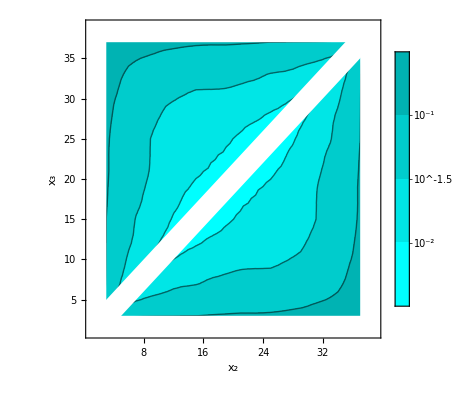

fig-eps-sig-sig-sample-10e4.pdf

```mathematica
L=40;
Table[{i,j,((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528 √(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)measure0[[i,j,1]]},{i,1,39},{j,1,39}]//Flatten[#,1]&;
ListContourPlot[%,Contours->{10^-2,10^-1.5,10^-1(*,10^-0.5,1*)},PlotLegends->BarLegend[Automatic,All,"TickLabels"->(Superscript[10,#]&/@{-2,-1.5,-1})],FrameLabel->{"x_2","x_3"},ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}]];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-sample-10e4.pdf",%]
```

#### sampel size 10^5

```mathematica
measure0(*sample size 10^5*)={{{0.12427789523825082,0.1341545537182509},{0.10904972525600004,0.12650670944874942},{0.10350146697943564,0.11861284416222184},{0.10405880842506238,0.11644113589366538},{0.10154980536824933,0.11537980410595988},{0.09997109641512492,0.11526760894702953},{0.09792643567868702,0.11687445042136523},{0.09634418013862513,0.11711323838761531},{0.09501293039799974,0.11878742249024346},{0.09410898134987505,0.11898266048695708},{0.09327485189324958,0.12069691219297388},{0.09257501318850003,0.12101900855695061},{0.09187180896737453,0.1230620645674856},{0.09126695272512501,0.12357370562784306},{0.0908767064541245,0.12575129602051652},{0.09067404074468752,0.12653659843564496},{0.09049467482087455,0.12918597583870559},{0.0905727076509373,0.13155832375231424},{0.09076867456418727,0.13418006272959793},{0.0909816812446871,0.12815715359745974},{0.09137701879062428,0.12563878282138088},{0.09213043124468746,0.12257331568050756},{0.09306667456418702,0.12140772184440748},{0.09420583265093757,0.11902465067839325},{0.09551079982087447,0.11823518673055987},{0.09685316574468769,0.11594956046757038},{0.09844433145412453,0.11543623980823986},{0.10035545272512482,0.11302413700094721},{0.10280318396737442,0.11213445815709436},{0.10583776318849993,0.1096403722969199},{0.1094654768932494,0.10894999223387809},{0.11381248134987498,0.10629055332852413},{0.11928005539799946,0.10528562516890336},{0.12624743013862494,0.10274572610920096},{0.13586743567868695,0.1025971292810715},{0.15091809641512477,0.10256723706720772},{0.17624668036824973,0.10631733859112202},{0.26552180842506184,0.09550360914693143},{0.3174232169794388,0.07864268124411863},{0.21355447525599727,0.09765259599314832}},{{0.10904972525600004,0.12650670944874942},{0.05354614523825003,0.1449700401825085},{0.04976485025600022,0.13341422165795971},{0.05786421697943748,0.12142200313679412},{0.06065455842506256,0.11630828991314242},{0.061723430368249954,0.11278857106338372},{0.06193647141512496,0.11142257746700328},{0.06180906067868742,0.11069154429121272},{0.06161405513862499,0.11062893584938258},{0.06164880539799993,0.11030338399044158},{0.06171548134987503,0.11056407887154958},{0.061657101893249994,0.11053371285049612},{0.06152201318850001,0.11131936463932092},{0.06137743396737492,0.11170453333349156},{0.061286702725125014,0.11279185360253055},{0.06140458145412497,0.11355278683351716},{0.061535415744687454,0.11525010838230701},{0.06171317482087495,0.11754996480910845},{0.062028957650937556,0.12055665284269794},{0.062385174564187545,0.11620430157604959},{0.06281155624468751,0.11242155945840213},{0.063475893790625,0.10992736994584563},{0.06435643124468747,0.10860850610903287},{0.06545404956418746,0.10706159483832939},{0.06665170765093746,0.10632981569084948},{0.067812674820875,0.10513209321649182},{0.06913879074468747,0.10483497959575476},{0.07068833145412497,0.10394173260769392},{0.07269195272512495,0.10348065255556108},{0.07526318396737502,0.10254475531465447},{0.07832263818849997,0.10251287245582234},{0.08196660189325,0.10203827058113324},{0.08655085634987492,0.10234808042759728},{0.09240343039800006,0.10339749681947585},{0.10047930513862444,0.10585448986705318},{0.11302606067868728,0.10984847526655973},{0.134936721415125,0.11417689020423377},{0.2071599303682494,0.11206607682036883},{0.26552180842506184,0.09550360914693143},{0.2101907169794364,0.08859329733159808}},{{0.10350146697943564,0.11861284416222184},{0.04976485025600022,0.13341422165795971},{0.01062039523825014,0.1435686273275888},{0.014088350256000172,0.12950908199771852},{0.019164966979437537,0.11890600829630057},{0.021807183425062514,0.11372993639334925},{0.02340355536825,0.10892700781056017},{0.02434134641512499,0.10546129511642768},{0.024952685678687466,0.10430539963238197},{0.02549980513862496,0.10266403356326784},{0.026111930397999965,0.1026167499168455},{0.026576731349874955,0.10160188449679906},{0.026826851893249983,0.10211636647069464},{0.027035263188499966,0.10157509420209498},{0.027258183967374956,0.10249154768242053},{0.02743845272512496,0.10249055259550861},{0.02771670645412497,0.10416506223524871},{0.02801554074468745,0.10578073631164803},{0.028262299820874987,0.10943019694882165},{0.02860108265093742,0.10940307391799368},{0.0290114245641874,0.1089786186478939},{0.029517806244687445,0.10415373281845654},{0.030133393790624883,0.10219403687423484},{0.030949056244687426,0.10029528156629221},{0.031810549564187475,0.10015573061941895},{0.03261720765093746,0.09906621249225724},{0.03350754982087494,0.09962754570077824},{0.034501915744687466,0.09920112973031715},{0.03575720645412498,0.10007386053550654},{0.03738820272512499,0.09981912462221482},{0.03936530896737496,0.10120226143449017},{0.04177763818849998,0.10185592192633047},{0.044806351893249954,0.10435173967329457},{0.04879073134987491,0.1077848622623931},{0.05417955539799991,0.11342920672633215},{0.06295230513862513,0.11902293319599089},{0.07810956067868773,0.12231371778747137},{0.134936721415125,0.11417689020423377},{0.17624668036824973,0.10631733859112201},{0.14414643342506214,0.10375669004585626}},{{0.10405880842506238,0.11644113589366538},{0.05786421697943748,0.12142200313679412},{0.014088350256000172,0.12950908199771852},{0.00681339523825015,0.13922207995073468},{0.008128850256000141,0.12764258685452526},{0.011547716979437616,0.11729545607093371},{0.013659308425062605,0.11361921110322849},{0.014931305368250068,0.10857179315208164},{0.015765721415125066,0.10524518460897815},{0.01640706067868756,0.1028043350994807},{0.01708155513862506,0.10184707878944706},{0.017696305398000035,0.10059209194343516},{0.018131106349875043,0.10058461678676883},{0.018404351893250036,0.09992450398552465},{0.018697763188500065,0.10041858251233483},{0.018906933967375056,0.10053727561352162},{0.019145952725125044,0.10180096389466393},{0.019539331454125043,0.10336837022365833},{0.019855540744687546,0.10673916601927341},{0.020156924820875034,0.1077014613781934},{0.020517957650937543,0.1077592604474965},{0.02098904956418751,0.1042771932122236},{0.021602556244687512,0.10143909535047824},{0.022364018790625023,0.0995846674337928},{0.02306255624468751,0.09930811314713343},{0.023745424564187535,0.09861191745024071},{0.024557582650937482,0.09904960283468395},{0.02539392482087502,0.09896399874331405},{0.026407540744687475,0.09996421596997132},{0.027719706454125054,0.10044562247541067},{0.02934420272512497,0.10217092453413913},{0.031410558967375025,0.10438666825283785},{0.03405588818850005,0.10807189060093196},{0.03752960189324993,0.11265813713154206},{0.04221385634987483,0.11848663228380403},{0.04980343039799995,0.12175163544264939},{0.06295230513862511,0.11902293319599089},{0.11302606067868728,0.10984847526655973},{0.15091809641512477,0.1025672370672077},{0.12999618036824984,0.10201061277658384}},{{0.10154980536824933,0.11537980410595988},{0.06065455842506256,0.11630828991314242},{0.019164966979437537,0.11890600829630057},{0.008128850256000141,0.12764258685452526},{0.0037345202382501417,0.13922161835769697},{0.005280850256000125,0.125879319058759},{0.007811216979437608,0.11649277901946013},{0.00942930842506259,0.11200432741408017},{0.010414680368250101,0.10768346475768338},{0.011133471415125065,0.1039229240861705},{0.011853685678687595,0.10257790095606112},{0.012500555138625073,0.10026365997559619},{0.013029305398000094,0.09992741127371482},{0.013377856349875062,0.09856885571616128},{0.013623101893250097,0.0990838048531757},{0.013905638188500083,0.09859540644154001},{0.014204683967375105,0.10000263925218503},{0.014543452725125089,0.10095747985833652},{0.014929956454125079,0.10445171671145448},{0.015313665744687564,0.10526858858862592},{0.01562492482087508,0.10491425333667499},{0.016026707650937548,0.10246059246701651},{0.01660067456418756,0.10070136604658463},{0.017385056244687554,0.09835124473607712},{0.01806976879062505,0.0984118963247154},{0.01863130624468756,0.09763331040498782},{0.019360299564187545,0.09864308246322549},{0.020111582650937532,0.09836896463372555},{0.020982674820875024,0.09995165990350666},{0.02214204074468751,0.10069881721446147},{0.023567831454124975,0.10360810595535762},{0.02541495272512499,0.10679001077797655},{0.027781308967374976,0.11227273966672557},{0.030924138188500015,0.1169327974574162},{0.035222226893249955,0.12109163387791007},{0.042213856349874825,0.11848663228380403},{0.05417955539799992,0.11342920672633215},{0.10047930513862444,0.10585448986705318},{0.13586743567868695,0.1025971292810715},{0.11997547141512498,0.10206998343571323}},{{0.09997109641512492,0.11526760894702953},{0.061723430368249954,0.11278857106338372},{0.021807183425062514,0.11372993639334925},{0.011547716979437616,0.11729545607093371},{0.005280850256000125,0.125879319058759},{0.002926645238250142,0.1374045252744057},{0.003937975256000126,0.12528807792030236},{0.005972216979437617,0.11445027189737579},{0.007197558425062601,0.11070519702546505},{0.007950680368250088,0.10567606018810728},{0.008713471415125079,0.10302764792104674},{0.009482060678687575,0.10089509514611235},{0.01008143013862508,0.09978231103857757},{0.010438805398000075,0.09829432114045222},{0.010645606349875079,0.09811202118121258},{0.010872476893250061,0.09745304927504267},{0.01127238818850009,0.09824469706923503},{0.011680933967375068,0.09924932517621937},{0.011974702725125071,0.10227999443879424},{0.012362206454125073,0.10349838994233412},{0.012731665744687563,0.10252116769081279},{0.013088549820875062,0.10047115801707408},{0.013550207650937543,0.09950013163615005},{0.014250549564187554,0.09765184391252116},{0.014976181244687591,0.09730155713287716},{0.015587518790625041,0.09692523485274977},{0.01625118124468758,0.09781577036467866},{0.01692704956418754,0.09825000505877443},{0.017757707650937576,0.09992191907405612},{0.018816549820875054,0.10210048271117357},{0.02017629074468754,0.10585677986120447},{0.02189895645412504,0.1103062324295283},{0.02405595272512503,0.11563585285098686},{0.026922308967374988,0.11808758539708933},{0.030924138188500015,0.1169327974574162},{0.03752960189324992,0.11265813713154205},{0.04879073134987491,0.1077848622623931},{0.09240343039800006,0.10339749681947585},{0.12624743013862494,0.10274572610920098},{0.11396206067868747,0.10240472945051622}},{{0.09792643567868702,0.11687445042136523},{0.06193647141512496,0.11142257746700328},{0.02340355536825,0.10892700781056017},{0.013659308425062605,0.11361921110322849},{0.007811216979437608,0.11649277901946013},{0.003937975256000126,0.12528807792030236},{0.0022252702382501467,0.13804840252764225},{0.003209350256000122,0.12456869529650973},{0.0047374669794376005,0.11473802004564944},{0.00567480842506259,0.10965040911272741},{0.006451805368250084,0.1052777864875428},{0.007218971415125078,0.10205550266875321},{0.007916560678687583,0.10129065035826315},{0.008391930138625077,0.09947557617379515},{0.008609805398000075,0.09956454679051872},{0.008813731349875065,0.09816465099240108},{0.009185726893250073,0.09865438665709231},{0.009671638188500083,0.09900597561101973},{0.010001308967375085,0.1021345614925641},{0.010289327725125077,0.10305666648053917},{0.010645956454125092,0.1022659253264695},{0.011018165744687575,0.09973186904444005},{0.011453174820875081,0.09999186482564366},{0.01203070765093756,0.09835430679295148},{0.012690674564187581,0.09820967684680075},{0.013356431244687588,0.09751729709223536},{0.014049518790625094,0.09889378716561227},{0.014706556244687585,0.09946121934770966},{0.015537549564187588,0.10214198349155258},{0.0165462076509376,0.10513534771260062},{0.01779592482087508,0.11042965445520944},{0.019486040744687547,0.11478702488445001},{0.021461081454125015,0.11870275170465173},{0.02405595272512503,0.11563585285098686},{0.027781308967374976,0.1122727396667256},{0.03405588818850004,0.10807189060093196},{0.044806351893249954,0.10435173967329457},{0.08655085634987494,0.10234808042759728},{0.11928005539799948,0.10528562516890339},{0.10916043013862507,0.10493745335664086}},{{0.09634418013862513,0.11711323838761531},{0.06180906067868742,0.11069154429121272},{0.02434134641512499,0.10546129511642768},{0.014931305368250068,0.10857179315208164},{0.00942930842506259,0.11200432741408017},{0.005972216979437617,0.11445027189737579},{0.003209350256000122,0.12456869529650973},{0.0019063952382501425,0.13672338539365508},{0.00257885025600012,0.12436090377382607},{0.0037984669794376,0.11313961963723407},{0.0046859334250625795,0.10918097378290083},{0.0054394303682500835,0.10399720132302975},{0.006097721415125079,0.10138748987129177},{0.006660435678687583,0.09955174155645073},{0.00701230513862508,0.09938835383278743},{0.007296680398000074,0.09876657578691987},{0.007625981349875064,0.09888654676443674},{0.008032726893250073,0.09915521915778791},{0.008489763188500055,0.10154878756165976},{0.008857808967375064,0.10251572138059163},{0.009114702725125072,0.10130553552687269},{0.009424206454125067,0.09885751453065575},{0.00984604074468756,0.09896817985295887},{0.010370049820875063,0.09882280286419094},{0.010920957650937566,0.09851818492336144},{0.011528049564187558,0.09804220832022333},{0.01227380624468757,0.09943229261761147},{0.013008893790625073,0.10141037407248746},{0.013833806244687594,0.10493216354843109},{0.014855924564187564,0.10905871184853548},{0.016050082650937596,0.11417225354149645},{0.017612674820875092,0.1161542675472732},{0.019486040744687547,0.11478702488445001},{0.021898956454125037,0.1103062324295283},{0.025414952725124985,0.10679001077797652},{0.031410558967375025,0.10438666825283785},{0.04177763818849998,0.1018559219263305},{0.08196660189325003,0.10203827058113324},{0.11381248134987501,0.1062905533285241},{0.10556480539800016,0.10558350312980916}},{{0.09501293039799974,0.11878742249024346},{0.06161405513862499,0.11062893584938258},{0.024952685678687466,0.10430539963238197},{0.015765721415125066,0.10524518460897815},{0.010414680368250101,0.10768346475768338},{0.007197558425062601,0.11070519702546505},{0.0047374669794376005,0.11473802004564944},{0.00257885025600012,0.12436090377382607},{0.0014891452382501437,0.13764153541303142},{0.002074225256000119,0.12410362801489334},{0.0031532169794375982,0.11415386656765758},{0.0040234334250625866,0.10896259361603734},{0.004663430368250079,0.10443027820489065},{0.005188971415125077,0.10100156020292513},{0.005640685678687578,0.1003390957156906},{0.005992555138625075,0.09928407661467177},{0.006352930398000067,0.10029173898369276},{0.006692356349875078,0.1005268785788241},{0.007105601893250066,0.10322840521958684},{0.007578013188500068,0.10364029956603449},{0.00786268396737507,0.10238468236564374},{0.008095827725125062,0.09950684629057319},{0.008442331454125073,0.0996366249902905},{0.008944040744687572,0.09989379189221946},{0.009452299820875074,0.10082763837290833},{0.009981832650937572,0.10022108407912432},{0.010674424564187596,0.10233760548813077},{0.011457806244687594,0.10500612103259371},{0.012351893790625082,0.1099536185367309},{0.01341880624468758,0.1139831384437541},{0.014636924564187598,0.11758558135131332},{0.016050082650937596,0.11417225354149645},{0.01779592482087508,0.11042965445520944},{0.020176290744687537,0.10585677986120447},{0.02356783145412498,0.10360810595535762},{0.029344202725124974,0.1021709245341391},{0.039365308967374966,0.10120226143449017},{0.07832263818849997,0.10251287245582234},{0.10946547689324944,0.10894999223387809},{0.10264060634987517,0.10813571438527098}},{{0.09410898134987505,0.11898266048695708},{0.06164880539799993,0.11030338399044158},{0.02549980513862496,0.10266403356326784},{0.01640706067868756,0.1028043350994807},{0.011133471415125065,0.1039229240861705},{0.007950680368250088,0.10567606018810728},{0.00567480842506259,0.10965040911272741},{0.0037984669794376,0.11313961963723407},{0.002074225256000119,0.12410362801489334},{0.0012638952382501417,0.13653102629725447},{0.001756600256000121,0.12402752308026391},{0.002785716979437601,0.11273340286444405},{0.003569433425062587,0.10874831658329709},{0.004109555368250082,0.10357897173209377},{0.00456359641512508,0.10101867364309085},{0.004925560678687581,0.09921141782097961},{0.005297430138625067,0.09934648443662908},{0.005668055398000074,0.10004652264051725},{0.006024731349875069,0.1028807439079494},{0.0064387268932500664,0.10434429912325652},{0.006777263188500067,0.10302120544994962},{0.007076183967375071,0.10033235600013081},{0.007375952725125071,0.0998805487543926},{0.007783831454125071,0.10044539869053752},{0.008304665744687566,0.10211998552208505},{0.00880892482087507,0.10305074517536301},{0.00941045765093757,0.10569785288093123},{0.010173674564187569,0.10937388954678606},{0.011092556244687576,0.1140138489917161},{0.012186268790625097,0.11563874112844938},{0.01341880624468758,0.1139831384437541},{0.014855924564187563,0.10905871184853548},{0.016546207650937603,0.10513534771260062},{0.018816549820875047,0.10210048271117357},{0.02214204074468751,0.10069881721446147},{0.027719706454125054,0.10044562247541067},{0.03738820272512499,0.09981912462221482},{0.07526318396737501,0.10254475531465447},{0.10583776318849993,0.1096403722969199},{0.10031622689324998,0.10870066347189743}},{{0.09327485189324958,0.12069691219297388},{0.06171548134987503,0.11056407887154958},{0.026111930397999965,0.1026167499168455},{0.01708155513862506,0.10184707878944706},{0.011853685678687595,0.10257790095606112},{0.008713471415125079,0.10302764792104674},{0.006451805368250084,0.1052777864875428},{0.0046859334250625795,0.10918097378290083},{0.0031532169794375982,0.11415386656765758},{0.001756600256000121,0.12402752308026391},{0.001086520238250143,0.13738288576413774},{0.001595725256000122,0.12385114024969715},{0.0024992169794375955,0.1139557799640573},{0.003152558425062589,0.10882028831884305},{0.0036301803682500873,0.10444071668418725},{0.003991596415125078,0.10110909614959519},{0.004362685678687576,0.1005545789739791},{0.004795680138625073,0.10024397708147739},{0.005200180398000077,0.10307290196931794},{0.005589981349875065,0.1045835207634518},{0.005874851893250069,0.10447135472071581},{0.006230513188500072,0.1021461862766052},{0.006594558967375058,0.10243364098321006},{0.006978077725125065,0.10273419062172455},{0.007473831454125069,0.10569210511135536},{0.00796079074468758,0.10774631368663495},{0.008458174820875072,0.11139176846294192},{0.00912083265093757,0.11466163461590997},{0.010014674564187576,0.11786053580213798},{0.011092556244687576,0.11401384899171611},{0.012351893790625082,0.1099536185367309},{0.013833806244687594,0.10493216354843109},{0.015537549564187587,0.10214198349155258},{0.017757707650937572,0.09992191907405612},{0.020982674820875024,0.09995165990350666},{0.026407540744687485,0.09996421596997132},{0.03575720645412498,0.10007386053550654},{0.07269195272512494,0.10348065255556108},{0.10280318396737442,0.11213445815709436},{0.09832051318849995,0.11101772573938673}},{{0.09257501318850003,0.12101900855695061},{0.061657101893249994,0.11053371285049612},{0.026576731349874955,0.10160188449679906},{0.017696305398000035,0.10059209194343516},{0.012500555138625073,0.10026365997559619},{0.009482060678687575,0.10089509514611235},{0.007218971415125078,0.10205550266875321},{0.0054394303682500835,0.10399720132302975},{0.0040234334250625866,0.10896259361603734},{0.002785716979437601,0.11273340286444405},{0.001595725256000122,0.12385114024969715},{0.0009706452382501422,0.1364106308139189},{0.0013894752560001191,0.12399299067497843},{0.002264716979437602,0.11277850387473133},{0.002875433425062589,0.10882299383868056},{0.003196555368250087,0.10377986834236547},{0.0035274714151250783,0.10149328971515124},{0.003952935678687576,0.10073749375815932},{0.0044221801386250675,0.10274343886475554},{0.004894305398000068,0.10417937679760413},{0.005183356349875057,0.10374263666552394},{0.005497226893250075,0.10234008884523413},{0.005933888188500066,0.10327275779815313},{0.0063591839673750655,0.10548707958468989},{0.006824952725125074,0.10972378405232186},{0.00730183145412508,0.11385977791708209},{0.007796165744687574,0.11701243404024561},{0.00834717482087508,0.11690999830094977},{0.00912083265093757,0.11466163461590997},{0.010173674564187567,0.10937388954678606},{0.011457806244687594,0.10500612103259374},{0.013008893790625073,0.10141037407248746},{0.014706556244687582,0.09946121934770966},{0.01692704956418754,0.09825000505877443},{0.020111582650937525,0.09836896463372553},{0.02539392482087502,0.09896399874331405},{0.034501915744687466,0.09920112973031715},{0.07068833145412497,0.10394173260769392},{0.10035545272512482,0.11302413700094725},{0.09666043396737485,0.11170527906315497}},{{0.09187180896737453,0.1230620645674856},{0.06152201318850001,0.11131936463932092},{0.026826851893249983,0.10211636647069464},{0.018131106349875043,0.10058461678676883},{0.013029305398000094,0.09992741127371482},{0.01008143013862508,0.09978231103857757},{0.007916560678687583,0.10129065035826315},{0.006097721415125079,0.10138748987129177},{0.004663430368250079,0.10443027820489065},{0.003569433425062587,0.10874831658329709},{0.0024992169794375955,0.1139557799640573},{0.0013894752560001191,0.12399299067497843},{0.0008733952382501456,0.13745386772967225},{0.0013564752560001213,0.12387285640432778},{0.0021404669794376015,0.11395890088486942},{0.0025475584250625877,0.10895912966575715},{0.002806430368250087,0.10500915022120443},{0.003160721415125081,0.10286926345294177},{0.0036348106786875736,0.10451078389746327},{0.004180055138625065,0.10543843213389234},{0.004573180398000071,0.10511956610094482},{0.004880856349875064,0.10351373955303872},{0.005289101893250068,0.10522648730854958},{0.0057941381885000705,0.10839017083036331},{0.0062703089673750625,0.11441116327281282},{0.006710952725125076,0.11983858008260759},{0.007239831454125085,0.12294844954821782},{0.007796165744687574,0.11701243404024557},{0.008458174820875072,0.11139176846294192},{0.00941045765093757,0.10569785288093123},{0.010674424564187593,0.10233760548813077},{0.01227380624468757,0.09943229261761147},{0.014049518790625094,0.09889378716561227},{0.016251181244687576,0.09781577036467867},{0.019360299564187545,0.09864308246322549},{0.02455758265093749,0.09904960283468393},{0.03350754982087495,0.09962754570077824},{0.06913879074468747,0.10483497959575476},{0.09844433145412453,0.11543623980823989},{0.09527907772512517,0.1141316966949753}},{{0.09126695272512501,0.12357370562784306},{0.06137743396737492,0.11170453333349156},{0.027035263188499966,0.10157509420209498},{0.018404351893250036,0.09992450398552465},{0.013377856349875062,0.09856885571616128},{0.010438805398000075,0.09829432114045222},{0.008391930138625077,0.09947557617379515},{0.006660435678687583,0.09955174155645073},{0.005188971415125077,0.10100156020292513},{0.004109555368250082,0.10357897173209377},{0.003152558425062589,0.10882028831884305},{0.002264716979437602,0.11277850387473133},{0.0013564752560001213,0.12387285640432778},{0.0008388952382501424,0.13636133121003968},{0.0012074752560001206,0.1238092098976763},{0.0017457169794375957,0.11282923391747628},{0.002100308425062589,0.10940946037012336},{0.0024508053682500822,0.1055537937040102},{0.0028860964151250766,0.10561669530805504},{0.0034276856786875746,0.10660824844261824},{0.003888680138625067,0.10605172335206185},{0.00429580539800007,0.10550042851171441},{0.0046959813498750665,0.10775845489804892},{0.005259351893250077,0.11152925748012316},{0.005822013188500068,0.11691069121924065},{0.006230058967375067,0.12018069009691343},{0.0067109527251250755,0.11983858008260759},{0.007301831454125081,0.11385977791708209},{0.00796079074468758,0.10774631368663495},{0.008808924820875069,0.10305074517536301},{0.009981832650937572,0.10022108407912433},{0.011528049564187555,0.09804220832022334},{0.01335643124468759,0.09751729709223536},{0.015587518790625041,0.09692523485274977},{0.01863130624468755,0.09763331040498782},{0.023745424564187535,0.0986119174502407},{0.03261720765093746,0.09906621249225724},{0.06781267482087498,0.10513209321649182},{0.09685316574468769,0.11594956046757038},{0.09419420645412495,0.11469454053073566}},{{0.0908767064541245,0.12575129602051652},{0.061286702725125014,0.11279185360253055},{0.027258183967374956,0.10249154768242053},{0.018697763188500065,0.10041858251233483},{0.013623101893250097,0.0990838048531757},{0.010645606349875079,0.09811202118121258},{0.008609805398000075,0.09956454679051872},{0.00701230513862508,0.09938835383278743},{0.005640685678687578,0.1003390957156906},{0.00456359641512508,0.10101867364309085},{0.0036301803682500873,0.10444071668418725},{0.002875433425062589,0.10882299383868056},{0.0021404669794376015,0.11395890088486942},{0.0012074752560001206,0.1238092098976763},{0.0006877702382501449,0.13724259682805925},{0.0008701002560001197,0.1239071557028435},{0.0012872169794375932,0.11453481617911554},{0.0017233084250625858,0.11069228362095686},{0.00223993036825008,0.1091503289582023},{0.0027772214151250783,0.10934050734870568},{0.003167435678687574,0.10932059672324093},{0.0036358051386250713,0.10927179481689692},{0.004159805398000066,0.1127347337646663},{0.004675106349875071,0.11630383532945512},{0.005285976893250077,0.11974923619804187},{0.005822013188500067,0.11691069121924065},{0.0062703089673750625,0.11441116327281282},{0.006824952725125074,0.10972378405232186},{0.007473831454125069,0.10569210511135539},{0.008304665744687566,0.10211998552208505},{0.009452299820875074,0.10082763837290833},{0.010920957650937566,0.09851818492336145},{0.012690674564187581,0.09820967684680075},{0.014976181244687591,0.09730155713287716},{0.01806976879062505,0.0984118963247154},{0.02306255624468751,0.09930811314713343},{0.03181054956418747,0.10015573061941893},{0.06665170765093746,0.10632981569084948},{0.09551079982087449,0.11823518673055983},{0.0933520407446877,0.11698077156458782}},{{0.09067404074468752,0.12653659843564496},{0.06140458145412497,0.11355278683351716},{0.02743845272512496,0.10249055259550861},{0.018906933967375056,0.10053727561352162},{0.013905638188500083,0.09859540644154001},{0.010872476893250061,0.09745304927504267},{0.008813731349875065,0.09816465099240108},{0.007296680398000074,0.09876657578691987},{0.005992555138625075,0.09928407661467177},{0.004925560678687581,0.09921141782097961},{0.003991596415125078,0.10110909614959519},{0.003196555368250087,0.10377986834236547},{0.0025475584250625877,0.10895912966575715},{0.0017457169794375957,0.11282923391747628},{0.0008701002560001197,0.1239071557028435},{0.0004410202382501422,0.1364574013336137},{0.000562225256000117,0.12424430478489026},{0.0009647169794375981,0.11453194793126877},{0.0015305584250625878,0.11377039137503857},{0.0021383053682500815,0.11360360140997246},{0.0025420964151250764,0.11340663006480431},{0.0029464356786875747,0.11401410180775987},{0.003487180138625073,0.1170080163997812},{0.004075930398000063,0.11814013700536426},{0.004675106349875071,0.11630383532945512},{0.005259351893250077,0.1115292574801231},{0.00579413818850007,0.10839017083036331},{0.0063591839673750655,0.10548707958468989},{0.006978077725125065,0.10273419062172455},{0.007783831454125071,0.1004453986905375},{0.008944040744687572,0.09989379189221946},{0.010370049820875063,0.09882280286419093},{0.01203070765093756,0.09835430679295148},{0.014250549564187552,0.09765184391252116},{0.01738505624468755,0.09835124473607712},{0.022364018790625023,0.0995846674337928},{0.030949056244687426,0.10029528156629221},{0.06545404956418746,0.10706159483832942},{0.09420583265093757,0.11902465067839325},{0.09256179982087498,0.11787589375539946}},{{0.09049467482087455,0.12918597583870559},{0.061535415744687454,0.11525010838230701},{0.02771670645412497,0.10416506223524871},{0.019145952725125044,0.10180096389466393},{0.014204683967375105,0.10000263925218503},{0.01127238818850009,0.09824469706923503},{0.009185726893250073,0.09865438665709231},{0.007625981349875064,0.09888654676443674},{0.006352930398000067,0.10029173898369276},{0.005297430138625067,0.09934648443662908},{0.004362685678687576,0.1005545789739791},{0.0035274714151250783,0.10149328971515124},{0.002806430368250087,0.10500915022120443},{0.002100308425062589,0.10940946037012336},{0.0012872169794375932,0.11453481617911554},{0.000562225256000117,0.12424430478489026},{0.00028189523825014265,0.13756309468675232},{0.00045285025600011984,0.12505307000554197},{0.0009112169794375953,0.11904879157619602},{0.0015341834250625858,0.12070768129274197},{0.0020526803682500796,0.12052610525819991},{0.0024655964151250797,0.12025075088142141},{0.002880310678687568,0.12146116749326293},{0.0034871801386250722,0.1170080163997812},{0.004159805398000067,0.1127347337646663},{0.0046959813498750665,0.10775845489804894},{0.005289101893250066,0.10522648730854958},{0.005933888188500066,0.10327275779815313},{0.006594558967375058,0.10243364098321008},{0.007375952725125071,0.0998805487543926},{0.008442331454125073,0.0996366249902905},{0.009846040744687562,0.09896817985295887},{0.011453174820875083,0.09999186482564365},{0.013550207650937543,0.09950013163615007},{0.01660067456418756,0.10070136604658463},{0.021602556244687512,0.10143909535047826},{0.030133393790624883,0.10219403687423484},{0.06435643124468747,0.10860850610903287},{0.09306667456418702,0.12140772184440748},{0.09190883265093758,0.12051537020849089}},{{0.0905727076509373,0.13155832375231424},{0.06171317482087495,0.11754996480910845},{0.02801554074468745,0.10578073631164803},{0.019539331454125043,0.10336837022365833},{0.014543452725125089,0.10095747985833652},{0.011680933967375068,0.09924932517621937},{0.009671638188500083,0.09900597561101973},{0.008032726893250073,0.09915521915778791},{0.006692356349875078,0.1005268785788241},{0.005668055398000074,0.10004652264051725},{0.004795680138625073,0.10024397708147739},{0.003952935678687576,0.10073749375815932},{0.003160721415125081,0.10286926345294177},{0.0024508053682500822,0.1055537937040102},{0.0017233084250625858,0.11069228362095686},{0.0009647169794375981,0.11453194793126877},{0.00045285025600011984,0.12505307000554197},{0.0002668952382501438,0.13746193170591145},{0.00044160025600012035,0.1278473474879132},{0.0009407169794375977,0.1267838415591415},{0.001463683425062585,0.1294265602286575},{0.0020081803682500733,0.12535656205741227},{0.0024655964151250797,0.12025075088142141},{0.0029464356786875747,0.11401410180775987},{0.0036358051386250713,0.10927179481689693},{0.00429580539800007,0.10550042851171441},{0.004880856349875063,0.10351373955303872},{0.005497226893250071,0.10234008884523413},{0.00623051318850007,0.10214618627660521},{0.0070761839673750705,0.10033235600013081},{0.008095827725125066,0.09950684629057319},{0.009424206454125067,0.09885751453065575},{0.011018165744687575,0.09973186904444005},{0.013088549820875064,0.10047115801707408},{0.016026707650937548,0.10246059246701651},{0.020989049564187512,0.10427719321222363},{0.029517806244687445,0.10415373281845654},{0.063475893790625,0.10992736994584563},{0.09213043124468746,0.12257331568050754},{0.09152342456418741,0.12251864096690973}},{{0.09076867456418727,0.13418006272959793},{0.062028957650937556,0.12055665284269794},{0.028262299820874987,0.10943019694882165},{0.019855540744687546,0.10673916601927341},{0.014929956454125079,0.10445171671145448},{0.011974702725125071,0.10227999443879424},{0.010001308967375085,0.1021345614925641},{0.008489763188500055,0.10154878756165976},{0.007105601893250066,0.10322840521958684},{0.006024731349875069,0.1028807439079494},{0.005200180398000077,0.10307290196931794},{0.0044221801386250675,0.10274343886475554},{0.0036348106786875736,0.10451078389746327},{0.0028860964151250766,0.10561669530805504},{0.00223993036825008,0.1091503289582023},{0.0015305584250625878,0.11377039137503857},{0.0009112169794375953,0.11904879157619602},{0.00044160025600012035,0.1278473474879132},{0.00018764523825014185,0.14080241921332062},{0.00039047525600011617,0.13448042568457427},{0.0008259669794375913,0.13601286075289296},{0.0014636834250625842,0.1294265602286575},{0.002052680368250079,0.12052610525819993},{0.0025420964151250764,0.11340663006480431},{0.003167435678687574,0.10932059672324096},{0.0038886801386250665,0.10605172335206185},{0.00457318039800007,0.10511956610094482},{0.005183356349875056,0.10374263666552398},{0.005874851893250068,0.10447135472071581},{0.006777263188500067,0.10302120544994964},{0.00786268396737507,0.10238468236564374},{0.009114702725125072,0.10130553552687269},{0.010645956454125092,0.10226592532646951},{0.012731665744687563,0.10252116769081279},{0.01562492482087508,0.10491425333667499},{0.020517957650937543,0.1077592604474965},{0.0290114245641874,0.1089786186478939},{0.06281155624468751,0.11242155945840213},{0.09137701879062429,0.12563878282138088},{0.09118218124468716,0.12557993283317187}},{{0.0909816812446871,0.12815715359745974},{0.062385174564187545,0.11620430157604959},{0.02860108265093742,0.10940307391799368},{0.020156924820875034,0.1077014613781934},{0.015313665744687564,0.10526858858862592},{0.012362206454125073,0.10349838994233412},{0.010289327725125077,0.10305666648053917},{0.008857808967375064,0.10251572138059163},{0.007578013188500068,0.10364029956603449},{0.0064387268932500664,0.10434429912325652},{0.005589981349875065,0.1045835207634518},{0.004894305398000068,0.10417937679760413},{0.004180055138625065,0.10543843213389234},{0.0034276856786875746,0.10660824844261824},{0.0027772214151250783,0.10934050734870568},{0.0021383053682500815,0.11360360140997246},{0.0015341834250625858,0.12070768129274197},{0.0009407169794375977,0.1267838415591415},{0.00039047525600011617,0.13448042568457427},{0.00021814523825014487,0.14288545435056205},{0.00039047525600011595,0.13448042568457427},{0.0009407169794375968,0.1267838415591415},{0.0015341834250625851,0.12070768129274197},{0.0021383053682500802,0.11360360140997249},{0.0027772214151250783,0.10934050734870568},{0.0034276856786875746,0.10660824844261824},{0.004180055138625066,0.10543843213389234},{0.004894305398000068,0.10417937679760413},{0.005589981349875063,0.10458352076345183},{0.006438726893250065,0.10434429912325652},{0.007578013188500068,0.10364029956603446},{0.008857808967375062,0.10251572138059166},{0.010289327725125077,0.10305666648053916},{0.012362206454125071,0.10349838994233412},{0.015313665744687564,0.10526858858862591},{0.020156924820875034,0.10770146137819343},{0.028601082650937425,0.10940307391799366},{0.06238517456418755,0.11620430157604959},{0.09098168124468711,0.12815715359745974},{0.09104951879062478,0.1273339049526069}},{{0.09137701879062428,0.12563878282138088},{0.06281155624468751,0.11242155945840213},{0.0290114245641874,0.1089786186478939},{0.020517957650937543,0.1077592604474965},{0.01562492482087508,0.10491425333667499},{0.012731665744687563,0.10252116769081279},{0.010645956454125092,0.1022659253264695},{0.009114702725125072,0.10130553552687269},{0.00786268396737507,0.10238468236564374},{0.006777263188500067,0.10302120544994962},{0.005874851893250069,0.10447135472071581},{0.005183356349875057,0.10374263666552394},{0.004573180398000071,0.10511956610094482},{0.003888680138625067,0.10605172335206185},{0.003167435678687574,0.10932059672324093},{0.0025420964151250764,0.11340663006480431},{0.0020526803682500796,0.12052610525819991},{0.001463683425062585,0.1294265602286575},{0.0008259669794375913,0.13601286075289296},{0.00039047525600011595,0.13448042568457427},{0.00018764523825014187,0.14080241921332062},{0.0004416002560001185,0.1278473474879132},{0.0009112169794375938,0.11904879157619602},{0.001530558425062586,0.11377039137503857},{0.00223993036825008,0.1091503289582023},{0.002886096415125076,0.10561669530805506},{0.003634810678687574,0.10451078389746327},{0.0044221801386250675,0.10274343886475554},{0.005200180398000079,0.10307290196931794},{0.006024731349875072,0.1028807439079494},{0.007105601893250066,0.10322840521958684},{0.008489763188500058,0.10154878756165976},{0.010001308967375083,0.10213456149256411},{0.011974702725125071,0.10227999443879424},{0.014929956454125077,0.10445171671145448},{0.019855540744687542,0.10673916601927343},{0.028262299820874987,0.10943019694882165},{0.06202895765093757,0.12055665284269798},{0.09076867456418727,0.13418006272959795},{0.09118218124468716,0.12557993283317187}},{{0.09213043124468746,0.12257331568050756},{0.063475893790625,0.10992736994584563},{0.029517806244687445,0.10415373281845654},{0.02098904956418751,0.1042771932122236},{0.016026707650937548,0.10246059246701651},{0.013088549820875062,0.10047115801707408},{0.011018165744687575,0.09973186904444005},{0.009424206454125067,0.09885751453065575},{0.008095827725125062,0.09950684629057319},{0.007076183967375071,0.10033235600013081},{0.006230513188500072,0.1021461862766052},{0.005497226893250075,0.10234008884523413},{0.004880856349875064,0.10351373955303872},{0.00429580539800007,0.10550042851171441},{0.0036358051386250713,0.10927179481689692},{0.0029464356786875747,0.11401410180775987},{0.0024655964151250797,0.12025075088142141},{0.0020081803682500733,0.12535656205741227},{0.0014636834250625842,0.1294265602286575},{0.0009407169794375968,0.1267838415591415},{0.0004416002560001185,0.1278473474879132},{0.0002668952382501431,0.13746193170591145},{0.0004528502560001189,0.12505307000554197},{0.0009647169794375972,0.11453194793126877},{0.0017233084250625858,0.11069228362095686},{0.0024508053682500814,0.1055537937040102},{0.0031607214151250806,0.10286926345294177},{0.003952935678687574,0.10073749375815932},{0.0047956801386250724,0.10024397708147739},{0.005668055398000074,0.10004652264051725},{0.006692356349875076,0.10052687857882411},{0.008032726893250073,0.09915521915778791},{0.009671638188500083,0.09900597561101973},{0.011680933967375068,0.09924932517621936},{0.014543452725125087,0.10095747985833652},{0.019539331454125043,0.10336837022365833},{0.028015540744687456,0.10578073631164803},{0.06171317482087495,0.11754996480910843},{0.0905727076509373,0.13155832375231424},{0.09152342456418741,0.12251864096690976}},{{0.09306667456418702,0.12140772184440748},{0.06435643124468747,0.10860850610903287},{0.030133393790624883,0.10219403687423484},{0.021602556244687512,0.10143909535047824},{0.01660067456418756,0.10070136604658463},{0.013550207650937543,0.09950013163615005},{0.011453174820875081,0.09999186482564366},{0.00984604074468756,0.09896817985295887},{0.008442331454125073,0.0996366249902905},{0.007375952725125071,0.0998805487543926},{0.006594558967375058,0.10243364098321006},{0.005933888188500066,0.10327275779815313},{0.005289101893250068,0.10522648730854958},{0.0046959813498750665,0.10775845489804892},{0.004159805398000066,0.1127347337646663},{0.003487180138625073,0.1170080163997812},{0.002880310678687568,0.12146116749326293},{0.0024655964151250797,0.12025075088142141},{0.002052680368250079,0.12052610525819993},{0.0015341834250625851,0.12070768129274197},{0.0009112169794375938,0.11904879157619602},{0.0004528502560001189,0.12505307000554197},{0.0002818952382501429,0.1375630946867523},{0.0005622252560001164,0.12424430478489026},{0.0012872169794375923,0.11453481617911554},{0.002100308425062588,0.10940946037012339},{0.002806430368250087,0.10500915022120443},{0.0035274714151250783,0.10149328971515124},{0.004362685678687576,0.1005545789739791},{0.005297430138625067,0.09934648443662908},{0.006352930398000067,0.10029173898369276},{0.007625981349875067,0.09888654676443674},{0.009185726893250073,0.0986543866570923},{0.01127238818850009,0.09824469706923503},{0.014204683967375105,0.10000263925218503},{0.019145952725125044,0.10180096389466393},{0.02771670645412497,0.10416506223524871},{0.06153541574468745,0.11525010838230701},{0.09049467482087457,0.12918597583870559},{0.09190883265093758,0.12051537020849089}},{{0.09420583265093757,0.11902465067839325},{0.06545404956418746,0.10706159483832939},{0.030949056244687426,0.10029528156629221},{0.022364018790625023,0.0995846674337928},{0.017385056244687554,0.09835124473607712},{0.014250549564187554,0.09765184391252116},{0.01203070765093756,0.09835430679295148},{0.010370049820875063,0.09882280286419094},{0.008944040744687572,0.09989379189221946},{0.007783831454125071,0.10044539869053752},{0.006978077725125065,0.10273419062172455},{0.0063591839673750655,0.10548707958468989},{0.0057941381885000705,0.10839017083036331},{0.005259351893250077,0.11152925748012316},{0.004675106349875071,0.11630383532945512},{0.004075930398000063,0.11814013700536426},{0.0034871801386250722,0.1170080163997812},{0.0029464356786875747,0.11401410180775987},{0.0025420964151250764,0.11340663006480431},{0.0021383053682500802,0.11360360140997249},{0.001530558425062586,0.11377039137503857},{0.0009647169794375972,0.11453194793126877},{0.0005622252560001164,0.12424430478489026},{0.0004410202382501419,0.1364574013336137},{0.0008701002560001179,0.1239071557028435},{0.0017457169794375936,0.11282923391747628},{0.002547558425062587,0.10895912966575717},{0.003196555368250087,0.10377986834236547},{0.003991596415125078,0.10110909614959519},{0.004925560678687583,0.09921141782097959},{0.005992555138625077,0.09928407661467177},{0.007296680398000074,0.09876657578691987},{0.008813731349875065,0.09816465099240108},{0.010872476893250061,0.09745304927504267},{0.013905638188500083,0.09859540644154001},{0.018906933967375056,0.10053727561352165},{0.027438452725124962,0.10249055259550861},{0.06140458145412497,0.11355278683351713},{0.0906740407446875,0.12653659843564496},{0.09256179982087497,0.11787589375539946}},{{0.09551079982087447,0.11823518673055987},{0.06665170765093746,0.10632981569084948},{0.031810549564187475,0.10015573061941895},{0.02306255624468751,0.09930811314713343},{0.01806976879062505,0.0984118963247154},{0.014976181244687591,0.09730155713287716},{0.012690674564187581,0.09820967684680075},{0.010920957650937566,0.09851818492336144},{0.009452299820875074,0.10082763837290833},{0.008304665744687566,0.10211998552208505},{0.007473831454125069,0.10569210511135536},{0.006824952725125074,0.10972378405232186},{0.0062703089673750625,0.11441116327281282},{0.005822013188500068,0.11691069121924065},{0.005285976893250077,0.11974923619804187},{0.004675106349875071,0.11630383532945512},{0.004159805398000067,0.1127347337646663},{0.0036358051386250713,0.10927179481689693},{0.003167435678687574,0.10932059672324096},{0.0027772214151250783,0.10934050734870568},{0.00223993036825008,0.1091503289582023},{0.0017233084250625858,0.11069228362095686},{0.0012872169794375923,0.11453481617911554},{0.0008701002560001179,0.1239071557028435},{0.0006877702382501446,0.13724259682805925},{0.00120747525600012,0.1238092098976763},{0.0021404669794376,0.11395890088486942},{0.002875433425062589,0.10882299383868056},{0.003630180368250088,0.10444071668418725},{0.0045635964151250815,0.10101867364309085},{0.005640685678687579,0.10033909571569058},{0.007012305138625081,0.09938835383278743},{0.008609805398000077,0.09956454679051871},{0.010645606349875079,0.09811202118121258},{0.013623101893250096,0.0990838048531757},{0.018697763188500062,0.10041858251233482},{0.027258183967374963,0.10249154768242053},{0.06128670272512501,0.11279185360253056},{0.09087670645412452,0.12575129602051652},{0.0933520407446877,0.11698077156458782}},{{0.09685316574468769,0.11594956046757038},{0.067812674820875,0.10513209321649182},{0.03261720765093746,0.09906621249225724},{0.023745424564187535,0.09861191745024071},{0.01863130624468756,0.09763331040498782},{0.015587518790625041,0.09692523485274977},{0.013356431244687588,0.09751729709223536},{0.011528049564187558,0.09804220832022333},{0.009981832650937572,0.10022108407912432},{0.00880892482087507,0.10305074517536301},{0.00796079074468758,0.10774631368663495},{0.00730183145412508,0.11385977791708209},{0.006710952725125076,0.11983858008260759},{0.006230058967375067,0.12018069009691343},{0.005822013188500067,0.11691069121924065},{0.005259351893250077,0.1115292574801231},{0.0046959813498750665,0.10775845489804894},{0.00429580539800007,0.10550042851171441},{0.0038886801386250665,0.10605172335206185},{0.0034276856786875746,0.10660824844261824},{0.002886096415125076,0.10561669530805506},{0.0024508053682500814,0.1055537937040102},{0.002100308425062588,0.10940946037012339},{0.0017457169794375936,0.11282923391747628},{0.00120747525600012,0.1238092098976763},{0.0008388952382501423,0.13636133121003968},{0.0013564752560001187,0.1238728564043278},{0.0022647169794376004,0.11277850387473133},{0.0031525584250625895,0.10882028831884304},{0.004109555368250084,0.10357897173209377},{0.005188971415125079,0.10100156020292513},{0.006660435678687584,0.09955174155645073},{0.008391930138625077,0.09947557617379514},{0.010438805398000075,0.09829432114045222},{0.013377856349875065,0.09856885571616127},{0.018404351893250043,0.09992450398552465},{0.027035263188499976,0.10157509420209498},{0.06137743396737492,0.11170453333349156},{0.09126695272512501,0.12357370562784305},{0.09419420645412495,0.11469454053073569}},{{0.09844433145412453,0.11543623980823986},{0.06913879074468747,0.10483497959575476},{0.03350754982087494,0.09962754570077824},{0.024557582650937482,0.09904960283468395},{0.019360299564187545,0.09864308246322549},{0.01625118124468758,0.09781577036467866},{0.014049518790625094,0.09889378716561227},{0.01227380624468757,0.09943229261761147},{0.010674424564187596,0.10233760548813077},{0.00941045765093757,0.10569785288093123},{0.008458174820875072,0.11139176846294192},{0.007796165744687574,0.11701243404024561},{0.007239831454125085,0.12294844954821782},{0.0067109527251250755,0.11983858008260759},{0.0062703089673750625,0.11441116327281282},{0.00579413818850007,0.10839017083036331},{0.005289101893250066,0.10522648730854958},{0.004880856349875063,0.10351373955303872},{0.00457318039800007,0.10511956610094482},{0.004180055138625066,0.10543843213389234},{0.003634810678687574,0.10451078389746327},{0.0031607214151250806,0.10286926345294177},{0.002806430368250087,0.10500915022120443},{0.002547558425062587,0.10895912966575717},{0.0021404669794376,0.11395890088486942},{0.0013564752560001187,0.1238728564043278},{0.0008733952382501441,0.13745386772967225},{0.0013894752560001194,0.12399299067497842},{0.002499216979437597,0.1139557799640573},{0.003569433425062588,0.10874831658329709},{0.00466343036825008,0.10443027820489062},{0.006097721415125081,0.10138748987129177},{0.007916560678687585,0.10129065035826318},{0.010081430138625084,0.09978231103857757},{0.013029305398000094,0.09992741127371481},{0.018131106349875043,0.10058461678676883},{0.026826851893249987,0.10211636647069464},{0.06152201318850001,0.11131936463932089},{0.09187180896737453,0.12306206456748559},{0.09527907772512517,0.1141316966949753}},{{0.10035545272512482,0.11302413700094721},{0.07068833145412497,0.10394173260769392},{0.034501915744687466,0.09920112973031715},{0.02539392482087502,0.09896399874331405},{0.020111582650937532,0.09836896463372555},{0.01692704956418754,0.09825000505877443},{0.014706556244687585,0.09946121934770966},{0.013008893790625073,0.10141037407248746},{0.011457806244687594,0.10500612103259371},{0.010173674564187569,0.10937388954678606},{0.00912083265093757,0.11466163461590997},{0.00834717482087508,0.11690999830094977},{0.007796165744687574,0.11701243404024557},{0.007301831454125081,0.11385977791708209},{0.006824952725125074,0.10972378405232186},{0.0063591839673750655,0.10548707958468989},{0.005933888188500066,0.10327275779815313},{0.005497226893250071,0.10234008884523413},{0.005183356349875056,0.10374263666552398},{0.004894305398000068,0.10417937679760413},{0.0044221801386250675,0.10274343886475554},{0.003952935678687574,0.10073749375815932},{0.0035274714151250783,0.10149328971515124},{0.003196555368250087,0.10377986834236547},{0.002875433425062589,0.10882299383868056},{0.0022647169794376004,0.11277850387473133},{0.0013894752560001194,0.12399299067497842},{0.0009706452382501415,0.1364106308139189},{0.001595725256000122,0.12385114024969715},{0.0027857169794376,0.11273340286444405},{0.004023433425062587,0.10896259361603734},{0.005439430368250084,0.10399720132302975},{0.0072189714151250795,0.1020555026687532},{0.009482060678687579,0.10089509514611233},{0.012500555138625075,0.10026365997559619},{0.017696305398000038,0.10059209194343516},{0.026576731349874955,0.10160188449679906},{0.06165710189324998,0.11053371285049617},{0.09257501318850005,0.12101900855695061},{0.09666043396737485,0.11170527906315497}},{{0.10280318396737442,0.11213445815709436},{0.07269195272512495,0.10348065255556108},{0.03575720645412498,0.10007386053550654},{0.026407540744687475,0.09996421596997132},{0.020982674820875024,0.09995165990350666},{0.017757707650937576,0.09992191907405612},{0.015537549564187588,0.10214198349155258},{0.013833806244687594,0.10493216354843109},{0.012351893790625082,0.1099536185367309},{0.011092556244687576,0.1140138489917161},{0.010014674564187576,0.11786053580213798},{0.00912083265093757,0.11466163461590997},{0.008458174820875072,0.11139176846294192},{0.00796079074468758,0.10774631368663495},{0.007473831454125069,0.10569210511135539},{0.006978077725125065,0.10273419062172455},{0.006594558967375058,0.10243364098321008},{0.00623051318850007,0.10214618627660521},{0.005874851893250068,0.10447135472071581},{0.005589981349875063,0.10458352076345183},{0.005200180398000079,0.10307290196931794},{0.0047956801386250724,0.10024397708147739},{0.004362685678687576,0.1005545789739791},{0.003991596415125078,0.10110909614959519},{0.003630180368250088,0.10444071668418725},{0.0031525584250625895,0.10882028831884304},{0.002499216979437597,0.1139557799640573},{0.001595725256000122,0.12385114024969715},{0.001086520238250142,0.13738288576413776},{0.0017566002560001211,0.12402752308026394},{0.0031532169794375995,0.11415386656765758},{0.00468593342506258,0.10918097378290083},{0.006451805368250086,0.1052777864875428},{0.008713471415125082,0.10302764792104675},{0.011853685678687595,0.10257790095606112},{0.017081555138625065,0.10184707878944704},{0.026111930397999968,0.1026167499168455},{0.06171548134987503,0.11056407887154958},{0.09327485189324959,0.12069691219297388},{0.09832051318849995,0.11101772573938676}},{{0.10583776318849993,0.1096403722969199},{0.07526318396737502,0.10254475531465447},{0.03738820272512499,0.09981912462221482},{0.027719706454125054,0.10044562247541067},{0.02214204074468751,0.10069881721446147},{0.018816549820875054,0.10210048271117357},{0.0165462076509376,0.10513534771260062},{0.014855924564187564,0.10905871184853548},{0.01341880624468758,0.1139831384437541},{0.012186268790625097,0.11563874112844938},{0.011092556244687576,0.11401384899171611},{0.010173674564187567,0.10937388954678606},{0.00941045765093757,0.10569785288093123},{0.008808924820875069,0.10305074517536301},{0.008304665744687566,0.10211998552208505},{0.007783831454125071,0.1004453986905375},{0.007375952725125071,0.0998805487543926},{0.0070761839673750705,0.10033235600013081},{0.006777263188500067,0.10302120544994964},{0.006438726893250065,0.10434429912325652},{0.006024731349875072,0.1028807439079494},{0.005668055398000074,0.10004652264051725},{0.005297430138625067,0.09934648443662908},{0.004925560678687583,0.09921141782097959},{0.0045635964151250815,0.10101867364309085},{0.004109555368250084,0.10357897173209377},{0.003569433425062588,0.10874831658329709},{0.0027857169794376,0.11273340286444405},{0.0017566002560001211,0.12402752308026394},{0.001263895238250141,0.13653102629725447},{0.002074225256000119,0.12410362801489334},{0.0037984669794376,0.1131396196372341},{0.00567480842506259,0.10965040911272741},{0.007950680368250092,0.10567606018810728},{0.011133471415125069,0.1039229240861705},{0.01640706067868756,0.1028043350994807},{0.025499805138624966,0.10266403356326784},{0.06164880539799993,0.11030338399044155},{0.09410898134987507,0.11898266048695708},{0.10031622689324998,0.10870066347189743}},{{0.1094654768932494,0.10894999223387809},{0.07832263818849997,0.10251287245582234},{0.03936530896737496,0.10120226143449017},{0.02934420272512497,0.10217092453413913},{0.023567831454124975,0.10360810595535762},{0.02017629074468754,0.10585677986120447},{0.01779592482087508,0.11042965445520944},{0.016050082650937596,0.11417225354149645},{0.014636924564187598,0.11758558135131332},{0.01341880624468758,0.1139831384437541},{0.012351893790625082,0.1099536185367309},{0.011457806244687594,0.10500612103259374},{0.010674424564187593,0.10233760548813077},{0.009981832650937572,0.10022108407912433},{0.009452299820875074,0.10082763837290833},{0.008944040744687572,0.09989379189221946},{0.008442331454125073,0.0996366249902905},{0.008095827725125066,0.09950684629057319},{0.00786268396737507,0.10238468236564374},{0.007578013188500068,0.10364029956603446},{0.007105601893250066,0.10322840521958684},{0.006692356349875076,0.10052687857882411},{0.006352930398000067,0.10029173898369276},{0.005992555138625077,0.09928407661467177},{0.005640685678687579,0.10033909571569058},{0.005188971415125079,0.10100156020292513},{0.00466343036825008,0.10443027820489062},{0.004023433425062587,0.10896259361603734},{0.0031532169794375995,0.11415386656765758},{0.002074225256000119,0.12410362801489334},{0.001489145238250143,0.13764153541303145},{0.00257885025600012,0.1243609037738261},{0.0047374669794376005,0.11473802004564941},{0.0071975584250626,0.11070519702546508},{0.010414680368250101,0.10768346475768338},{0.015765721415125073,0.10524518460897811},{0.024952685678687466,0.10430539963238197},{0.06161405513862499,0.11062893584938256},{0.09501293039799974,0.11878742249024345},{0.10264060634987517,0.10813571438527098}},{{0.11381248134987498,0.10629055332852413},{0.08196660189325,0.10203827058113324},{0.04177763818849998,0.10185592192633047},{0.031410558967375025,0.10438666825283785},{0.02541495272512499,0.10679001077797655},{0.02189895645412504,0.1103062324295283},{0.019486040744687547,0.11478702488445001},{0.017612674820875092,0.1161542675472732},{0.016050082650937596,0.11417225354149645},{0.014855924564187563,0.10905871184853548},{0.013833806244687594,0.10493216354843109},{0.013008893790625073,0.10141037407248746},{0.01227380624468757,0.09943229261761147},{0.011528049564187555,0.09804220832022334},{0.010920957650937566,0.09851818492336145},{0.010370049820875063,0.09882280286419093},{0.009846040744687562,0.09896817985295887},{0.009424206454125067,0.09885751453065575},{0.009114702725125072,0.10130553552687269},{0.008857808967375062,0.10251572138059166},{0.008489763188500058,0.10154878756165976},{0.008032726893250073,0.09915521915778791},{0.007625981349875067,0.09888654676443674},{0.007296680398000074,0.09876657578691987},{0.007012305138625081,0.09938835383278743},{0.006660435678687584,0.09955174155645073},{0.006097721415125081,0.10138748987129177},{0.005439430368250084,0.10399720132302975},{0.00468593342506258,0.10918097378290083},{0.0037984669794376,0.1131396196372341},{0.00257885025600012,0.1243609037738261},{0.0019063952382501433,0.13672338539365508},{0.003209350256000122,0.12456869529650973},{0.005972216979437614,0.11445027189737579},{0.009429308425062588,0.11200432741408017},{0.014931305368250068,0.10857179315208164},{0.02434134641512499,0.10546129511642768},{0.061809060678687404,0.11069154429121271},{0.09634418013862514,0.11711323838761531},{0.10556480539800012,0.10558350312980916}},{{0.11928005539799946,0.10528562516890336},{0.08655085634987492,0.10234808042759728},{0.044806351893249954,0.10435173967329457},{0.03405588818850005,0.10807189060093196},{0.027781308967374976,0.11227273966672557},{0.02405595272512503,0.11563585285098686},{0.021461081454125015,0.11870275170465173},{0.019486040744687547,0.11478702488445001},{0.01779592482087508,0.11042965445520944},{0.016546207650937603,0.10513534771260062},{0.015537549564187587,0.10214198349155258},{0.014706556244687582,0.09946121934770966},{0.014049518790625094,0.09889378716561227},{0.01335643124468759,0.09751729709223536},{0.012690674564187581,0.09820967684680075},{0.01203070765093756,0.09835430679295148},{0.011453174820875083,0.09999186482564365},{0.011018165744687575,0.09973186904444005},{0.010645956454125092,0.10226592532646951},{0.010289327725125077,0.10305666648053916},{0.010001308967375083,0.10213456149256411},{0.009671638188500083,0.09900597561101973},{0.009185726893250073,0.0986543866570923},{0.008813731349875065,0.09816465099240108},{0.008609805398000077,0.09956454679051871},{0.008391930138625077,0.09947557617379514},{0.007916560678687585,0.10129065035826318},{0.0072189714151250795,0.1020555026687532},{0.006451805368250086,0.1052777864875428},{0.00567480842506259,0.10965040911272741},{0.0047374669794376005,0.11473802004564941},{0.003209350256000122,0.12456869529650973},{0.0022252702382501454,0.13804840252764222},{0.0039379752560001246,0.12528807792030236},{0.007811216979437607,0.11649277901946013},{0.013659308425062607,0.11361921110322852},{0.023403555368250003,0.10892700781056014},{0.06193647141512497,0.11142257746700328},{0.09792643567868704,0.11687445042136525},{0.10916043013862509,0.10493745335664086}},{{0.12624743013862494,0.10274572610920096},{0.09240343039800006,0.10339749681947585},{0.04879073134987491,0.1077848622623931},{0.03752960189324993,0.11265813713154206},{0.030924138188500015,0.1169327974574162},{0.026922308967374988,0.11808758539708933},{0.02405595272512503,0.11563585285098686},{0.021898956454125037,0.1103062324295283},{0.020176290744687537,0.10585677986120447},{0.018816549820875047,0.10210048271117357},{0.017757707650937572,0.09992191907405612},{0.01692704956418754,0.09825000505877443},{0.016251181244687576,0.09781577036467867},{0.015587518790625041,0.09692523485274977},{0.014976181244687591,0.09730155713287716},{0.014250549564187552,0.09765184391252116},{0.013550207650937543,0.09950013163615007},{0.013088549820875064,0.10047115801707408},{0.012731665744687563,0.10252116769081279},{0.012362206454125071,0.10349838994233412},{0.011974702725125071,0.10227999443879424},{0.011680933967375068,0.09924932517621936},{0.01127238818850009,0.09824469706923503},{0.010872476893250061,0.09745304927504267},{0.010645606349875079,0.09811202118121258},{0.010438805398000075,0.09829432114045222},{0.010081430138625084,0.09978231103857757},{0.009482060678687579,0.10089509514611233},{0.008713471415125082,0.10302764792104675},{0.007950680368250092,0.10567606018810728},{0.0071975584250626,0.11070519702546508},{0.005972216979437614,0.11445027189737579},{0.0039379752560001246,0.12528807792030236},{0.0029266452382501426,0.1374045252744057},{0.005280850256000124,0.12587931905875901},{0.011547716979437614,0.11729545607093371},{0.02180718342506252,0.11372993639334923},{0.06172343036824997,0.11278857106338372},{0.0999710964151249,0.11526760894702953},{0.11396206067868749,0.10240472945051622}},{{0.13586743567868695,0.1025971292810715},{0.10047930513862444,0.10585448986705318},{0.05417955539799991,0.11342920672633215},{0.04221385634987483,0.11848663228380403},{0.035222226893249955,0.12109163387791007},{0.030924138188500015,0.1169327974574162},{0.027781308967374976,0.1122727396667256},{0.025414952725124985,0.10679001077797652},{0.02356783145412498,0.10360810595535762},{0.02214204074468751,0.10069881721446147},{0.020982674820875024,0.09995165990350666},{0.020111582650937525,0.09836896463372553},{0.019360299564187545,0.09864308246322549},{0.01863130624468755,0.09763331040498782},{0.01806976879062505,0.0984118963247154},{0.01738505624468755,0.09835124473607712},{0.01660067456418756,0.10070136604658463},{0.016026707650937548,0.10246059246701651},{0.01562492482087508,0.10491425333667499},{0.015313665744687564,0.10526858858862591},{0.014929956454125077,0.10445171671145448},{0.014543452725125087,0.10095747985833652},{0.014204683967375105,0.10000263925218503},{0.013905638188500083,0.09859540644154001},{0.013623101893250096,0.0990838048531757},{0.013377856349875065,0.09856885571616127},{0.013029305398000094,0.09992741127371481},{0.012500555138625075,0.10026365997559619},{0.011853685678687595,0.10257790095606112},{0.011133471415125069,0.1039229240861705},{0.010414680368250101,0.10768346475768338},{0.009429308425062588,0.11200432741408017},{0.007811216979437607,0.11649277901946013},{0.005280850256000124,0.12587931905875901},{0.003734520238250141,0.13922161835769697},{0.008128850256000138,0.12764258685452526},{0.019164966979437537,0.11890600829630057},{0.06065455842506255,0.11630828991314242},{0.10154980536824933,0.11537980410595987},{0.11997547141512499,0.10206998343571323}},{{0.15091809641512477,0.10256723706720772},{0.11302606067868728,0.10984847526655973},{0.06295230513862513,0.11902293319599089},{0.04980343039799995,0.12175163544264939},{0.042213856349874825,0.11848663228380403},{0.03752960189324992,0.11265813713154205},{0.03405588818850004,0.10807189060093196},{0.031410558967375025,0.10438666825283785},{0.029344202725124974,0.1021709245341391},{0.027719706454125054,0.10044562247541067},{0.026407540744687485,0.09996421596997132},{0.02539392482087502,0.09896399874331405},{0.02455758265093749,0.09904960283468393},{0.023745424564187535,0.0986119174502407},{0.02306255624468751,0.09930811314713343},{0.022364018790625023,0.0995846674337928},{0.021602556244687512,0.10143909535047826},{0.020989049564187512,0.10427719321222363},{0.020517957650937543,0.1077592604474965},{0.020156924820875034,0.10770146137819343},{0.019855540744687542,0.10673916601927343},{0.019539331454125043,0.10336837022365833},{0.019145952725125044,0.10180096389466393},{0.018906933967375056,0.10053727561352165},{0.018697763188500062,0.10041858251233482},{0.018404351893250043,0.09992450398552465},{0.018131106349875043,0.10058461678676883},{0.017696305398000038,0.10059209194343516},{0.017081555138625065,0.10184707878944704},{0.01640706067868756,0.1028043350994807},{0.015765721415125073,0.10524518460897811},{0.014931305368250068,0.10857179315208164},{0.013659308425062607,0.11361921110322852},{0.011547716979437614,0.11729545607093371},{0.008128850256000138,0.12764258685452526},{0.00681339523825015,0.13922207995073468},{0.014088350256000172,0.12950908199771852},{0.05786421697943748,0.12142200313679412},{0.10405880842506238,0.11644113589366538},{0.12999618036824986,0.10201061277658384}},{{0.17624668036824973,0.10631733859112202},{0.134936721415125,0.11417689020423377},{0.07810956067868773,0.12231371778747137},{0.06295230513862511,0.11902293319599089},{0.05417955539799992,0.11342920672633215},{0.04879073134987491,0.1077848622623931},{0.044806351893249954,0.10435173967329457},{0.04177763818849998,0.1018559219263305},{0.039365308967374966,0.10120226143449017},{0.03738820272512499,0.09981912462221482},{0.03575720645412498,0.10007386053550654},{0.034501915744687466,0.09920112973031715},{0.03350754982087495,0.09962754570077824},{0.03261720765093746,0.09906621249225724},{0.03181054956418747,0.10015573061941893},{0.030949056244687426,0.10029528156629221},{0.030133393790624883,0.10219403687423484},{0.029517806244687445,0.10415373281845654},{0.0290114245641874,0.1089786186478939},{0.028601082650937425,0.10940307391799366},{0.028262299820874987,0.10943019694882165},{0.028015540744687456,0.10578073631164803},{0.02771670645412497,0.10416506223524871},{0.027438452725124962,0.10249055259550861},{0.027258183967374963,0.10249154768242053},{0.027035263188499976,0.10157509420209498},{0.026826851893249987,0.10211636647069464},{0.026576731349874955,0.10160188449679906},{0.026111930397999968,0.1026167499168455},{0.025499805138624966,0.10266403356326784},{0.024952685678687466,0.10430539963238197},{0.02434134641512499,0.10546129511642768},{0.023403555368250003,0.10892700781056014},{0.02180718342506252,0.11372993639334923},{0.019164966979437537,0.11890600829630057},{0.014088350256000172,0.12950908199771852},{0.010620395238250138,0.1435686273275888},{0.04976485025600023,0.13341422165795971},{0.10350146697943564,0.11861284416222184},{0.14414643342506214,0.10375669004585623}},{{0.26552180842506184,0.09550360914693143},{0.2071599303682494,0.11206607682036883},{0.134936721415125,0.11417689020423377},{0.11302606067868728,0.10984847526655973},{0.10047930513862444,0.10585448986705318},{0.09240343039800006,0.10339749681947585},{0.08655085634987494,0.10234808042759728},{0.08196660189325003,0.10203827058113324},{0.07832263818849997,0.10251287245582234},{0.07526318396737501,0.10254475531465447},{0.07269195272512494,0.10348065255556108},{0.07068833145412497,0.10394173260769392},{0.06913879074468747,0.10483497959575476},{0.06781267482087498,0.10513209321649182},{0.06665170765093746,0.10632981569084948},{0.06545404956418746,0.10706159483832942},{0.06435643124468747,0.10860850610903287},{0.063475893790625,0.10992736994584563},{0.06281155624468751,0.11242155945840213},{0.06238517456418755,0.11620430157604959},{0.06202895765093757,0.12055665284269798},{0.06171317482087495,0.11754996480910843},{0.06153541574468745,0.11525010838230701},{0.06140458145412497,0.11355278683351713},{0.06128670272512501,0.11279185360253056},{0.06137743396737492,0.11170453333349156},{0.06152201318850001,0.11131936463932089},{0.06165710189324998,0.11053371285049617},{0.06171548134987503,0.11056407887154958},{0.06164880539799993,0.11030338399044155},{0.06161405513862499,0.11062893584938256},{0.061809060678687404,0.11069154429121271},{0.06193647141512497,0.11142257746700328},{0.06172343036824997,0.11278857106338372},{0.06065455842506255,0.11630828991314242},{0.05786421697943748,0.12142200313679412},{0.04976485025600023,0.13341422165795971},{0.05354614523825003,0.1449700401825085},{0.10904972525600004,0.12650670944874942},{0.21019071697943625,0.08859329733159808}},{{0.3174232169794388,0.07864268124411863},{0.26552180842506184,0.09550360914693143},{0.17624668036824973,0.10631733859112201},{0.15091809641512477,0.1025672370672077},{0.13586743567868695,0.1025971292810715},{0.12624743013862494,0.10274572610920098},{0.11928005539799948,0.10528562516890339},{0.11381248134987501,0.1062905533285241},{0.10946547689324944,0.10894999223387809},{0.10583776318849993,0.1096403722969199},{0.10280318396737442,0.11213445815709436},{0.10035545272512482,0.11302413700094725},{0.09844433145412453,0.11543623980823989},{0.09685316574468769,0.11594956046757038},{0.09551079982087449,0.11823518673055983},{0.09420583265093757,0.11902465067839325},{0.09306667456418702,0.12140772184440748},{0.09213043124468746,0.12257331568050754},{0.09137701879062429,0.12563878282138088},{0.09098168124468711,0.12815715359745974},{0.09076867456418727,0.13418006272959795},{0.0905727076509373,0.13155832375231424},{0.09049467482087457,0.12918597583870559},{0.0906740407446875,0.12653659843564496},{0.09087670645412452,0.12575129602051652},{0.09126695272512501,0.12357370562784305},{0.09187180896737453,0.12306206456748559},{0.09257501318850005,0.12101900855695061},{0.09327485189324959,0.12069691219297388},{0.09410898134987507,0.11898266048695708},{0.09501293039799974,0.11878742249024345},{0.09634418013862514,0.11711323838761531},{0.09792643567868704,0.11687445042136525},{0.0999710964151249,0.11526760894702953},{0.10154980536824933,0.11537980410595987},{0.10405880842506238,0.11644113589366538},{0.10350146697943564,0.11861284416222184},{0.10904972525600004,0.12650670944874942},{0.12427789523825081,0.1341545537182509},{0.21355447525599727,0.09765259599314831}},{{0.21355447525599727,0.09765259599314832},{0.2101907169794364,0.08859329733159808},{0.14414643342506214,0.10375669004585626},{0.12999618036824984,0.10201061277658384},{0.11997547141512498,0.10206998343571323},{0.11396206067868747,0.10240472945051622},{0.10916043013862507,0.10493745335664086},{0.10556480539800016,0.10558350312980916},{0.10264060634987517,0.10813571438527098},{0.10031622689324998,0.10870066347189743},{0.09832051318849995,0.11101772573938673},{0.09666043396737485,0.11170527906315497},{0.09527907772512517,0.1141316966949753},{0.09419420645412495,0.11469454053073566},{0.0933520407446877,0.11698077156458782},{0.09256179982087498,0.11787589375539946},{0.09190883265093758,0.12051537020849089},{0.09152342456418741,0.12251864096690973},{0.09118218124468716,0.12557993283317187},{0.09104951879062478,0.1273339049526069},{0.09118218124468716,0.12557993283317187},{0.09152342456418741,0.12251864096690976},{0.09190883265093758,0.12051537020849089},{0.09256179982087497,0.11787589375539946},{0.0933520407446877,0.11698077156458782},{0.09419420645412495,0.11469454053073569},{0.09527907772512517,0.1141316966949753},{0.09666043396737485,0.11170527906315497},{0.09832051318849995,0.11101772573938676},{0.10031622689324998,0.10870066347189743},{0.10264060634987517,0.10813571438527098},{0.10556480539800012,0.10558350312980916},{0.10916043013862509,0.10493745335664086},{0.11396206067868749,0.10240472945051622},{0.11997547141512499,0.10206998343571323},{0.12999618036824986,0.10201061277658384},{0.14414643342506214,0.10375669004585623},{0.21019071697943625,0.08859329733159808},{0.21355447525599727,0.09765259599314831},{0.15805089523825064,0.11562182178818625}}};
```

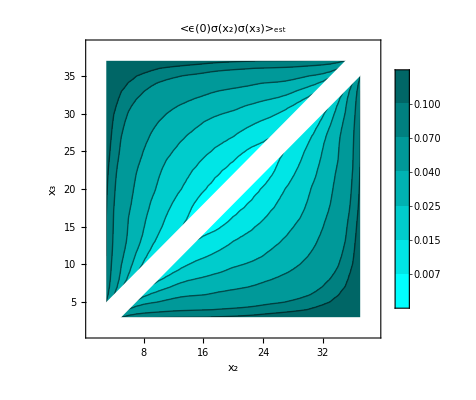

fig-eps-sig-sig-sample-10e5.pdf

```mathematica
L=40;
Table[{i,j,((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528 √(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)measure0[[i,j,1]]},{i,1,39},{j,1,39}]//Flatten[#,1]&;
ListContourPlot[%,Contours->{0.007,0.015,0.025,0.04,0.07,10^-1},PlotLegends->BarLegend[Automatic,All(*,"TickLabels"->(Superscript[10,#]&/@{-2,-1.5,-1})*)],FrameLabel->{"x_2","x_3"},ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}],PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>_est"];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-sample-10e5.pdf",Rasterize[%,"Image"]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Documents/GitHub/three_point_function_CFT

```mathematica
Ising3pt[x1_,x2_,x3_]:=c123/((Abs[(L/π)Sin[(x1-x2) π/L]])^Δϵ(Abs[(L/π)Sin[(x1-x3) π/L]])^Δϵ(Abs[(L/π)Sin[(x2-x3) π/L]])^(2Δσ-Δϵ))/.{Δϵ->1,Δσ->1/8,c123->1/2};
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

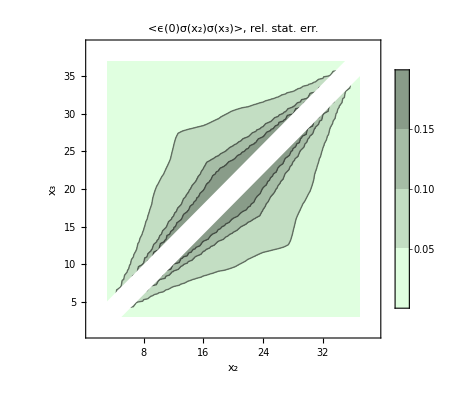

```mathematica
Table[{i,j,((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528 √(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)1/(√(10^5))measure0[[i,j,2]]/Ising3pt[0,i,j]},{i,1,39},{j,1,39}]//Flatten[#,1]&;
ListContourPlot[%,Contours->{0.05,0.1,0.15,0.2},FrameLabel->{"x_2","x_3"},ClippingStyle->Automatic,ContourShading->Table[Darker[LightGreen,i],{i,0,1,0.13}],PlotLegends->Automatic,PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, rel. stat. err."];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
(*Export["fig-eps-sig-sig-relative-stat-error.pdf",Rasterize[%,"Image"]]*)
```

### sample ⟨ϵϵ⟩

```mathematica
x=(L/π)Sin[# π/L]&/@Table[l,{l,1,20}]//N;
y={0.8905946470689284,0.43901749783384836,0.24565417782477345,0.08190179708792018,0.04850172506953591,0.031364848015677266,0.023099285946382154,0.018427999042131556,0.01575612036169317,0.013193319566343658,0.011443837370511198,0.010123253654891778,0.008347296244230374,0.0071029611473154034,0.006373304226655958,0.005822619758233793,0.005633057220065379,0.005562103644326467,0.0056701225208244214,0.005822619758234121};
dy={0.0004754207445823514,0.0008324070529833501,0.0009892705968345752,0.0010353524330305136,0.0010231761380094528,0.0010266470998042453,0.0009950338742629999,0.001015915516836737,0.000992420715933778,0.0010176861038860194,0.0009915517041484434,0.0010181424404810977,0.0009919297888664957,0.0010196670794586874,0.0010012181405988827,0.0010325936342785325,0.0010288642818535912,0.001116572859164384,0.0012586839172700997,0.0014185195742746552};
data$temp=MapThread[{#1,Around[#2,#3]}&,{x,y,dy}];
```

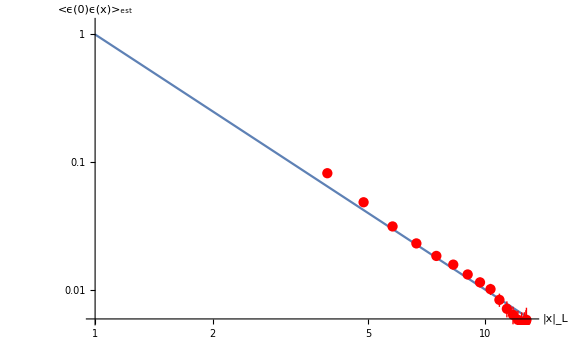

fig-eps-eps-sample-10e5.pdf

```mathematica
g=Show[LogLogPlot[1/y^2,{y,1,13},PlotRange->{Automatic,{0,1.2}}],ListLogLogPlot[data$temp[[4;;20]],(*draw error bars*)IntervalMarkersStyle->Automatic,PlotRange->All,AxesLabel->{"x","y"},PlotStyle->Red],AxesLabel->{"|x|_L","<ϵ(0)ϵ(x)>_est"},ImageSize->Large,AxesStyle->Large]
(*Export["fig-eps-eps-sample-10e5.pdf",%]*)
```

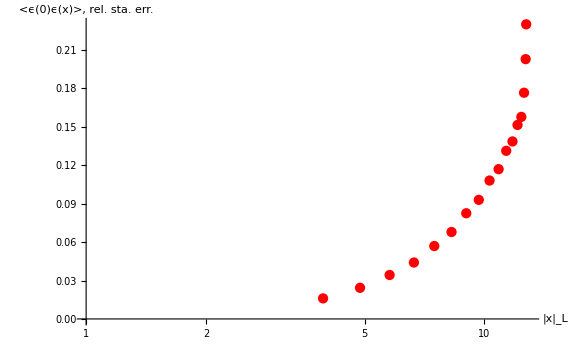

fig-eps-eps-sample-rserror.pdf

```mathematica
MapThread[{#1,#2/(1/#1^2)}&,{x,dy}]//ListLogLinearPlot[#[[4;;20]],PlotRange->{{1,13},All},PlotStyle->Red,AxesLabel->{"|x|_L","<ϵ(0)ϵ(x)>, rel. sta. err."},ImageSize->Large,AxesStyle->Large]&
(*Export["fig-eps-eps-sample-rserror.pdf",%]*)
```